```mathematica
Needs["ExperimentEvaluation`"]
```

## Experiments I

```mathematica
data=readAllFiles[{"20110803/GP4D_1000","GPAT4D_SSM_500"},labels,ReplaceParamValues->{"FC55"->"ZFC55"}];
```

```mathematica
StringReplace[#,"~/java/exp/"->""]&/@FileNames["~/java/exp/GPAT_MAZE_MAP*"]
```

{GPAT_MAZE_MAP2_NOVER,GPAT_MAZE_MAP2_ORIG,GPAT_MAZE_MAP2_RF4,GPAT_MAZE_MAP2_RF8,GPAT_MAZE_MAP3_NOVER,GPAT_MAZE_MAP3_ORIG,GPAT_MAZE_MAP3_RF4,GPAT_MAZE_MAP3_RF8,GPAT_MAZE_MAP4_NOVER,GPAT_MAZE_MAP4_ORIG,GPAT_MAZE_MAP4_RF4,GPAT_MAZE_MAP4_RF8}

```mathematica
data=readAllFiles[(StringReplace[#,"~/java/exp/"->""]&/@FileNames["~/java/exp/GP_MAZE_MAP*"])~Join~(StringReplace[#,"~/java/exp/"->""]&/@FileNames["~/java/exp/GPAT_MAZE_MAP*"])~Join~{"GPATGP_MAZE_ALL"},labels];
```

```mathematica
names=Flatten@Transpose@{{"GP_MAZE_MAP2_ORIG","GP_MAZE_MAP2_RF4","GP_MAZE_MAP2_RF8","GP_MAZE_MAP2_NOVER","GP_MAZE_MAP3_ORIG","GP_MAZE_MAP3_RF4","GP_MAZE_MAP3_RF8","GP_MAZE_MAP3_NOVER"},{"GPAT_MAZE_MAP2_ORIG","GPAT_MAZE_MAP2_RF4","GPAT_MAZE_MAP2_RF8","GPAT_MAZE_MAP2_NOVER","GPAT_MAZE_MAP3_ORIG","GPAT_MAZE_MAP3_RF4","GPAT_MAZE_MAP3_RF8","GPAT_MAZE_MAP3_NOVER"}};
```

```mathematica
labels={"GP_MAP2_NOVER","GP_MAP2_ORIG","GP_MAP2_RF4","GP_MAP2_RF8","GP_MAP3_NOVER","GP_MAP3_ORIG","GP_MAP3_RF4","GP_MAP3_RF8","GP_MAP4_NOVER","GP_MAP4_ORIG","GP_MAP4_RF4","GP_MAP4_RF8","GPAT_MAP2_NOVER","GPAT_MAP2_ORIG","GPAT_MAP2_RF4","GPAT_MAP2_RF8","GPAT_MAP3_NOVER","GPAT_MAP3_ORIG","GPAT_MAP3_RF4","GPAT_MAP3_RF8","GPAT_MAP4_NOVER","GPAT_MAP4_ORIG","GPAT_MAP4_RF4","GATP_MAP4_RF8","GPATGP_MAP2_ORIG","GPATGP_MAP2_NOVER","GPATGP_MAP2_RF4","GPATGP_MAP2_RF8","GPATGP_MAP3_ORIG","GPATGP_MAP3_NOVER","GPATGP_MAP3_RF4","GPATGP_MAP3_RF8","GPATGP_MAP24_ORIG","GPATGP_MAP4_NOVER","GPATGP_MAP4_RF4","GPATGP_MAP4_RF8"};
```

```mathematica
data=readAllFiles[names,labels];
```

```mathematica
listAllFiles[{"GP_4D_FC55_1000_old","GPAT_4D_FC55_ALL"}]
```

{{/Users/drchaj1/java/exp/GP_4D_FC55_1000_old/experiments_010.txt,/Users/drchaj1/java/exp/GP_4D_FC55_1000_old/parameters_010.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_001.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_001.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_002.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_002.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_003.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_003.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_004.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_004.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_005.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_005.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_006.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_006.txt}}

```mathematica
names={"GP_MAP2_200_old","GPAT_MAP2_ALL","GP_2D_H_1000_old","GPAT_2D_H_ALL","GP_4D_F_1000_old","GPAT_4D_F_ALL","GP_4D_FC55_1000_old","GPAT_4D_FC55_ALL"};
labels=Flatten[Outer[StringJoin[#2,#1]&,{"MAP2","2D_H","4D_F","4D_FC55"},{"GP_","GPAT_BASIC_","GPAT_RANDOM_","GPAT_CONSTANT1_","GPAT_SIMPLE_","GPAT_SIMPLE_REC_","GPAT_SIMPLE_REC2_","GPAT_SIMPLE_REC3_","GPAT_SIMPLE_ROOTO_","GPAT_SIMPLE_REC4_","GPAT_SIMPLE_SIMPLE2_","GPAT_SIMPLE_REC5_"}]];
data=readAllFiles[names,labels];
```

```mathematica
StringReplace[#,"~/java/exp/"->""]&/@FileNames["~/java/exp/GPAT_MAZE_MAP*"]
```

{GPAT_MAZE_MAP2_NOVER,GPAT_MAZE_MAP2_ORIG,GPAT_MAZE_MAP2_RF4,GPAT_MAZE_MAP2_RF8,GPAT_MAZE_MAP3_NOVER,GPAT_MAZE_MAP3_ORIG,GPAT_MAZE_MAP3_RF4,GPAT_MAZE_MAP3_RF8,GPAT_MAZE_MAP4_NOVER,GPAT_MAZE_MAP4_ORIG,GPAT_MAZE_MAP4_RF4,GPAT_MAZE_MAP4_RF8}

```mathematica
keepOnlyBest[StringReplace[#,"~/java/exp/"->""]&/@FileNames["~/java/exp/GPATGP_MAZE_ALL"],"BSF",60]
```

```mathematica
changingParameters[data]
```

{GPAT.FUNCTION_IMPL,GP.MAX_EVALUATIONS,GP.MUTATION_CAUCHY_PROBABILITY,GP.TYPE,SOLVER,SYMBOLIC_REGRESSION_4D.F}

```mathematica
sortedData = data;
```

```mathematica
sortedData=sortDataByParams[data,{"SYMBOLIC_REGRESSION_4D.F"},ReplaceParamValues->{"ZFC55"->"FC55"}];
```

```mathematica
data=readAllFiles[{"GPAT_4D_FC55_ALL","A"}];
```

```mathematica
saveData[data,"B"]
```

```mathematica
printAsTable[sortedData,{"SOLVER","MAZE.MAP","SYMBOLIC_REGRESSION_4D.F","GP.TARGET_FITNESS","GP.TYPE","GPAT.FUNCTION_IMPL","GPAT.MUTATION_HEAVY_PROB","GPAT.MUTATION_HEAVY_POWER","GPAT.SPECIES_SIZE_MEAN"}]
```

ID | PARAM FILE | SOLVER | MAZE.MAP | SYMBOLIC_REGRESSION_4D.F | GP.TARGET_FITNESS | GP.TYPE | GPAT.FUNCTION_IMPL | GPAT.MUTATION_HEAVY_PROB | GPAT.MUTATION_HEAVY_POWER | GPAT.SPECIES_SIZE_MEAN
GP_MAP2 | GP_MAP2_200_old/parameters_001.txt | GP | map2.csv | NONE | 50. | gp.GP | NONE | NONE | NONE | NONE
GPAT_BASIC_MAP2 | GPAT_MAP2_ALL/parameters_001.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_RANDOM_MAP2 | GPAT_MAP2_ALL/parameters_002.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_CONSTANT1_MAP2 | GPAT_MAP2_ALL/parameters_003.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_MAP2 | GPAT_MAP2_ALL/parameters_004.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC_MAP2 | GPAT_MAP2_ALL/parameters_005.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC2_MAP2 | GPAT_MAP2_ALL/parameters_006.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC3_MAP2 | GPAT_MAP2_ALL/parameters_007.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_ROOTO_MAP2 | GPAT_MAP2_ALL/parameters_008.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC4_MAP2 | GPAT_MAP2_ALL/parameters_009.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_SIMPLE2_MAP2 | GPAT_MAP2_ALL/parameters_010.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC5_MAP2 | GPAT_MAP2_ALL/parameters_011.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GP_2D_H | GP_2D_H_1000_old/parameters_008.txt | GP | NONE | NONE | 0.95 | gp.GP | NONE | NONE | NONE | NONE
GPAT_BASIC_2D_H | GPAT_2D_H_ALL/parameters_001.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_RANDOM_2D_H | GPAT_2D_H_ALL/parameters_002.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_CONSTANT1_2D_H | GPAT_2D_H_ALL/parameters_003.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_2D_H | GPAT_2D_H_ALL/parameters_004.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC_2D_H | GPAT_2D_H_ALL/parameters_005.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC2_2D_H | GPAT_2D_H_ALL/parameters_006.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC3_2D_H | GPAT_2D_H_ALL/parameters_007.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_ROOTO_2D_H | GPAT_2D_H_ALL/parameters_008.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC4_2D_H | GPAT_2D_H_ALL/parameters_009.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_SIMPLE2_2D_H | GPAT_2D_H_ALL/parameters_010.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC5_2D_H | GPAT_2D_H_ALL/parameters_011.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GP_4D_F | GP_4D_F_1000_old/parameters_006.txt | GP | NONE | F | 0.95 | gp.GP | NONE | NONE | NONE | NONE
GPAT_BASIC_4D_F | GPAT_4D_F_ALL/parameters_001.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_RANDOM_4D_F | GPAT_4D_F_ALL/parameters_002.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_CONSTANT1_4D_F | GPAT_4D_F_ALL/parameters_003.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_4D_F | GPAT_4D_F_ALL/parameters_004.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC_4D_F | GPAT_4D_F_ALL/parameters_005.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC2_4D_F | GPAT_4D_F_ALL/parameters_006.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC3_4D_F | GPAT_4D_F_ALL/parameters_007.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_ROOTO_4D_F | GPAT_4D_F_ALL/parameters_008.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC4_4D_F | GPAT_4D_F_ALL/parameters_009.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_SIMPLE2_4D_F | GPAT_4D_F_ALL/parameters_010.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC5_4D_F | GPAT_4D_F_ALL/parameters_011.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GP_4D_FC55 | GP_4D_FC55_1000_old/parameters_010.txt | GP | NONE | FC55 | 0.95 | gp.GP | NONE | NONE | NONE | NONE
GPAT_BASIC_4D_FC55 | GPAT_4D_FC55_ALL/parameters_001.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_RANDOM_4D_FC55 | GPAT_4D_FC55_ALL/parameters_002.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_CONSTANT1_4D_FC55 | GPAT_4D_FC55_ALL/parameters_003.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_4D_FC55 | GPAT_4D_FC55_ALL/parameters_004.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC_4D_FC55 | GPAT_4D_FC55_ALL/parameters_005.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC2_4D_FC55 | GPAT_4D_FC55_ALL/parameters_006.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC3_4D_FC55 | GPAT_4D_FC55_ALL/parameters_007.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_ROOTO_4D_FC55 | GPAT_4D_FC55_ALL/parameters_008.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC4_4D_FC55 | GPAT_4D_FC55_ALL/parameters_009.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_SIMPLE2_4D_FC55 | GPAT_4D_FC55_ALL/parameters_010.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC5_4D_FC55 | GPAT_4D_FC55_ALL/parameters_011.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.

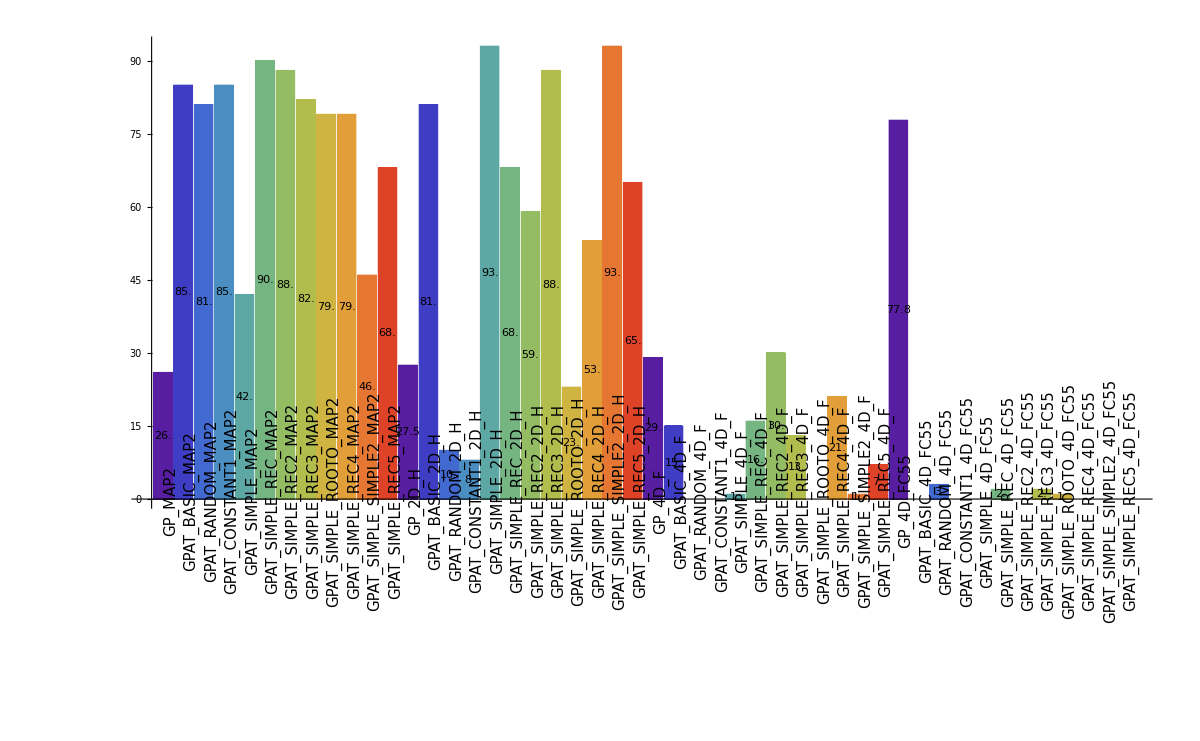

```mathematica
plotBooleanAsBarChart[sortedData,"SUCCESS",12]
```

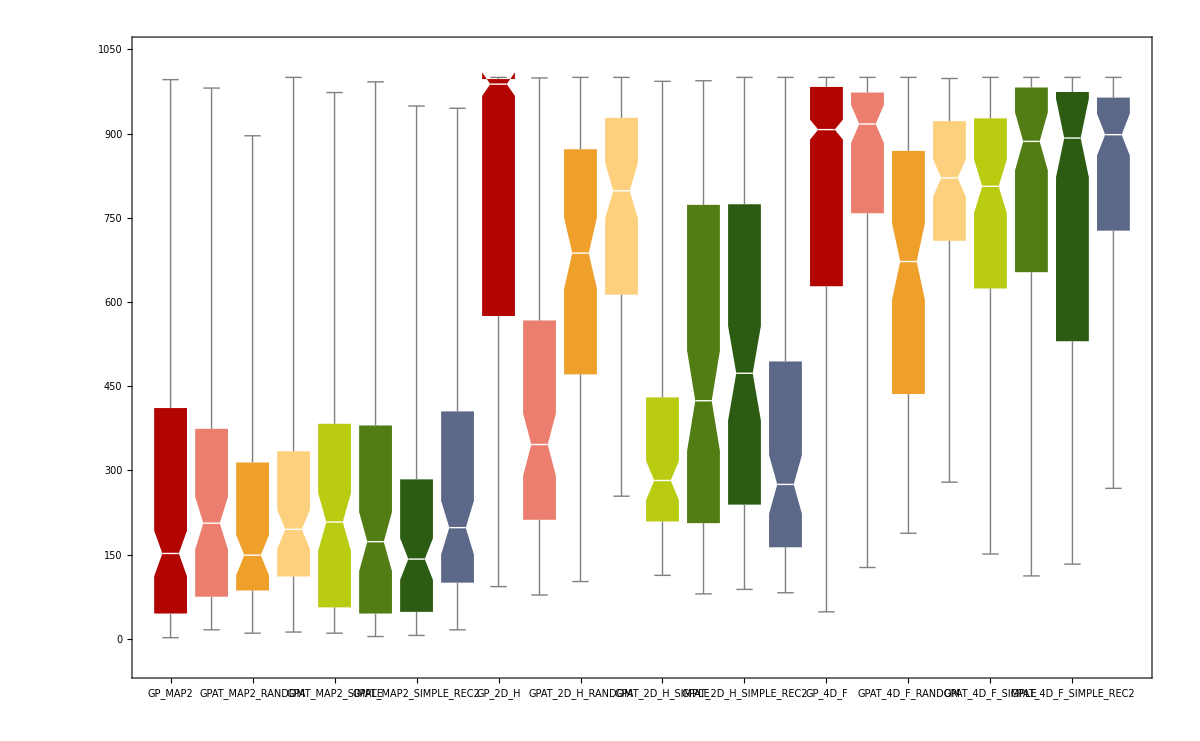

```mathematica
plotAsBoxWhiskerChart[sortedData,"BSFG",8]
```

## Experiments II

```mathematica
names={"GPAT_maze-1_REC7PAR","GPAT_maze-2_REC7PAR"};
data=readAllFiles[names,Null,ReplaceParamValues->{"FC55"->"ZFC55"}];
data=assignLabelsByParameters[data,{"SOLVER","ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","PROBLEM","GPAT.DISTANCE","GPAT.DISTANCE_REC5_C1","GPAT.DISTANCE_REC5_C2"},{"ZFC55"->"FC55",RegularExpression["gp.demo.SymbolicRegression.*"]->"","gp.demo.MazeRangeFinders"->"RF4","gp.demo.Maze"->"ORIG","map"->"MAP",".csv"->""}];
changingParameters[data]
```

{GPAT.DISTANCE_REC5_C1,GPAT.DISTANCE_REC5_C2,MAZE.MAP,PROBLEM}

```mathematica
(*sdata=selectData[data,{"SOLVER"->"GPAT","GPAT.DISTANCE"->{"SIMPLE_REC5","SIMPLE_REC6","SIMPLE_REC7"}}];*)
(*sdata=removeData[data,{"GPAT.DISTANCE"->{"CONSTANT","ROOTO","SIMPLE","SIMPLE_REC","SIMPLE_REC2","SIMPLE_REC3"}}];*)
sdata=removeData[data,{"GPAT.DISTANCE"->{"SIMPLE2","SIMPLE_REC4","SIMPLE_REC5","SIMPLE_REC6"}}];
sortedData = sortDataByParams[sdata,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","SOLVER","GPAT.DISTANCE","PROBLEM"}];
printAsTable[sortedData,{"SOLVER","GPAT.FUNCTION_IMPL","ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GPAT.DISTANCE","GP.TARGET_FITNESS","PROBLEM"}]
```

ID | PARAM FILE | SOLVER | GPAT.FUNCTION_IMPL | ID | SYMBOLIC_REGRESSION.F | MAZE.MAP | GPAT.DISTANCE | GP.TARGET_FITNESS | PROBLEM
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.1_0.1 | GPAT_maze-1_REC7PAR/parameters_001.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.1_0.5 | GPAT_maze-1_REC7PAR/parameters_002.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.1_0.8 | GPAT_maze-1_REC7PAR/parameters_003.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.1_0.9 | GPAT_maze-1_REC7PAR/parameters_004.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.1_0.95 | GPAT_maze-1_REC7PAR/parameters_005.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.5_0.1 | GPAT_maze-1_REC7PAR/parameters_006.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.5_0.5 | GPAT_maze-1_REC7PAR/parameters_007.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.5_0.8 | GPAT_maze-1_REC7PAR/parameters_008.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.5_0.9 | GPAT_maze-1_REC7PAR/parameters_009.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.5_0.95 | GPAT_maze-1_REC7PAR/parameters_010.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.9_0.1 | GPAT_maze-1_REC7PAR/parameters_011.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.9_0.5 | GPAT_maze-1_REC7PAR/parameters_012.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.9_0.8 | GPAT_maze-1_REC7PAR/parameters_013.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.9_0.9 | GPAT_maze-1_REC7PAR/parameters_014.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.9_0.95 | GPAT_maze-1_REC7PAR/parameters_015.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.1_0.1 | GPAT_maze-2_REC7PAR/parameters_001.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.1_0.5 | GPAT_maze-2_REC7PAR/parameters_002.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.1_0.8 | GPAT_maze-2_REC7PAR/parameters_003.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.1_0.9 | GPAT_maze-2_REC7PAR/parameters_004.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.1_0.95 | GPAT_maze-2_REC7PAR/parameters_005.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.5_0.1 | GPAT_maze-2_REC7PAR/parameters_006.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.5_0.5 | GPAT_maze-2_REC7PAR/parameters_007.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.5_0.8 | GPAT_maze-2_REC7PAR/parameters_008.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.5_0.9 | GPAT_maze-2_REC7PAR/parameters_009.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.5_0.95 | GPAT_maze-2_REC7PAR/parameters_010.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.9_0.1 | GPAT_maze-2_REC7PAR/parameters_011.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.9_0.5 | GPAT_maze-2_REC7PAR/parameters_012.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.9_0.8 | GPAT_maze-2_REC7PAR/parameters_013.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.9_0.9 | GPAT_maze-2_REC7PAR/parameters_014.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.9_0.95 | GPAT_maze-2_REC7PAR/parameters_015.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders

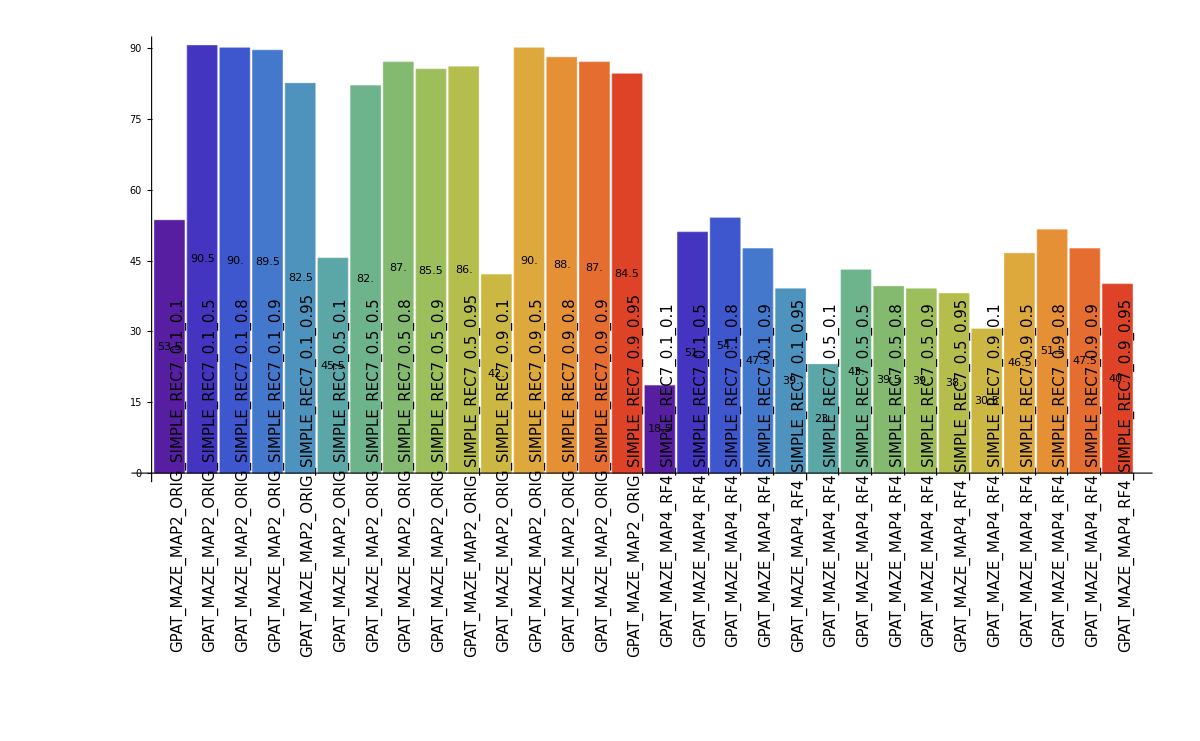

```mathematica
plotBooleanAsBarChart[sortedData,"SUCCESS",15]
```

## Experiments III

```mathematica
names={"GP_RANDOMPAR","GP_BASICPAR","GP_RESTO2PAR","GP_TREEPPAR","GP_TREEP2PAR"};
(*names={"GP_RESTO2PAR"};*)
(*names={"GP_1D*","GPAT_1D*","GP_2D*","GPAT_2D*"};*)
(*names={"GP_1D*","GPAT_1D*"};*)
(*names={"GP_2D*","GPAT_2D*"};*)
(*names={"GP_3D*","GPAT_3D*"};*)
(*names={"GP_4D*","GPAT_4D*"};*)
(*names={"GP_maze*","GPAT_maze*"};*)
(*names={"GP_1D*","GPAT_1D*","GP_2D*","GPAT_2D*","GP_3D*","GPAT_3D*","GP_4D*","GPAT_4D*","GP_maze*","GPAT_maze*"};*)
(*names={"GP_maze-1_BASIC","GP_maze-2_BASIC"};*)
data=readAllFiles[names,Null,ReplaceParamValues->{"FC55"->"ZFC55"}];
data=assignLabelsByParameters[data,{"SOLVER","ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","PROBLEM","GPAT.DISTANCE","GP.DISTANCE","GPEFS.SPECIES_REPRODUCTION_RATIO","GPEFS.SPECIES_SIZE_MEAN"},{"ZFC55"->"FC55",RegularExpression["gp.demo.SymbolicRegression.*"]->"","gp.demo.MazeRangeFinders"->"RF4","gp.demo.Maze"->"ORIG","map"->"MAP",".csv"->""}];
changingParameters[data]
```

{GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GP.DISTANCE,GPEFS.SPECIES_REPRODUCTION_RATIO,GPEFS.SPECIES_SIZE_MEAN,GP.TARGET_FITNESS,ID,MAZE.MAP,PROBLEM,SYMBOLIC_REGRESSION.F}

```mathematica
saveData[data,"A"]
```

```mathematica
(*sdata=selectData[data,{"SOLVER"->"GPAT","GPAT.DISTANCE"->{"SIMPLE_REC5","SIMPLE_REC6","SIMPLE_REC7"}}];*)
(*sdata=removeData[data,{"GPAT.DISTANCE"->{"CONSTANT","ROOTO","SIMPLE","SIMPLE_REC","SIMPLE_REC2","SIMPLE_REC3"}}];*)
(*sdata=removeData[data,{"GPAT.DISTANCE"->{"SIMPLE2","SIMPLE_REC4","SIMPLE_REC5","SIMPLE_REC6"}}];*)
sdata=selectData[data,{"ID"->{"1D"}}];
sortedData = sortDataByParams[data,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","SOLVER","GPAT.DISTANCE","PROBLEM"}];
printAsTable[sortedData,{"SOLVER","GPAT.FUNCTION_IMPL","ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GPAT.DISTANCE","GP.DISTANCE","GPEFS.SPECIES_REPRODUCTION_RATIO","GPEFS.SPECIES_SIZE_MEAN","PROBLEM"}]
```

ID | PARAM FILE | SOLVER | GPAT.FUNCTION_IMPL | ID | SYMBOLIC_REGRESSION.F | MAZE.MAP | GPAT.DISTANCE | GP.DISTANCE | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | PROBLEM
GP_1D_F_RANDOM_0.05_5. | GP_RANDOMPAR/parameters_001.txt | GP | NONE | 1D | F | NONE | NONE | RANDOM | 0.05 | 5. | gp.demo.SymbolicRegression
GP_1D_F_RANDOM_0.05_10. | GP_RANDOMPAR/parameters_003.txt | GP | NONE | 1D | F | NONE | NONE | RANDOM | 0.05 | 10. | gp.demo.SymbolicRegression
GP_1D_F_RANDOM_0.05_20. | GP_RANDOMPAR/parameters_005.txt | GP | NONE | 1D | F | NONE | NONE | RANDOM | 0.05 | 20. | gp.demo.SymbolicRegression
GP_1D_F_RANDOM_0.1_5. | GP_RANDOMPAR/parameters_007.txt | GP | NONE | 1D | F | NONE | NONE | RANDOM | 0.1 | 5. | gp.demo.SymbolicRegression
GP_1D_F_RANDOM_0.1_10. | GP_RANDOMPAR/parameters_009.txt | GP | NONE | 1D | F | NONE | NONE | RANDOM | 0.1 | 10. | gp.demo.SymbolicRegression
GP_1D_F_RANDOM_0.1_20. | GP_RANDOMPAR/parameters_011.txt | GP | NONE | 1D | F | NONE | NONE | RANDOM | 0.1 | 20. | gp.demo.SymbolicRegression
GP_1D_F_RANDOM_0.2_5. | GP_RANDOMPAR/parameters_013.txt | GP | NONE | 1D | F | NONE | NONE | RANDOM | 0.2 | 5. | gp.demo.SymbolicRegression
GP_1D_F_RANDOM_0.2_10. | GP_RANDOMPAR/parameters_015.txt | GP | NONE | 1D | F | NONE | NONE | RANDOM | 0.2 | 10. | gp.demo.SymbolicRegression
GP_1D_F_RANDOM_0.2_20. | GP_RANDOMPAR/parameters_017.txt | GP | NONE | 1D | F | NONE | NONE | RANDOM | 0.2 | 20. | gp.demo.SymbolicRegression
GP_1D_F_RANDOM_0.4_5. | GP_RANDOMPAR/parameters_019.txt | GP | NONE | 1D | F | NONE | NONE | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression
GP_1D_F_RANDOM_0.4_10. | GP_RANDOMPAR/parameters_021.txt | GP | NONE | 1D | F | NONE | NONE | RANDOM | 0.4 | 10. | gp.demo.SymbolicRegression
GP_1D_F_RANDOM_0.4_20. | GP_RANDOMPAR/parameters_023.txt | GP | NONE | 1D | F | NONE | NONE | RANDOM | 0.4 | 20. | gp.demo.SymbolicRegression
GP_1D_F_BASIC_0.05_5. | GP_BASICPAR/parameters_001.txt | GP | NONE | 1D | F | NONE | NONE | BASIC | 0.05 | 5. | gp.demo.SymbolicRegression
GP_1D_F_BASIC_0.05_10. | GP_BASICPAR/parameters_003.txt | GP | NONE | 1D | F | NONE | NONE | BASIC | 0.05 | 10. | gp.demo.SymbolicRegression
GP_1D_F_BASIC_0.05_20. | GP_BASICPAR/parameters_005.txt | GP | NONE | 1D | F | NONE | NONE | BASIC | 0.05 | 20. | gp.demo.SymbolicRegression
GP_1D_F_BASIC_0.1_5. | GP_BASICPAR/parameters_007.txt | GP | NONE | 1D | F | NONE | NONE | BASIC | 0.1 | 5. | gp.demo.SymbolicRegression
GP_1D_F_BASIC_0.1_10. | GP_BASICPAR/parameters_009.txt | GP | NONE | 1D | F | NONE | NONE | BASIC | 0.1 | 10. | gp.demo.SymbolicRegression
GP_1D_F_BASIC_0.1_20. | GP_BASICPAR/parameters_011.txt | GP | NONE | 1D | F | NONE | NONE | BASIC | 0.1 | 20. | gp.demo.SymbolicRegression
GP_1D_F_BASIC_0.2_5. | GP_BASICPAR/parameters_013.txt | GP | NONE | 1D | F | NONE | NONE | BASIC | 0.2 | 5. | gp.demo.SymbolicRegression
GP_1D_F_BASIC_0.2_10. | GP_BASICPAR/parameters_015.txt | GP | NONE | 1D | F | NONE | NONE | BASIC | 0.2 | 10. | gp.demo.SymbolicRegression
GP_1D_F_BASIC_0.2_20. | GP_BASICPAR/parameters_017.txt | GP | NONE | 1D | F | NONE | NONE | BASIC | 0.2 | 20. | gp.demo.SymbolicRegression
GP_1D_F_BASIC_0.4_5. | GP_BASICPAR/parameters_019.txt | GP | NONE | 1D | F | NONE | NONE | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression
GP_1D_F_BASIC_0.4_10. | GP_BASICPAR/parameters_021.txt | GP | NONE | 1D | F | NONE | NONE | BASIC | 0.4 | 10. | gp.demo.SymbolicRegression
GP_1D_F_BASIC_0.4_20. | GP_BASICPAR/parameters_023.txt | GP | NONE | 1D | F | NONE | NONE | BASIC | 0.4 | 20. | gp.demo.SymbolicRegression
GP_1D_F_RESTO2_0.05_5. | GP_RESTO2PAR/parameters_001.txt | GP | NONE | 1D | F | NONE | NONE | RESTO2 | 0.05 | 5. | gp.demo.SymbolicRegression
GP_1D_F_RESTO2_0.05_10. | GP_RESTO2PAR/parameters_003.txt | GP | NONE | 1D | F | NONE | NONE | RESTO2 | 0.05 | 10. | gp.demo.SymbolicRegression
GP_1D_F_RESTO2_0.05_20. | GP_RESTO2PAR/parameters_005.txt | GP | NONE | 1D | F | NONE | NONE | RESTO2 | 0.05 | 20. | gp.demo.SymbolicRegression
GP_1D_F_RESTO2_0.1_5. | GP_RESTO2PAR/parameters_007.txt | GP | NONE | 1D | F | NONE | NONE | RESTO2 | 0.1 | 5. | gp.demo.SymbolicRegression
GP_1D_F_RESTO2_0.1_10. | GP_RESTO2PAR/parameters_009.txt | GP | NONE | 1D | F | NONE | NONE | RESTO2 | 0.1 | 10. | gp.demo.SymbolicRegression
GP_1D_F_RESTO2_0.1_20. | GP_RESTO2PAR/parameters_011.txt | GP | NONE | 1D | F | NONE | NONE | RESTO2 | 0.1 | 20. | gp.demo.SymbolicRegression
GP_1D_F_RESTO2_0.2_5. | GP_RESTO2PAR/parameters_013.txt | GP | NONE | 1D | F | NONE | NONE | RESTO2 | 0.2 | 5. | gp.demo.SymbolicRegression
GP_1D_F_RESTO2_0.2_10. | GP_RESTO2PAR/parameters_015.txt | GP | NONE | 1D | F | NONE | NONE | RESTO2 | 0.2 | 10. | gp.demo.SymbolicRegression
GP_1D_F_RESTO2_0.2_20. | GP_RESTO2PAR/parameters_017.txt | GP | NONE | 1D | F | NONE | NONE | RESTO2 | 0.2 | 20. | gp.demo.SymbolicRegression
GP_1D_F_RESTO2_0.4_5. | GP_RESTO2PAR/parameters_019.txt | GP | NONE | 1D | F | NONE | NONE | RESTO2 | 0.4 | 5. | gp.demo.SymbolicRegression
GP_1D_F_RESTO2_0.4_10. | GP_RESTO2PAR/parameters_021.txt | GP | NONE | 1D | F | NONE | NONE | RESTO2 | 0.4 | 10. | gp.demo.SymbolicRegression
GP_1D_F_RESTO2_0.4_20. | GP_RESTO2PAR/parameters_023.txt | GP | NONE | 1D | F | NONE | NONE | RESTO2 | 0.4 | 20. | gp.demo.SymbolicRegression
GP_1D_F_TREEP_0.05_5. | GP_TREEPPAR/parameters_001.txt | GP | NONE | 1D | F | NONE | NONE | TREEP | 0.05 | 5. | gp.demo.SymbolicRegression
GP_1D_F_TREEP_0.05_10. | GP_TREEPPAR/parameters_003.txt | GP | NONE | 1D | F | NONE | NONE | TREEP | 0.05 | 10. | gp.demo.SymbolicRegression
GP_1D_F_TREEP_0.05_20. | GP_TREEPPAR/parameters_005.txt | GP | NONE | 1D | F | NONE | NONE | TREEP | 0.05 | 20. | gp.demo.SymbolicRegression
GP_1D_F_TREEP_0.1_5. | GP_TREEPPAR/parameters_007.txt | GP | NONE | 1D | F | NONE | NONE | TREEP | 0.1 | 5. | gp.demo.SymbolicRegression
GP_1D_F_TREEP_0.1_10. | GP_TREEPPAR/parameters_009.txt | GP | NONE | 1D | F | NONE | NONE | TREEP | 0.1 | 10. | gp.demo.SymbolicRegression
GP_1D_F_TREEP_0.1_20. | GP_TREEPPAR/parameters_011.txt | GP | NONE | 1D | F | NONE | NONE | TREEP | 0.1 | 20. | gp.demo.SymbolicRegression
GP_1D_F_TREEP_0.2_5. | GP_TREEPPAR/parameters_013.txt | GP | NONE | 1D | F | NONE | NONE | TREEP | 0.2 | 5. | gp.demo.SymbolicRegression
GP_1D_F_TREEP_0.2_10. | GP_TREEPPAR/parameters_015.txt | GP | NONE | 1D | F | NONE | NONE | TREEP | 0.2 | 10. | gp.demo.SymbolicRegression
GP_1D_F_TREEP_0.2_20. | GP_TREEPPAR/parameters_017.txt | GP | NONE | 1D | F | NONE | NONE | TREEP | 0.2 | 20. | gp.demo.SymbolicRegression
GP_1D_F_TREEP_0.4_5. | GP_TREEPPAR/parameters_019.txt | GP | NONE | 1D | F | NONE | NONE | TREEP | 0.4 | 5. | gp.demo.SymbolicRegression
GP_1D_F_TREEP_0.4_10. | GP_TREEPPAR/parameters_021.txt | GP | NONE | 1D | F | NONE | NONE | TREEP | 0.4 | 10. | gp.demo.SymbolicRegression
GP_1D_F_TREEP_0.4_20. | GP_TREEPPAR/parameters_023.txt | GP | NONE | 1D | F | NONE | NONE | TREEP | 0.4 | 20. | gp.demo.SymbolicRegression
GP_1D_F_TREEP2_0.05_5. | GP_TREEP2PAR/parameters_001.txt | GP | NONE | 1D | F | NONE | NONE | TREEP2 | 0.05 | 5. | gp.demo.SymbolicRegression
GP_1D_F_TREEP2_0.05_10. | GP_TREEP2PAR/parameters_003.txt | GP | NONE | 1D | F | NONE | NONE | TREEP2 | 0.05 | 10. | gp.demo.SymbolicRegression
GP_1D_F_TREEP2_0.05_20. | GP_TREEP2PAR/parameters_005.txt | GP | NONE | 1D | F | NONE | NONE | TREEP2 | 0.05 | 20. | gp.demo.SymbolicRegression
GP_1D_F_TREEP2_0.1_5. | GP_TREEP2PAR/parameters_007.txt | GP | NONE | 1D | F | NONE | NONE | TREEP2 | 0.1 | 5. | gp.demo.SymbolicRegression
GP_1D_F_TREEP2_0.1_10. | GP_TREEP2PAR/parameters_009.txt | GP | NONE | 1D | F | NONE | NONE | TREEP2 | 0.1 | 10. | gp.demo.SymbolicRegression
GP_1D_F_TREEP2_0.1_20. | GP_TREEP2PAR/parameters_011.txt | GP | NONE | 1D | F | NONE | NONE | TREEP2 | 0.1 | 20. | gp.demo.SymbolicRegression
GP_1D_F_TREEP2_0.2_5. | GP_TREEP2PAR/parameters_013.txt | GP | NONE | 1D | F | NONE | NONE | TREEP2 | 0.2 | 5. | gp.demo.SymbolicRegression
GP_1D_F_TREEP2_0.2_10. | GP_TREEP2PAR/parameters_015.txt | GP | NONE | 1D | F | NONE | NONE | TREEP2 | 0.2 | 10. | gp.demo.SymbolicRegression
GP_1D_F_TREEP2_0.2_20. | GP_TREEP2PAR/parameters_017.txt | GP | NONE | 1D | F | NONE | NONE | TREEP2 | 0.2 | 20. | gp.demo.SymbolicRegression
GP_1D_F_TREEP2_0.4_5. | GP_TREEP2PAR/parameters_019.txt | GP | NONE | 1D | F | NONE | NONE | TREEP2 | 0.4 | 5. | gp.demo.SymbolicRegression
GP_1D_F_TREEP2_0.4_10. | GP_TREEP2PAR/parameters_021.txt | GP | NONE | 1D | F | NONE | NONE | TREEP2 | 0.4 | 10. | gp.demo.SymbolicRegression
GP_1D_F_TREEP2_0.4_20. | GP_TREEP2PAR/parameters_023.txt | GP | NONE | 1D | F | NONE | NONE | TREEP2 | 0.4 | 20. | gp.demo.SymbolicRegression
GP_1D_H_RANDOM_0.05_5. | GP_RANDOMPAR/parameters_002.txt | GP | NONE | 1D | H | NONE | NONE | RANDOM | 0.05 | 5. | gp.demo.SymbolicRegression
GP_1D_H_RANDOM_0.05_10. | GP_RANDOMPAR/parameters_004.txt | GP | NONE | 1D | H | NONE | NONE | RANDOM | 0.05 | 10. | gp.demo.SymbolicRegression
GP_1D_H_RANDOM_0.05_20. | GP_RANDOMPAR/parameters_006.txt | GP | NONE | 1D | H | NONE | NONE | RANDOM | 0.05 | 20. | gp.demo.SymbolicRegression
GP_1D_H_RANDOM_0.1_5. | GP_RANDOMPAR/parameters_008.txt | GP | NONE | 1D | H | NONE | NONE | RANDOM | 0.1 | 5. | gp.demo.SymbolicRegression
GP_1D_H_RANDOM_0.1_10. | GP_RANDOMPAR/parameters_010.txt | GP | NONE | 1D | H | NONE | NONE | RANDOM | 0.1 | 10. | gp.demo.SymbolicRegression
GP_1D_H_RANDOM_0.1_20. | GP_RANDOMPAR/parameters_012.txt | GP | NONE | 1D | H | NONE | NONE | RANDOM | 0.1 | 20. | gp.demo.SymbolicRegression
GP_1D_H_RANDOM_0.2_5. | GP_RANDOMPAR/parameters_014.txt | GP | NONE | 1D | H | NONE | NONE | RANDOM | 0.2 | 5. | gp.demo.SymbolicRegression
GP_1D_H_RANDOM_0.2_10. | GP_RANDOMPAR/parameters_016.txt | GP | NONE | 1D | H | NONE | NONE | RANDOM | 0.2 | 10. | gp.demo.SymbolicRegression
GP_1D_H_RANDOM_0.2_20. | GP_RANDOMPAR/parameters_018.txt | GP | NONE | 1D | H | NONE | NONE | RANDOM | 0.2 | 20. | gp.demo.SymbolicRegression
GP_1D_H_RANDOM_0.4_5. | GP_RANDOMPAR/parameters_020.txt | GP | NONE | 1D | H | NONE | NONE | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression
GP_1D_H_RANDOM_0.4_10. | GP_RANDOMPAR/parameters_022.txt | GP | NONE | 1D | H | NONE | NONE | RANDOM | 0.4 | 10. | gp.demo.SymbolicRegression
GP_1D_H_RANDOM_0.4_20. | GP_RANDOMPAR/parameters_024.txt | GP | NONE | 1D | H | NONE | NONE | RANDOM | 0.4 | 20. | gp.demo.SymbolicRegression
GP_1D_H_BASIC_0.05_5. | GP_BASICPAR/parameters_002.txt | GP | NONE | 1D | H | NONE | NONE | BASIC | 0.05 | 5. | gp.demo.SymbolicRegression
GP_1D_H_BASIC_0.05_10. | GP_BASICPAR/parameters_004.txt | GP | NONE | 1D | H | NONE | NONE | BASIC | 0.05 | 10. | gp.demo.SymbolicRegression
GP_1D_H_BASIC_0.05_20. | GP_BASICPAR/parameters_006.txt | GP | NONE | 1D | H | NONE | NONE | BASIC | 0.05 | 20. | gp.demo.SymbolicRegression
GP_1D_H_BASIC_0.1_5. | GP_BASICPAR/parameters_008.txt | GP | NONE | 1D | H | NONE | NONE | BASIC | 0.1 | 5. | gp.demo.SymbolicRegression
GP_1D_H_BASIC_0.1_10. | GP_BASICPAR/parameters_010.txt | GP | NONE | 1D | H | NONE | NONE | BASIC | 0.1 | 10. | gp.demo.SymbolicRegression
GP_1D_H_BASIC_0.1_20. | GP_BASICPAR/parameters_012.txt | GP | NONE | 1D | H | NONE | NONE | BASIC | 0.1 | 20. | gp.demo.SymbolicRegression
GP_1D_H_BASIC_0.2_5. | GP_BASICPAR/parameters_014.txt | GP | NONE | 1D | H | NONE | NONE | BASIC | 0.2 | 5. | gp.demo.SymbolicRegression
GP_1D_H_BASIC_0.2_10. | GP_BASICPAR/parameters_016.txt | GP | NONE | 1D | H | NONE | NONE | BASIC | 0.2 | 10. | gp.demo.SymbolicRegression
GP_1D_H_BASIC_0.2_20. | GP_BASICPAR/parameters_018.txt | GP | NONE | 1D | H | NONE | NONE | BASIC | 0.2 | 20. | gp.demo.SymbolicRegression
GP_1D_H_BASIC_0.4_5. | GP_BASICPAR/parameters_020.txt | GP | NONE | 1D | H | NONE | NONE | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression
GP_1D_H_BASIC_0.4_10. | GP_BASICPAR/parameters_022.txt | GP | NONE | 1D | H | NONE | NONE | BASIC | 0.4 | 10. | gp.demo.SymbolicRegression
GP_1D_H_BASIC_0.4_20. | GP_BASICPAR/parameters_024.txt | GP | NONE | 1D | H | NONE | NONE | BASIC | 0.4 | 20. | gp.demo.SymbolicRegression
GP_1D_H_RESTO2_0.05_5. | GP_RESTO2PAR/parameters_002.txt | GP | NONE | 1D | H | NONE | NONE | RESTO2 | 0.05 | 5. | gp.demo.SymbolicRegression
GP_1D_H_RESTO2_0.05_10. | GP_RESTO2PAR/parameters_004.txt | GP | NONE | 1D | H | NONE | NONE | RESTO2 | 0.05 | 10. | gp.demo.SymbolicRegression
GP_1D_H_RESTO2_0.05_20. | GP_RESTO2PAR/parameters_006.txt | GP | NONE | 1D | H | NONE | NONE | RESTO2 | 0.05 | 20. | gp.demo.SymbolicRegression
GP_1D_H_RESTO2_0.1_5. | GP_RESTO2PAR/parameters_008.txt | GP | NONE | 1D | H | NONE | NONE | RESTO2 | 0.1 | 5. | gp.demo.SymbolicRegression
GP_1D_H_RESTO2_0.1_10. | GP_RESTO2PAR/parameters_010.txt | GP | NONE | 1D | H | NONE | NONE | RESTO2 | 0.1 | 10. | gp.demo.SymbolicRegression
GP_1D_H_RESTO2_0.1_20. | GP_RESTO2PAR/parameters_012.txt | GP | NONE | 1D | H | NONE | NONE | RESTO2 | 0.1 | 20. | gp.demo.SymbolicRegression
GP_1D_H_RESTO2_0.2_5. | GP_RESTO2PAR/parameters_014.txt | GP | NONE | 1D | H | NONE | NONE | RESTO2 | 0.2 | 5. | gp.demo.SymbolicRegression
GP_1D_H_RESTO2_0.2_10. | GP_RESTO2PAR/parameters_016.txt | GP | NONE | 1D | H | NONE | NONE | RESTO2 | 0.2 | 10. | gp.demo.SymbolicRegression
GP_1D_H_RESTO2_0.2_20. | GP_RESTO2PAR/parameters_018.txt | GP | NONE | 1D | H | NONE | NONE | RESTO2 | 0.2 | 20. | gp.demo.SymbolicRegression
GP_1D_H_RESTO2_0.4_5. | GP_RESTO2PAR/parameters_020.txt | GP | NONE | 1D | H | NONE | NONE | RESTO2 | 0.4 | 5. | gp.demo.SymbolicRegression
GP_1D_H_RESTO2_0.4_10. | GP_RESTO2PAR/parameters_022.txt | GP | NONE | 1D | H | NONE | NONE | RESTO2 | 0.4 | 10. | gp.demo.SymbolicRegression
GP_1D_H_RESTO2_0.4_20. | GP_RESTO2PAR/parameters_024.txt | GP | NONE | 1D | H | NONE | NONE | RESTO2 | 0.4 | 20. | gp.demo.SymbolicRegression
GP_1D_H_TREEP_0.05_5. | GP_TREEPPAR/parameters_002.txt | GP | NONE | 1D | H | NONE | NONE | TREEP | 0.05 | 5. | gp.demo.SymbolicRegression
GP_1D_H_TREEP_0.05_10. | GP_TREEPPAR/parameters_004.txt | GP | NONE | 1D | H | NONE | NONE | TREEP | 0.05 | 10. | gp.demo.SymbolicRegression
GP_1D_H_TREEP_0.05_20. | GP_TREEPPAR/parameters_006.txt | GP | NONE | 1D | H | NONE | NONE | TREEP | 0.05 | 20. | gp.demo.SymbolicRegression
GP_1D_H_TREEP_0.1_5. | GP_TREEPPAR/parameters_008.txt | GP | NONE | 1D | H | NONE | NONE | TREEP | 0.1 | 5. | gp.demo.SymbolicRegression
GP_1D_H_TREEP_0.1_10. | GP_TREEPPAR/parameters_010.txt | GP | NONE | 1D | H | NONE | NONE | TREEP | 0.1 | 10. | gp.demo.SymbolicRegression
GP_1D_H_TREEP_0.1_20. | GP_TREEPPAR/parameters_012.txt | GP | NONE | 1D | H | NONE | NONE | TREEP | 0.1 | 20. | gp.demo.SymbolicRegression
GP_1D_H_TREEP_0.2_5. | GP_TREEPPAR/parameters_014.txt | GP | NONE | 1D | H | NONE | NONE | TREEP | 0.2 | 5. | gp.demo.SymbolicRegression
GP_1D_H_TREEP_0.2_10. | GP_TREEPPAR/parameters_016.txt | GP | NONE | 1D | H | NONE | NONE | TREEP | 0.2 | 10. | gp.demo.SymbolicRegression
GP_1D_H_TREEP_0.2_20. | GP_TREEPPAR/parameters_018.txt | GP | NONE | 1D | H | NONE | NONE | TREEP | 0.2 | 20. | gp.demo.SymbolicRegression
GP_1D_H_TREEP_0.4_5. | GP_TREEPPAR/parameters_020.txt | GP | NONE | 1D | H | NONE | NONE | TREEP | 0.4 | 5. | gp.demo.SymbolicRegression
GP_1D_H_TREEP_0.4_10. | GP_TREEPPAR/parameters_022.txt | GP | NONE | 1D | H | NONE | NONE | TREEP | 0.4 | 10. | gp.demo.SymbolicRegression
GP_1D_H_TREEP_0.4_20. | GP_TREEPPAR/parameters_024.txt | GP | NONE | 1D | H | NONE | NONE | TREEP | 0.4 | 20. | gp.demo.SymbolicRegression
GP_1D_H_TREEP2_0.05_5. | GP_TREEP2PAR/parameters_002.txt | GP | NONE | 1D | H | NONE | NONE | TREEP2 | 0.05 | 5. | gp.demo.SymbolicRegression
GP_1D_H_TREEP2_0.05_10. | GP_TREEP2PAR/parameters_004.txt | GP | NONE | 1D | H | NONE | NONE | TREEP2 | 0.05 | 10. | gp.demo.SymbolicRegression
GP_1D_H_TREEP2_0.05_20. | GP_TREEP2PAR/parameters_006.txt | GP | NONE | 1D | H | NONE | NONE | TREEP2 | 0.05 | 20. | gp.demo.SymbolicRegression
GP_1D_H_TREEP2_0.1_5. | GP_TREEP2PAR/parameters_008.txt | GP | NONE | 1D | H | NONE | NONE | TREEP2 | 0.1 | 5. | gp.demo.SymbolicRegression
GP_1D_H_TREEP2_0.1_10. | GP_TREEP2PAR/parameters_010.txt | GP | NONE | 1D | H | NONE | NONE | TREEP2 | 0.1 | 10. | gp.demo.SymbolicRegression
GP_1D_H_TREEP2_0.1_20. | GP_TREEP2PAR/parameters_012.txt | GP | NONE | 1D | H | NONE | NONE | TREEP2 | 0.1 | 20. | gp.demo.SymbolicRegression
GP_1D_H_TREEP2_0.2_5. | GP_TREEP2PAR/parameters_014.txt | GP | NONE | 1D | H | NONE | NONE | TREEP2 | 0.2 | 5. | gp.demo.SymbolicRegression
GP_1D_H_TREEP2_0.2_10. | GP_TREEP2PAR/parameters_016.txt | GP | NONE | 1D | H | NONE | NONE | TREEP2 | 0.2 | 10. | gp.demo.SymbolicRegression
GP_1D_H_TREEP2_0.2_20. | GP_TREEP2PAR/parameters_018.txt | GP | NONE | 1D | H | NONE | NONE | TREEP2 | 0.2 | 20. | gp.demo.SymbolicRegression
GP_1D_H_TREEP2_0.4_5. | GP_TREEP2PAR/parameters_020.txt | GP | NONE | 1D | H | NONE | NONE | TREEP2 | 0.4 | 5. | gp.demo.SymbolicRegression
GP_1D_H_TREEP2_0.4_10. | GP_TREEP2PAR/parameters_022.txt | GP | NONE | 1D | H | NONE | NONE | TREEP2 | 0.4 | 10. | gp.demo.SymbolicRegression
GP_1D_H_TREEP2_0.4_20. | GP_TREEP2PAR/parameters_024.txt | GP | NONE | 1D | H | NONE | NONE | TREEP2 | 0.4 | 20. | gp.demo.SymbolicRegression
GP_2D_I_RANDOM_0.05_5. | GP_RANDOMPAR/parameters_025.txt | GP | NONE | 2D | I | NONE | NONE | RANDOM | 0.05 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_RANDOM_0.05_10. | GP_RANDOMPAR/parameters_028.txt | GP | NONE | 2D | I | NONE | NONE | RANDOM | 0.05 | 10. | gp.demo.SymbolicRegression2D
GP_2D_I_RANDOM_0.05_20. | GP_RANDOMPAR/parameters_031.txt | GP | NONE | 2D | I | NONE | NONE | RANDOM | 0.05 | 20. | gp.demo.SymbolicRegression2D
GP_2D_I_RANDOM_0.1_5. | GP_RANDOMPAR/parameters_034.txt | GP | NONE | 2D | I | NONE | NONE | RANDOM | 0.1 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_RANDOM_0.1_10. | GP_RANDOMPAR/parameters_037.txt | GP | NONE | 2D | I | NONE | NONE | RANDOM | 0.1 | 10. | gp.demo.SymbolicRegression2D
GP_2D_I_RANDOM_0.1_20. | GP_RANDOMPAR/parameters_040.txt | GP | NONE | 2D | I | NONE | NONE | RANDOM | 0.1 | 20. | gp.demo.SymbolicRegression2D
GP_2D_I_RANDOM_0.2_5. | GP_RANDOMPAR/parameters_043.txt | GP | NONE | 2D | I | NONE | NONE | RANDOM | 0.2 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_RANDOM_0.2_10. | GP_RANDOMPAR/parameters_046.txt | GP | NONE | 2D | I | NONE | NONE | RANDOM | 0.2 | 10. | gp.demo.SymbolicRegression2D
GP_2D_I_RANDOM_0.2_20. | GP_RANDOMPAR/parameters_049.txt | GP | NONE | 2D | I | NONE | NONE | RANDOM | 0.2 | 20. | gp.demo.SymbolicRegression2D
GP_2D_I_RANDOM_0.4_5. | GP_RANDOMPAR/parameters_052.txt | GP | NONE | 2D | I | NONE | NONE | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_RANDOM_0.4_10. | GP_RANDOMPAR/parameters_055.txt | GP | NONE | 2D | I | NONE | NONE | RANDOM | 0.4 | 10. | gp.demo.SymbolicRegression2D
GP_2D_I_RANDOM_0.4_20. | GP_RANDOMPAR/parameters_058.txt | GP | NONE | 2D | I | NONE | NONE | RANDOM | 0.4 | 20. | gp.demo.SymbolicRegression2D
GP_2D_I_BASIC_0.05_5. | GP_BASICPAR/parameters_025.txt | GP | NONE | 2D | I | NONE | NONE | BASIC | 0.05 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_BASIC_0.05_10. | GP_BASICPAR/parameters_028.txt | GP | NONE | 2D | I | NONE | NONE | BASIC | 0.05 | 10. | gp.demo.SymbolicRegression2D
GP_2D_I_BASIC_0.05_20. | GP_BASICPAR/parameters_031.txt | GP | NONE | 2D | I | NONE | NONE | BASIC | 0.05 | 20. | gp.demo.SymbolicRegression2D
GP_2D_I_BASIC_0.1_5. | GP_BASICPAR/parameters_034.txt | GP | NONE | 2D | I | NONE | NONE | BASIC | 0.1 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_BASIC_0.1_10. | GP_BASICPAR/parameters_037.txt | GP | NONE | 2D | I | NONE | NONE | BASIC | 0.1 | 10. | gp.demo.SymbolicRegression2D
GP_2D_I_BASIC_0.1_20. | GP_BASICPAR/parameters_040.txt | GP | NONE | 2D | I | NONE | NONE | BASIC | 0.1 | 20. | gp.demo.SymbolicRegression2D
GP_2D_I_BASIC_0.2_5. | GP_BASICPAR/parameters_043.txt | GP | NONE | 2D | I | NONE | NONE | BASIC | 0.2 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_BASIC_0.2_10. | GP_BASICPAR/parameters_046.txt | GP | NONE | 2D | I | NONE | NONE | BASIC | 0.2 | 10. | gp.demo.SymbolicRegression2D
GP_2D_I_BASIC_0.2_20. | GP_BASICPAR/parameters_049.txt | GP | NONE | 2D | I | NONE | NONE | BASIC | 0.2 | 20. | gp.demo.SymbolicRegression2D
GP_2D_I_BASIC_0.4_5. | GP_BASICPAR/parameters_052.txt | GP | NONE | 2D | I | NONE | NONE | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_BASIC_0.4_10. | GP_BASICPAR/parameters_055.txt | GP | NONE | 2D | I | NONE | NONE | BASIC | 0.4 | 10. | gp.demo.SymbolicRegression2D
GP_2D_I_BASIC_0.4_20. | GP_BASICPAR/parameters_058.txt | GP | NONE | 2D | I | NONE | NONE | BASIC | 0.4 | 20. | gp.demo.SymbolicRegression2D
GP_2D_I_RESTO2_0.05_5. | GP_RESTO2PAR/parameters_025.txt | GP | NONE | 2D | I | NONE | NONE | RESTO2 | 0.05 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_RESTO2_0.05_10. | GP_RESTO2PAR/parameters_028.txt | GP | NONE | 2D | I | NONE | NONE | RESTO2 | 0.05 | 10. | gp.demo.SymbolicRegression2D
GP_2D_I_RESTO2_0.05_20. | GP_RESTO2PAR/parameters_031.txt | GP | NONE | 2D | I | NONE | NONE | RESTO2 | 0.05 | 20. | gp.demo.SymbolicRegression2D
GP_2D_I_RESTO2_0.1_5. | GP_RESTO2PAR/parameters_034.txt | GP | NONE | 2D | I | NONE | NONE | RESTO2 | 0.1 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_RESTO2_0.1_10. | GP_RESTO2PAR/parameters_037.txt | GP | NONE | 2D | I | NONE | NONE | RESTO2 | 0.1 | 10. | gp.demo.SymbolicRegression2D
GP_2D_I_RESTO2_0.1_20. | GP_RESTO2PAR/parameters_040.txt | GP | NONE | 2D | I | NONE | NONE | RESTO2 | 0.1 | 20. | gp.demo.SymbolicRegression2D
GP_2D_I_RESTO2_0.2_5. | GP_RESTO2PAR/parameters_043.txt | GP | NONE | 2D | I | NONE | NONE | RESTO2 | 0.2 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_RESTO2_0.2_10. | GP_RESTO2PAR/parameters_046.txt | GP | NONE | 2D | I | NONE | NONE | RESTO2 | 0.2 | 10. | gp.demo.SymbolicRegression2D
GP_2D_I_RESTO2_0.2_20. | GP_RESTO2PAR/parameters_049.txt | GP | NONE | 2D | I | NONE | NONE | RESTO2 | 0.2 | 20. | gp.demo.SymbolicRegression2D
GP_2D_I_RESTO2_0.4_5. | GP_RESTO2PAR/parameters_052.txt | GP | NONE | 2D | I | NONE | NONE | RESTO2 | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_RESTO2_0.4_10. | GP_RESTO2PAR/parameters_055.txt | GP | NONE | 2D | I | NONE | NONE | RESTO2 | 0.4 | 10. | gp.demo.SymbolicRegression2D
GP_2D_I_RESTO2_0.4_20. | GP_RESTO2PAR/parameters_058.txt | GP | NONE | 2D | I | NONE | NONE | RESTO2 | 0.4 | 20. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP_0.05_5. | GP_TREEPPAR/parameters_025.txt | GP | NONE | 2D | I | NONE | NONE | TREEP | 0.05 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP_0.05_10. | GP_TREEPPAR/parameters_028.txt | GP | NONE | 2D | I | NONE | NONE | TREEP | 0.05 | 10. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP_0.05_20. | GP_TREEPPAR/parameters_031.txt | GP | NONE | 2D | I | NONE | NONE | TREEP | 0.05 | 20. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP_0.1_5. | GP_TREEPPAR/parameters_034.txt | GP | NONE | 2D | I | NONE | NONE | TREEP | 0.1 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP_0.1_10. | GP_TREEPPAR/parameters_037.txt | GP | NONE | 2D | I | NONE | NONE | TREEP | 0.1 | 10. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP_0.1_20. | GP_TREEPPAR/parameters_040.txt | GP | NONE | 2D | I | NONE | NONE | TREEP | 0.1 | 20. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP_0.2_5. | GP_TREEPPAR/parameters_043.txt | GP | NONE | 2D | I | NONE | NONE | TREEP | 0.2 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP_0.2_10. | GP_TREEPPAR/parameters_046.txt | GP | NONE | 2D | I | NONE | NONE | TREEP | 0.2 | 10. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP_0.2_20. | GP_TREEPPAR/parameters_049.txt | GP | NONE | 2D | I | NONE | NONE | TREEP | 0.2 | 20. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP_0.4_5. | GP_TREEPPAR/parameters_052.txt | GP | NONE | 2D | I | NONE | NONE | TREEP | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP_0.4_10. | GP_TREEPPAR/parameters_055.txt | GP | NONE | 2D | I | NONE | NONE | TREEP | 0.4 | 10. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP_0.4_20. | GP_TREEPPAR/parameters_058.txt | GP | NONE | 2D | I | NONE | NONE | TREEP | 0.4 | 20. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP2_0.05_5. | GP_TREEP2PAR/parameters_025.txt | GP | NONE | 2D | I | NONE | NONE | TREEP2 | 0.05 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP2_0.05_10. | GP_TREEP2PAR/parameters_028.txt | GP | NONE | 2D | I | NONE | NONE | TREEP2 | 0.05 | 10. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP2_0.05_20. | GP_TREEP2PAR/parameters_031.txt | GP | NONE | 2D | I | NONE | NONE | TREEP2 | 0.05 | 20. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP2_0.1_5. | GP_TREEP2PAR/parameters_034.txt | GP | NONE | 2D | I | NONE | NONE | TREEP2 | 0.1 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP2_0.1_10. | GP_TREEP2PAR/parameters_037.txt | GP | NONE | 2D | I | NONE | NONE | TREEP2 | 0.1 | 10. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP2_0.1_20. | GP_TREEP2PAR/parameters_040.txt | GP | NONE | 2D | I | NONE | NONE | TREEP2 | 0.1 | 20. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP2_0.2_5. | GP_TREEP2PAR/parameters_043.txt | GP | NONE | 2D | I | NONE | NONE | TREEP2 | 0.2 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP2_0.2_10. | GP_TREEP2PAR/parameters_046.txt | GP | NONE | 2D | I | NONE | NONE | TREEP2 | 0.2 | 10. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP2_0.2_20. | GP_TREEP2PAR/parameters_049.txt | GP | NONE | 2D | I | NONE | NONE | TREEP2 | 0.2 | 20. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP2_0.4_5. | GP_TREEP2PAR/parameters_052.txt | GP | NONE | 2D | I | NONE | NONE | TREEP2 | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP2_0.4_10. | GP_TREEP2PAR/parameters_055.txt | GP | NONE | 2D | I | NONE | NONE | TREEP2 | 0.4 | 10. | gp.demo.SymbolicRegression2D
GP_2D_I_TREEP2_0.4_20. | GP_TREEP2PAR/parameters_058.txt | GP | NONE | 2D | I | NONE | NONE | TREEP2 | 0.4 | 20. | gp.demo.SymbolicRegression2D
GP_2D_J_RANDOM_0.05_5. | GP_RANDOMPAR/parameters_026.txt | GP | NONE | 2D | J | NONE | NONE | RANDOM | 0.05 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_RANDOM_0.05_10. | GP_RANDOMPAR/parameters_029.txt | GP | NONE | 2D | J | NONE | NONE | RANDOM | 0.05 | 10. | gp.demo.SymbolicRegression2D
GP_2D_J_RANDOM_0.05_20. | GP_RANDOMPAR/parameters_032.txt | GP | NONE | 2D | J | NONE | NONE | RANDOM | 0.05 | 20. | gp.demo.SymbolicRegression2D
GP_2D_J_RANDOM_0.1_5. | GP_RANDOMPAR/parameters_035.txt | GP | NONE | 2D | J | NONE | NONE | RANDOM | 0.1 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_RANDOM_0.1_10. | GP_RANDOMPAR/parameters_038.txt | GP | NONE | 2D | J | NONE | NONE | RANDOM | 0.1 | 10. | gp.demo.SymbolicRegression2D
GP_2D_J_RANDOM_0.1_20. | GP_RANDOMPAR/parameters_041.txt | GP | NONE | 2D | J | NONE | NONE | RANDOM | 0.1 | 20. | gp.demo.SymbolicRegression2D
GP_2D_J_RANDOM_0.2_5. | GP_RANDOMPAR/parameters_044.txt | GP | NONE | 2D | J | NONE | NONE | RANDOM | 0.2 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_RANDOM_0.2_10. | GP_RANDOMPAR/parameters_047.txt | GP | NONE | 2D | J | NONE | NONE | RANDOM | 0.2 | 10. | gp.demo.SymbolicRegression2D
GP_2D_J_RANDOM_0.2_20. | GP_RANDOMPAR/parameters_050.txt | GP | NONE | 2D | J | NONE | NONE | RANDOM | 0.2 | 20. | gp.demo.SymbolicRegression2D
GP_2D_J_RANDOM_0.4_5. | GP_RANDOMPAR/parameters_053.txt | GP | NONE | 2D | J | NONE | NONE | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_RANDOM_0.4_10. | GP_RANDOMPAR/parameters_056.txt | GP | NONE | 2D | J | NONE | NONE | RANDOM | 0.4 | 10. | gp.demo.SymbolicRegression2D
GP_2D_J_RANDOM_0.4_20. | GP_RANDOMPAR/parameters_059.txt | GP | NONE | 2D | J | NONE | NONE | RANDOM | 0.4 | 20. | gp.demo.SymbolicRegression2D
GP_2D_J_BASIC_0.05_5. | GP_BASICPAR/parameters_026.txt | GP | NONE | 2D | J | NONE | NONE | BASIC | 0.05 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_BASIC_0.05_10. | GP_BASICPAR/parameters_029.txt | GP | NONE | 2D | J | NONE | NONE | BASIC | 0.05 | 10. | gp.demo.SymbolicRegression2D
GP_2D_J_BASIC_0.05_20. | GP_BASICPAR/parameters_032.txt | GP | NONE | 2D | J | NONE | NONE | BASIC | 0.05 | 20. | gp.demo.SymbolicRegression2D
GP_2D_J_BASIC_0.1_5. | GP_BASICPAR/parameters_035.txt | GP | NONE | 2D | J | NONE | NONE | BASIC | 0.1 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_BASIC_0.1_10. | GP_BASICPAR/parameters_038.txt | GP | NONE | 2D | J | NONE | NONE | BASIC | 0.1 | 10. | gp.demo.SymbolicRegression2D
GP_2D_J_BASIC_0.1_20. | GP_BASICPAR/parameters_041.txt | GP | NONE | 2D | J | NONE | NONE | BASIC | 0.1 | 20. | gp.demo.SymbolicRegression2D
GP_2D_J_BASIC_0.2_5. | GP_BASICPAR/parameters_044.txt | GP | NONE | 2D | J | NONE | NONE | BASIC | 0.2 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_BASIC_0.2_10. | GP_BASICPAR/parameters_047.txt | GP | NONE | 2D | J | NONE | NONE | BASIC | 0.2 | 10. | gp.demo.SymbolicRegression2D
GP_2D_J_BASIC_0.2_20. | GP_BASICPAR/parameters_050.txt | GP | NONE | 2D | J | NONE | NONE | BASIC | 0.2 | 20. | gp.demo.SymbolicRegression2D
GP_2D_J_BASIC_0.4_5. | GP_BASICPAR/parameters_053.txt | GP | NONE | 2D | J | NONE | NONE | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_BASIC_0.4_10. | GP_BASICPAR/parameters_056.txt | GP | NONE | 2D | J | NONE | NONE | BASIC | 0.4 | 10. | gp.demo.SymbolicRegression2D
GP_2D_J_BASIC_0.4_20. | GP_BASICPAR/parameters_059.txt | GP | NONE | 2D | J | NONE | NONE | BASIC | 0.4 | 20. | gp.demo.SymbolicRegression2D
GP_2D_J_RESTO2_0.05_5. | GP_RESTO2PAR/parameters_026.txt | GP | NONE | 2D | J | NONE | NONE | RESTO2 | 0.05 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_RESTO2_0.05_10. | GP_RESTO2PAR/parameters_029.txt | GP | NONE | 2D | J | NONE | NONE | RESTO2 | 0.05 | 10. | gp.demo.SymbolicRegression2D
GP_2D_J_RESTO2_0.05_20. | GP_RESTO2PAR/parameters_032.txt | GP | NONE | 2D | J | NONE | NONE | RESTO2 | 0.05 | 20. | gp.demo.SymbolicRegression2D
GP_2D_J_RESTO2_0.1_5. | GP_RESTO2PAR/parameters_035.txt | GP | NONE | 2D | J | NONE | NONE | RESTO2 | 0.1 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_RESTO2_0.1_10. | GP_RESTO2PAR/parameters_038.txt | GP | NONE | 2D | J | NONE | NONE | RESTO2 | 0.1 | 10. | gp.demo.SymbolicRegression2D
GP_2D_J_RESTO2_0.1_20. | GP_RESTO2PAR/parameters_041.txt | GP | NONE | 2D | J | NONE | NONE | RESTO2 | 0.1 | 20. | gp.demo.SymbolicRegression2D
GP_2D_J_RESTO2_0.2_5. | GP_RESTO2PAR/parameters_044.txt | GP | NONE | 2D | J | NONE | NONE | RESTO2 | 0.2 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_RESTO2_0.2_10. | GP_RESTO2PAR/parameters_047.txt | GP | NONE | 2D | J | NONE | NONE | RESTO2 | 0.2 | 10. | gp.demo.SymbolicRegression2D
GP_2D_J_RESTO2_0.2_20. | GP_RESTO2PAR/parameters_050.txt | GP | NONE | 2D | J | NONE | NONE | RESTO2 | 0.2 | 20. | gp.demo.SymbolicRegression2D
GP_2D_J_RESTO2_0.4_5. | GP_RESTO2PAR/parameters_053.txt | GP | NONE | 2D | J | NONE | NONE | RESTO2 | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_RESTO2_0.4_10. | GP_RESTO2PAR/parameters_056.txt | GP | NONE | 2D | J | NONE | NONE | RESTO2 | 0.4 | 10. | gp.demo.SymbolicRegression2D
GP_2D_J_RESTO2_0.4_20. | GP_RESTO2PAR/parameters_059.txt | GP | NONE | 2D | J | NONE | NONE | RESTO2 | 0.4 | 20. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP_0.05_5. | GP_TREEPPAR/parameters_026.txt | GP | NONE | 2D | J | NONE | NONE | TREEP | 0.05 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP_0.05_10. | GP_TREEPPAR/parameters_029.txt | GP | NONE | 2D | J | NONE | NONE | TREEP | 0.05 | 10. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP_0.05_20. | GP_TREEPPAR/parameters_032.txt | GP | NONE | 2D | J | NONE | NONE | TREEP | 0.05 | 20. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP_0.1_5. | GP_TREEPPAR/parameters_035.txt | GP | NONE | 2D | J | NONE | NONE | TREEP | 0.1 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP_0.1_10. | GP_TREEPPAR/parameters_038.txt | GP | NONE | 2D | J | NONE | NONE | TREEP | 0.1 | 10. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP_0.1_20. | GP_TREEPPAR/parameters_041.txt | GP | NONE | 2D | J | NONE | NONE | TREEP | 0.1 | 20. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP_0.2_5. | GP_TREEPPAR/parameters_044.txt | GP | NONE | 2D | J | NONE | NONE | TREEP | 0.2 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP_0.2_10. | GP_TREEPPAR/parameters_047.txt | GP | NONE | 2D | J | NONE | NONE | TREEP | 0.2 | 10. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP_0.2_20. | GP_TREEPPAR/parameters_050.txt | GP | NONE | 2D | J | NONE | NONE | TREEP | 0.2 | 20. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP_0.4_5. | GP_TREEPPAR/parameters_053.txt | GP | NONE | 2D | J | NONE | NONE | TREEP | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP_0.4_10. | GP_TREEPPAR/parameters_056.txt | GP | NONE | 2D | J | NONE | NONE | TREEP | 0.4 | 10. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP_0.4_20. | GP_TREEPPAR/parameters_059.txt | GP | NONE | 2D | J | NONE | NONE | TREEP | 0.4 | 20. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP2_0.05_5. | GP_TREEP2PAR/parameters_026.txt | GP | NONE | 2D | J | NONE | NONE | TREEP2 | 0.05 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP2_0.05_10. | GP_TREEP2PAR/parameters_029.txt | GP | NONE | 2D | J | NONE | NONE | TREEP2 | 0.05 | 10. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP2_0.05_20. | GP_TREEP2PAR/parameters_032.txt | GP | NONE | 2D | J | NONE | NONE | TREEP2 | 0.05 | 20. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP2_0.1_5. | GP_TREEP2PAR/parameters_035.txt | GP | NONE | 2D | J | NONE | NONE | TREEP2 | 0.1 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP2_0.1_10. | GP_TREEP2PAR/parameters_038.txt | GP | NONE | 2D | J | NONE | NONE | TREEP2 | 0.1 | 10. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP2_0.1_20. | GP_TREEP2PAR/parameters_041.txt | GP | NONE | 2D | J | NONE | NONE | TREEP2 | 0.1 | 20. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP2_0.2_5. | GP_TREEP2PAR/parameters_044.txt | GP | NONE | 2D | J | NONE | NONE | TREEP2 | 0.2 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP2_0.2_10. | GP_TREEP2PAR/parameters_047.txt | GP | NONE | 2D | J | NONE | NONE | TREEP2 | 0.2 | 10. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP2_0.2_20. | GP_TREEP2PAR/parameters_050.txt | GP | NONE | 2D | J | NONE | NONE | TREEP2 | 0.2 | 20. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP2_0.4_5. | GP_TREEP2PAR/parameters_053.txt | GP | NONE | 2D | J | NONE | NONE | TREEP2 | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP2_0.4_10. | GP_TREEP2PAR/parameters_056.txt | GP | NONE | 2D | J | NONE | NONE | TREEP2 | 0.4 | 10. | gp.demo.SymbolicRegression2D
GP_2D_J_TREEP2_0.4_20. | GP_TREEP2PAR/parameters_059.txt | GP | NONE | 2D | J | NONE | NONE | TREEP2 | 0.4 | 20. | gp.demo.SymbolicRegression2D
GP_2D_K_RANDOM_0.05_5. | GP_RANDOMPAR/parameters_027.txt | GP | NONE | 2D | K | NONE | NONE | RANDOM | 0.05 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_RANDOM_0.05_10. | GP_RANDOMPAR/parameters_030.txt | GP | NONE | 2D | K | NONE | NONE | RANDOM | 0.05 | 10. | gp.demo.SymbolicRegression2D
GP_2D_K_RANDOM_0.05_20. | GP_RANDOMPAR/parameters_033.txt | GP | NONE | 2D | K | NONE | NONE | RANDOM | 0.05 | 20. | gp.demo.SymbolicRegression2D
GP_2D_K_RANDOM_0.1_5. | GP_RANDOMPAR/parameters_036.txt | GP | NONE | 2D | K | NONE | NONE | RANDOM | 0.1 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_RANDOM_0.1_10. | GP_RANDOMPAR/parameters_039.txt | GP | NONE | 2D | K | NONE | NONE | RANDOM | 0.1 | 10. | gp.demo.SymbolicRegression2D
GP_2D_K_RANDOM_0.1_20. | GP_RANDOMPAR/parameters_042.txt | GP | NONE | 2D | K | NONE | NONE | RANDOM | 0.1 | 20. | gp.demo.SymbolicRegression2D
GP_2D_K_RANDOM_0.2_5. | GP_RANDOMPAR/parameters_045.txt | GP | NONE | 2D | K | NONE | NONE | RANDOM | 0.2 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_RANDOM_0.2_10. | GP_RANDOMPAR/parameters_048.txt | GP | NONE | 2D | K | NONE | NONE | RANDOM | 0.2 | 10. | gp.demo.SymbolicRegression2D
GP_2D_K_RANDOM_0.2_20. | GP_RANDOMPAR/parameters_051.txt | GP | NONE | 2D | K | NONE | NONE | RANDOM | 0.2 | 20. | gp.demo.SymbolicRegression2D
GP_2D_K_RANDOM_0.4_5. | GP_RANDOMPAR/parameters_054.txt | GP | NONE | 2D | K | NONE | NONE | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_RANDOM_0.4_10. | GP_RANDOMPAR/parameters_057.txt | GP | NONE | 2D | K | NONE | NONE | RANDOM | 0.4 | 10. | gp.demo.SymbolicRegression2D
GP_2D_K_RANDOM_0.4_20. | GP_RANDOMPAR/parameters_060.txt | GP | NONE | 2D | K | NONE | NONE | RANDOM | 0.4 | 20. | gp.demo.SymbolicRegression2D
GP_2D_K_BASIC_0.05_5. | GP_BASICPAR/parameters_027.txt | GP | NONE | 2D | K | NONE | NONE | BASIC | 0.05 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_BASIC_0.05_10. | GP_BASICPAR/parameters_030.txt | GP | NONE | 2D | K | NONE | NONE | BASIC | 0.05 | 10. | gp.demo.SymbolicRegression2D
GP_2D_K_BASIC_0.05_20. | GP_BASICPAR/parameters_033.txt | GP | NONE | 2D | K | NONE | NONE | BASIC | 0.05 | 20. | gp.demo.SymbolicRegression2D
GP_2D_K_BASIC_0.1_5. | GP_BASICPAR/parameters_036.txt | GP | NONE | 2D | K | NONE | NONE | BASIC | 0.1 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_BASIC_0.1_10. | GP_BASICPAR/parameters_039.txt | GP | NONE | 2D | K | NONE | NONE | BASIC | 0.1 | 10. | gp.demo.SymbolicRegression2D
GP_2D_K_BASIC_0.1_20. | GP_BASICPAR/parameters_042.txt | GP | NONE | 2D | K | NONE | NONE | BASIC | 0.1 | 20. | gp.demo.SymbolicRegression2D
GP_2D_K_BASIC_0.2_5. | GP_BASICPAR/parameters_045.txt | GP | NONE | 2D | K | NONE | NONE | BASIC | 0.2 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_BASIC_0.2_10. | GP_BASICPAR/parameters_048.txt | GP | NONE | 2D | K | NONE | NONE | BASIC | 0.2 | 10. | gp.demo.SymbolicRegression2D
GP_2D_K_BASIC_0.2_20. | GP_BASICPAR/parameters_051.txt | GP | NONE | 2D | K | NONE | NONE | BASIC | 0.2 | 20. | gp.demo.SymbolicRegression2D
GP_2D_K_BASIC_0.4_5. | GP_BASICPAR/parameters_054.txt | GP | NONE | 2D | K | NONE | NONE | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_BASIC_0.4_10. | GP_BASICPAR/parameters_057.txt | GP | NONE | 2D | K | NONE | NONE | BASIC | 0.4 | 10. | gp.demo.SymbolicRegression2D
GP_2D_K_BASIC_0.4_20. | GP_BASICPAR/parameters_060.txt | GP | NONE | 2D | K | NONE | NONE | BASIC | 0.4 | 20. | gp.demo.SymbolicRegression2D
GP_2D_K_RESTO2_0.05_5. | GP_RESTO2PAR/parameters_027.txt | GP | NONE | 2D | K | NONE | NONE | RESTO2 | 0.05 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_RESTO2_0.05_10. | GP_RESTO2PAR/parameters_030.txt | GP | NONE | 2D | K | NONE | NONE | RESTO2 | 0.05 | 10. | gp.demo.SymbolicRegression2D
GP_2D_K_RESTO2_0.05_20. | GP_RESTO2PAR/parameters_033.txt | GP | NONE | 2D | K | NONE | NONE | RESTO2 | 0.05 | 20. | gp.demo.SymbolicRegression2D
GP_2D_K_RESTO2_0.1_5. | GP_RESTO2PAR/parameters_036.txt | GP | NONE | 2D | K | NONE | NONE | RESTO2 | 0.1 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_RESTO2_0.1_10. | GP_RESTO2PAR/parameters_039.txt | GP | NONE | 2D | K | NONE | NONE | RESTO2 | 0.1 | 10. | gp.demo.SymbolicRegression2D
GP_2D_K_RESTO2_0.1_20. | GP_RESTO2PAR/parameters_042.txt | GP | NONE | 2D | K | NONE | NONE | RESTO2 | 0.1 | 20. | gp.demo.SymbolicRegression2D
GP_2D_K_RESTO2_0.2_5. | GP_RESTO2PAR/parameters_045.txt | GP | NONE | 2D | K | NONE | NONE | RESTO2 | 0.2 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_RESTO2_0.2_10. | GP_RESTO2PAR/parameters_048.txt | GP | NONE | 2D | K | NONE | NONE | RESTO2 | 0.2 | 10. | gp.demo.SymbolicRegression2D
GP_2D_K_RESTO2_0.2_20. | GP_RESTO2PAR/parameters_051.txt | GP | NONE | 2D | K | NONE | NONE | RESTO2 | 0.2 | 20. | gp.demo.SymbolicRegression2D
GP_2D_K_RESTO2_0.4_5. | GP_RESTO2PAR/parameters_054.txt | GP | NONE | 2D | K | NONE | NONE | RESTO2 | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_RESTO2_0.4_10. | GP_RESTO2PAR/parameters_057.txt | GP | NONE | 2D | K | NONE | NONE | RESTO2 | 0.4 | 10. | gp.demo.SymbolicRegression2D
GP_2D_K_RESTO2_0.4_20. | GP_RESTO2PAR/parameters_060.txt | GP | NONE | 2D | K | NONE | NONE | RESTO2 | 0.4 | 20. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP_0.05_5. | GP_TREEPPAR/parameters_027.txt | GP | NONE | 2D | K | NONE | NONE | TREEP | 0.05 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP_0.05_10. | GP_TREEPPAR/parameters_030.txt | GP | NONE | 2D | K | NONE | NONE | TREEP | 0.05 | 10. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP_0.05_20. | GP_TREEPPAR/parameters_033.txt | GP | NONE | 2D | K | NONE | NONE | TREEP | 0.05 | 20. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP_0.1_5. | GP_TREEPPAR/parameters_036.txt | GP | NONE | 2D | K | NONE | NONE | TREEP | 0.1 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP_0.1_10. | GP_TREEPPAR/parameters_039.txt | GP | NONE | 2D | K | NONE | NONE | TREEP | 0.1 | 10. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP_0.1_20. | GP_TREEPPAR/parameters_042.txt | GP | NONE | 2D | K | NONE | NONE | TREEP | 0.1 | 20. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP_0.2_5. | GP_TREEPPAR/parameters_045.txt | GP | NONE | 2D | K | NONE | NONE | TREEP | 0.2 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP_0.2_10. | GP_TREEPPAR/parameters_048.txt | GP | NONE | 2D | K | NONE | NONE | TREEP | 0.2 | 10. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP_0.2_20. | GP_TREEPPAR/parameters_051.txt | GP | NONE | 2D | K | NONE | NONE | TREEP | 0.2 | 20. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP_0.4_5. | GP_TREEPPAR/parameters_054.txt | GP | NONE | 2D | K | NONE | NONE | TREEP | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP_0.4_10. | GP_TREEPPAR/parameters_057.txt | GP | NONE | 2D | K | NONE | NONE | TREEP | 0.4 | 10. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP_0.4_20. | GP_TREEPPAR/parameters_060.txt | GP | NONE | 2D | K | NONE | NONE | TREEP | 0.4 | 20. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP2_0.05_5. | GP_TREEP2PAR/parameters_027.txt | GP | NONE | 2D | K | NONE | NONE | TREEP2 | 0.05 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP2_0.05_10. | GP_TREEP2PAR/parameters_030.txt | GP | NONE | 2D | K | NONE | NONE | TREEP2 | 0.05 | 10. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP2_0.05_20. | GP_TREEP2PAR/parameters_033.txt | GP | NONE | 2D | K | NONE | NONE | TREEP2 | 0.05 | 20. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP2_0.1_5. | GP_TREEP2PAR/parameters_036.txt | GP | NONE | 2D | K | NONE | NONE | TREEP2 | 0.1 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP2_0.1_10. | GP_TREEP2PAR/parameters_039.txt | GP | NONE | 2D | K | NONE | NONE | TREEP2 | 0.1 | 10. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP2_0.1_20. | GP_TREEP2PAR/parameters_042.txt | GP | NONE | 2D | K | NONE | NONE | TREEP2 | 0.1 | 20. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP2_0.2_5. | GP_TREEP2PAR/parameters_045.txt | GP | NONE | 2D | K | NONE | NONE | TREEP2 | 0.2 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP2_0.2_10. | GP_TREEP2PAR/parameters_048.txt | GP | NONE | 2D | K | NONE | NONE | TREEP2 | 0.2 | 10. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP2_0.2_20. | GP_TREEP2PAR/parameters_051.txt | GP | NONE | 2D | K | NONE | NONE | TREEP2 | 0.2 | 20. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP2_0.4_5. | GP_TREEP2PAR/parameters_054.txt | GP | NONE | 2D | K | NONE | NONE | TREEP2 | 0.4 | 5. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP2_0.4_10. | GP_TREEP2PAR/parameters_057.txt | GP | NONE | 2D | K | NONE | NONE | TREEP2 | 0.4 | 10. | gp.demo.SymbolicRegression2D
GP_2D_K_TREEP2_0.4_20. | GP_TREEP2PAR/parameters_060.txt | GP | NONE | 2D | K | NONE | NONE | TREEP2 | 0.4 | 20. | gp.demo.SymbolicRegression2D
GP_3D_E_RANDOM_0.05_5. | GP_RANDOMPAR/parameters_061.txt | GP | NONE | 3D | E | NONE | NONE | RANDOM | 0.05 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_RANDOM_0.05_10. | GP_RANDOMPAR/parameters_064.txt | GP | NONE | 3D | E | NONE | NONE | RANDOM | 0.05 | 10. | gp.demo.SymbolicRegression3D
GP_3D_E_RANDOM_0.05_20. | GP_RANDOMPAR/parameters_067.txt | GP | NONE | 3D | E | NONE | NONE | RANDOM | 0.05 | 20. | gp.demo.SymbolicRegression3D
GP_3D_E_RANDOM_0.1_5. | GP_RANDOMPAR/parameters_070.txt | GP | NONE | 3D | E | NONE | NONE | RANDOM | 0.1 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_RANDOM_0.1_10. | GP_RANDOMPAR/parameters_073.txt | GP | NONE | 3D | E | NONE | NONE | RANDOM | 0.1 | 10. | gp.demo.SymbolicRegression3D
GP_3D_E_RANDOM_0.1_20. | GP_RANDOMPAR/parameters_076.txt | GP | NONE | 3D | E | NONE | NONE | RANDOM | 0.1 | 20. | gp.demo.SymbolicRegression3D
GP_3D_E_RANDOM_0.2_5. | GP_RANDOMPAR/parameters_079.txt | GP | NONE | 3D | E | NONE | NONE | RANDOM | 0.2 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_RANDOM_0.2_10. | GP_RANDOMPAR/parameters_082.txt | GP | NONE | 3D | E | NONE | NONE | RANDOM | 0.2 | 10. | gp.demo.SymbolicRegression3D
GP_3D_E_RANDOM_0.2_20. | GP_RANDOMPAR/parameters_085.txt | GP | NONE | 3D | E | NONE | NONE | RANDOM | 0.2 | 20. | gp.demo.SymbolicRegression3D
GP_3D_E_RANDOM_0.4_5. | GP_RANDOMPAR/parameters_088.txt | GP | NONE | 3D | E | NONE | NONE | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_RANDOM_0.4_10. | GP_RANDOMPAR/parameters_091.txt | GP | NONE | 3D | E | NONE | NONE | RANDOM | 0.4 | 10. | gp.demo.SymbolicRegression3D
GP_3D_E_RANDOM_0.4_20. | GP_RANDOMPAR/parameters_094.txt | GP | NONE | 3D | E | NONE | NONE | RANDOM | 0.4 | 20. | gp.demo.SymbolicRegression3D
GP_3D_E_BASIC_0.05_5. | GP_BASICPAR/parameters_061.txt | GP | NONE | 3D | E | NONE | NONE | BASIC | 0.05 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_BASIC_0.05_10. | GP_BASICPAR/parameters_064.txt | GP | NONE | 3D | E | NONE | NONE | BASIC | 0.05 | 10. | gp.demo.SymbolicRegression3D
GP_3D_E_BASIC_0.05_20. | GP_BASICPAR/parameters_067.txt | GP | NONE | 3D | E | NONE | NONE | BASIC | 0.05 | 20. | gp.demo.SymbolicRegression3D
GP_3D_E_BASIC_0.1_5. | GP_BASICPAR/parameters_070.txt | GP | NONE | 3D | E | NONE | NONE | BASIC | 0.1 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_BASIC_0.1_10. | GP_BASICPAR/parameters_073.txt | GP | NONE | 3D | E | NONE | NONE | BASIC | 0.1 | 10. | gp.demo.SymbolicRegression3D
GP_3D_E_BASIC_0.1_20. | GP_BASICPAR/parameters_076.txt | GP | NONE | 3D | E | NONE | NONE | BASIC | 0.1 | 20. | gp.demo.SymbolicRegression3D
GP_3D_E_BASIC_0.2_5. | GP_BASICPAR/parameters_079.txt | GP | NONE | 3D | E | NONE | NONE | BASIC | 0.2 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_BASIC_0.2_10. | GP_BASICPAR/parameters_082.txt | GP | NONE | 3D | E | NONE | NONE | BASIC | 0.2 | 10. | gp.demo.SymbolicRegression3D
GP_3D_E_BASIC_0.2_20. | GP_BASICPAR/parameters_085.txt | GP | NONE | 3D | E | NONE | NONE | BASIC | 0.2 | 20. | gp.demo.SymbolicRegression3D
GP_3D_E_BASIC_0.4_5. | GP_BASICPAR/parameters_088.txt | GP | NONE | 3D | E | NONE | NONE | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_BASIC_0.4_10. | GP_BASICPAR/parameters_091.txt | GP | NONE | 3D | E | NONE | NONE | BASIC | 0.4 | 10. | gp.demo.SymbolicRegression3D
GP_3D_E_BASIC_0.4_20. | GP_BASICPAR/parameters_094.txt | GP | NONE | 3D | E | NONE | NONE | BASIC | 0.4 | 20. | gp.demo.SymbolicRegression3D
GP_3D_E_RESTO2_0.05_5. | GP_RESTO2PAR/parameters_061.txt | GP | NONE | 3D | E | NONE | NONE | RESTO2 | 0.05 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_RESTO2_0.05_10. | GP_RESTO2PAR/parameters_064.txt | GP | NONE | 3D | E | NONE | NONE | RESTO2 | 0.05 | 10. | gp.demo.SymbolicRegression3D
GP_3D_E_RESTO2_0.05_20. | GP_RESTO2PAR/parameters_067.txt | GP | NONE | 3D | E | NONE | NONE | RESTO2 | 0.05 | 20. | gp.demo.SymbolicRegression3D
GP_3D_E_RESTO2_0.1_5. | GP_RESTO2PAR/parameters_070.txt | GP | NONE | 3D | E | NONE | NONE | RESTO2 | 0.1 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_RESTO2_0.1_10. | GP_RESTO2PAR/parameters_073.txt | GP | NONE | 3D | E | NONE | NONE | RESTO2 | 0.1 | 10. | gp.demo.SymbolicRegression3D
GP_3D_E_RESTO2_0.1_20. | GP_RESTO2PAR/parameters_076.txt | GP | NONE | 3D | E | NONE | NONE | RESTO2 | 0.1 | 20. | gp.demo.SymbolicRegression3D
GP_3D_E_RESTO2_0.2_5. | GP_RESTO2PAR/parameters_079.txt | GP | NONE | 3D | E | NONE | NONE | RESTO2 | 0.2 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_RESTO2_0.2_10. | GP_RESTO2PAR/parameters_082.txt | GP | NONE | 3D | E | NONE | NONE | RESTO2 | 0.2 | 10. | gp.demo.SymbolicRegression3D
GP_3D_E_RESTO2_0.2_20. | GP_RESTO2PAR/parameters_085.txt | GP | NONE | 3D | E | NONE | NONE | RESTO2 | 0.2 | 20. | gp.demo.SymbolicRegression3D
GP_3D_E_RESTO2_0.4_5. | GP_RESTO2PAR/parameters_088.txt | GP | NONE | 3D | E | NONE | NONE | RESTO2 | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_RESTO2_0.4_10. | GP_RESTO2PAR/parameters_091.txt | GP | NONE | 3D | E | NONE | NONE | RESTO2 | 0.4 | 10. | gp.demo.SymbolicRegression3D
GP_3D_E_RESTO2_0.4_20. | GP_RESTO2PAR/parameters_094.txt | GP | NONE | 3D | E | NONE | NONE | RESTO2 | 0.4 | 20. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP_0.05_5. | GP_TREEPPAR/parameters_061.txt | GP | NONE | 3D | E | NONE | NONE | TREEP | 0.05 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP_0.05_10. | GP_TREEPPAR/parameters_064.txt | GP | NONE | 3D | E | NONE | NONE | TREEP | 0.05 | 10. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP_0.05_20. | GP_TREEPPAR/parameters_067.txt | GP | NONE | 3D | E | NONE | NONE | TREEP | 0.05 | 20. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP_0.1_5. | GP_TREEPPAR/parameters_070.txt | GP | NONE | 3D | E | NONE | NONE | TREEP | 0.1 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP_0.1_10. | GP_TREEPPAR/parameters_073.txt | GP | NONE | 3D | E | NONE | NONE | TREEP | 0.1 | 10. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP_0.1_20. | GP_TREEPPAR/parameters_076.txt | GP | NONE | 3D | E | NONE | NONE | TREEP | 0.1 | 20. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP_0.2_5. | GP_TREEPPAR/parameters_079.txt | GP | NONE | 3D | E | NONE | NONE | TREEP | 0.2 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP_0.2_10. | GP_TREEPPAR/parameters_082.txt | GP | NONE | 3D | E | NONE | NONE | TREEP | 0.2 | 10. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP_0.2_20. | GP_TREEPPAR/parameters_085.txt | GP | NONE | 3D | E | NONE | NONE | TREEP | 0.2 | 20. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP_0.4_5. | GP_TREEPPAR/parameters_088.txt | GP | NONE | 3D | E | NONE | NONE | TREEP | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP_0.4_10. | GP_TREEPPAR/parameters_091.txt | GP | NONE | 3D | E | NONE | NONE | TREEP | 0.4 | 10. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP_0.4_20. | GP_TREEPPAR/parameters_094.txt | GP | NONE | 3D | E | NONE | NONE | TREEP | 0.4 | 20. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP2_0.05_5. | GP_TREEP2PAR/parameters_061.txt | GP | NONE | 3D | E | NONE | NONE | TREEP2 | 0.05 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP2_0.05_10. | GP_TREEP2PAR/parameters_064.txt | GP | NONE | 3D | E | NONE | NONE | TREEP2 | 0.05 | 10. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP2_0.05_20. | GP_TREEP2PAR/parameters_067.txt | GP | NONE | 3D | E | NONE | NONE | TREEP2 | 0.05 | 20. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP2_0.1_5. | GP_TREEP2PAR/parameters_070.txt | GP | NONE | 3D | E | NONE | NONE | TREEP2 | 0.1 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP2_0.1_10. | GP_TREEP2PAR/parameters_073.txt | GP | NONE | 3D | E | NONE | NONE | TREEP2 | 0.1 | 10. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP2_0.1_20. | GP_TREEP2PAR/parameters_076.txt | GP | NONE | 3D | E | NONE | NONE | TREEP2 | 0.1 | 20. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP2_0.2_5. | GP_TREEP2PAR/parameters_079.txt | GP | NONE | 3D | E | NONE | NONE | TREEP2 | 0.2 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP2_0.2_10. | GP_TREEP2PAR/parameters_082.txt | GP | NONE | 3D | E | NONE | NONE | TREEP2 | 0.2 | 10. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP2_0.2_20. | GP_TREEP2PAR/parameters_085.txt | GP | NONE | 3D | E | NONE | NONE | TREEP2 | 0.2 | 20. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP2_0.4_5. | GP_TREEP2PAR/parameters_088.txt | GP | NONE | 3D | E | NONE | NONE | TREEP2 | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP2_0.4_10. | GP_TREEP2PAR/parameters_091.txt | GP | NONE | 3D | E | NONE | NONE | TREEP2 | 0.4 | 10. | gp.demo.SymbolicRegression3D
GP_3D_E_TREEP2_0.4_20. | GP_TREEP2PAR/parameters_094.txt | GP | NONE | 3D | E | NONE | NONE | TREEP2 | 0.4 | 20. | gp.demo.SymbolicRegression3D
GP_3D_H_RANDOM_0.05_5. | GP_RANDOMPAR/parameters_062.txt | GP | NONE | 3D | H | NONE | NONE | RANDOM | 0.05 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_RANDOM_0.05_10. | GP_RANDOMPAR/parameters_065.txt | GP | NONE | 3D | H | NONE | NONE | RANDOM | 0.05 | 10. | gp.demo.SymbolicRegression3D
GP_3D_H_RANDOM_0.05_20. | GP_RANDOMPAR/parameters_068.txt | GP | NONE | 3D | H | NONE | NONE | RANDOM | 0.05 | 20. | gp.demo.SymbolicRegression3D
GP_3D_H_RANDOM_0.1_5. | GP_RANDOMPAR/parameters_071.txt | GP | NONE | 3D | H | NONE | NONE | RANDOM | 0.1 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_RANDOM_0.1_10. | GP_RANDOMPAR/parameters_074.txt | GP | NONE | 3D | H | NONE | NONE | RANDOM | 0.1 | 10. | gp.demo.SymbolicRegression3D
GP_3D_H_RANDOM_0.1_20. | GP_RANDOMPAR/parameters_077.txt | GP | NONE | 3D | H | NONE | NONE | RANDOM | 0.1 | 20. | gp.demo.SymbolicRegression3D
GP_3D_H_RANDOM_0.2_5. | GP_RANDOMPAR/parameters_080.txt | GP | NONE | 3D | H | NONE | NONE | RANDOM | 0.2 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_RANDOM_0.2_10. | GP_RANDOMPAR/parameters_083.txt | GP | NONE | 3D | H | NONE | NONE | RANDOM | 0.2 | 10. | gp.demo.SymbolicRegression3D
GP_3D_H_RANDOM_0.2_20. | GP_RANDOMPAR/parameters_086.txt | GP | NONE | 3D | H | NONE | NONE | RANDOM | 0.2 | 20. | gp.demo.SymbolicRegression3D
GP_3D_H_RANDOM_0.4_5. | GP_RANDOMPAR/parameters_089.txt | GP | NONE | 3D | H | NONE | NONE | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_RANDOM_0.4_10. | GP_RANDOMPAR/parameters_092.txt | GP | NONE | 3D | H | NONE | NONE | RANDOM | 0.4 | 10. | gp.demo.SymbolicRegression3D
GP_3D_H_RANDOM_0.4_20. | GP_RANDOMPAR/parameters_095.txt | GP | NONE | 3D | H | NONE | NONE | RANDOM | 0.4 | 20. | gp.demo.SymbolicRegression3D
GP_3D_H_BASIC_0.05_5. | GP_BASICPAR/parameters_062.txt | GP | NONE | 3D | H | NONE | NONE | BASIC | 0.05 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_BASIC_0.05_10. | GP_BASICPAR/parameters_065.txt | GP | NONE | 3D | H | NONE | NONE | BASIC | 0.05 | 10. | gp.demo.SymbolicRegression3D
GP_3D_H_BASIC_0.05_20. | GP_BASICPAR/parameters_068.txt | GP | NONE | 3D | H | NONE | NONE | BASIC | 0.05 | 20. | gp.demo.SymbolicRegression3D
GP_3D_H_BASIC_0.1_5. | GP_BASICPAR/parameters_071.txt | GP | NONE | 3D | H | NONE | NONE | BASIC | 0.1 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_BASIC_0.1_10. | GP_BASICPAR/parameters_074.txt | GP | NONE | 3D | H | NONE | NONE | BASIC | 0.1 | 10. | gp.demo.SymbolicRegression3D
GP_3D_H_BASIC_0.1_20. | GP_BASICPAR/parameters_077.txt | GP | NONE | 3D | H | NONE | NONE | BASIC | 0.1 | 20. | gp.demo.SymbolicRegression3D
GP_3D_H_BASIC_0.2_5. | GP_BASICPAR/parameters_080.txt | GP | NONE | 3D | H | NONE | NONE | BASIC | 0.2 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_BASIC_0.2_10. | GP_BASICPAR/parameters_083.txt | GP | NONE | 3D | H | NONE | NONE | BASIC | 0.2 | 10. | gp.demo.SymbolicRegression3D
GP_3D_H_BASIC_0.2_20. | GP_BASICPAR/parameters_086.txt | GP | NONE | 3D | H | NONE | NONE | BASIC | 0.2 | 20. | gp.demo.SymbolicRegression3D
GP_3D_H_BASIC_0.4_5. | GP_BASICPAR/parameters_089.txt | GP | NONE | 3D | H | NONE | NONE | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_BASIC_0.4_10. | GP_BASICPAR/parameters_092.txt | GP | NONE | 3D | H | NONE | NONE | BASIC | 0.4 | 10. | gp.demo.SymbolicRegression3D
GP_3D_H_BASIC_0.4_20. | GP_BASICPAR/parameters_095.txt | GP | NONE | 3D | H | NONE | NONE | BASIC | 0.4 | 20. | gp.demo.SymbolicRegression3D
GP_3D_H_RESTO2_0.05_5. | GP_RESTO2PAR/parameters_062.txt | GP | NONE | 3D | H | NONE | NONE | RESTO2 | 0.05 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_RESTO2_0.05_10. | GP_RESTO2PAR/parameters_065.txt | GP | NONE | 3D | H | NONE | NONE | RESTO2 | 0.05 | 10. | gp.demo.SymbolicRegression3D
GP_3D_H_RESTO2_0.05_20. | GP_RESTO2PAR/parameters_068.txt | GP | NONE | 3D | H | NONE | NONE | RESTO2 | 0.05 | 20. | gp.demo.SymbolicRegression3D
GP_3D_H_RESTO2_0.1_5. | GP_RESTO2PAR/parameters_071.txt | GP | NONE | 3D | H | NONE | NONE | RESTO2 | 0.1 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_RESTO2_0.1_10. | GP_RESTO2PAR/parameters_074.txt | GP | NONE | 3D | H | NONE | NONE | RESTO2 | 0.1 | 10. | gp.demo.SymbolicRegression3D
GP_3D_H_RESTO2_0.1_20. | GP_RESTO2PAR/parameters_077.txt | GP | NONE | 3D | H | NONE | NONE | RESTO2 | 0.1 | 20. | gp.demo.SymbolicRegression3D
GP_3D_H_RESTO2_0.2_5. | GP_RESTO2PAR/parameters_080.txt | GP | NONE | 3D | H | NONE | NONE | RESTO2 | 0.2 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_RESTO2_0.2_10. | GP_RESTO2PAR/parameters_083.txt | GP | NONE | 3D | H | NONE | NONE | RESTO2 | 0.2 | 10. | gp.demo.SymbolicRegression3D
GP_3D_H_RESTO2_0.2_20. | GP_RESTO2PAR/parameters_086.txt | GP | NONE | 3D | H | NONE | NONE | RESTO2 | 0.2 | 20. | gp.demo.SymbolicRegression3D
GP_3D_H_RESTO2_0.4_5. | GP_RESTO2PAR/parameters_089.txt | GP | NONE | 3D | H | NONE | NONE | RESTO2 | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_RESTO2_0.4_10. | GP_RESTO2PAR/parameters_092.txt | GP | NONE | 3D | H | NONE | NONE | RESTO2 | 0.4 | 10. | gp.demo.SymbolicRegression3D
GP_3D_H_RESTO2_0.4_20. | GP_RESTO2PAR/parameters_095.txt | GP | NONE | 3D | H | NONE | NONE | RESTO2 | 0.4 | 20. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP_0.05_5. | GP_TREEPPAR/parameters_062.txt | GP | NONE | 3D | H | NONE | NONE | TREEP | 0.05 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP_0.05_10. | GP_TREEPPAR/parameters_065.txt | GP | NONE | 3D | H | NONE | NONE | TREEP | 0.05 | 10. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP_0.05_20. | GP_TREEPPAR/parameters_068.txt | GP | NONE | 3D | H | NONE | NONE | TREEP | 0.05 | 20. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP_0.1_5. | GP_TREEPPAR/parameters_071.txt | GP | NONE | 3D | H | NONE | NONE | TREEP | 0.1 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP_0.1_10. | GP_TREEPPAR/parameters_074.txt | GP | NONE | 3D | H | NONE | NONE | TREEP | 0.1 | 10. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP_0.1_20. | GP_TREEPPAR/parameters_077.txt | GP | NONE | 3D | H | NONE | NONE | TREEP | 0.1 | 20. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP_0.2_5. | GP_TREEPPAR/parameters_080.txt | GP | NONE | 3D | H | NONE | NONE | TREEP | 0.2 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP_0.2_10. | GP_TREEPPAR/parameters_083.txt | GP | NONE | 3D | H | NONE | NONE | TREEP | 0.2 | 10. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP_0.2_20. | GP_TREEPPAR/parameters_086.txt | GP | NONE | 3D | H | NONE | NONE | TREEP | 0.2 | 20. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP_0.4_5. | GP_TREEPPAR/parameters_089.txt | GP | NONE | 3D | H | NONE | NONE | TREEP | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP_0.4_10. | GP_TREEPPAR/parameters_092.txt | GP | NONE | 3D | H | NONE | NONE | TREEP | 0.4 | 10. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP_0.4_20. | GP_TREEPPAR/parameters_095.txt | GP | NONE | 3D | H | NONE | NONE | TREEP | 0.4 | 20. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP2_0.05_5. | GP_TREEP2PAR/parameters_062.txt | GP | NONE | 3D | H | NONE | NONE | TREEP2 | 0.05 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP2_0.05_10. | GP_TREEP2PAR/parameters_065.txt | GP | NONE | 3D | H | NONE | NONE | TREEP2 | 0.05 | 10. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP2_0.05_20. | GP_TREEP2PAR/parameters_068.txt | GP | NONE | 3D | H | NONE | NONE | TREEP2 | 0.05 | 20. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP2_0.1_5. | GP_TREEP2PAR/parameters_071.txt | GP | NONE | 3D | H | NONE | NONE | TREEP2 | 0.1 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP2_0.1_10. | GP_TREEP2PAR/parameters_074.txt | GP | NONE | 3D | H | NONE | NONE | TREEP2 | 0.1 | 10. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP2_0.1_20. | GP_TREEP2PAR/parameters_077.txt | GP | NONE | 3D | H | NONE | NONE | TREEP2 | 0.1 | 20. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP2_0.2_5. | GP_TREEP2PAR/parameters_080.txt | GP | NONE | 3D | H | NONE | NONE | TREEP2 | 0.2 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP2_0.2_10. | GP_TREEP2PAR/parameters_083.txt | GP | NONE | 3D | H | NONE | NONE | TREEP2 | 0.2 | 10. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP2_0.2_20. | GP_TREEP2PAR/parameters_086.txt | GP | NONE | 3D | H | NONE | NONE | TREEP2 | 0.2 | 20. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP2_0.4_5. | GP_TREEP2PAR/parameters_089.txt | GP | NONE | 3D | H | NONE | NONE | TREEP2 | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP2_0.4_10. | GP_TREEP2PAR/parameters_092.txt | GP | NONE | 3D | H | NONE | NONE | TREEP2 | 0.4 | 10. | gp.demo.SymbolicRegression3D
GP_3D_H_TREEP2_0.4_20. | GP_TREEP2PAR/parameters_095.txt | GP | NONE | 3D | H | NONE | NONE | TREEP2 | 0.4 | 20. | gp.demo.SymbolicRegression3D
GP_3D_K_RANDOM_0.05_5. | GP_RANDOMPAR/parameters_063.txt | GP | NONE | 3D | K | NONE | NONE | RANDOM | 0.05 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_RANDOM_0.05_10. | GP_RANDOMPAR/parameters_066.txt | GP | NONE | 3D | K | NONE | NONE | RANDOM | 0.05 | 10. | gp.demo.SymbolicRegression3D
GP_3D_K_RANDOM_0.05_20. | GP_RANDOMPAR/parameters_069.txt | GP | NONE | 3D | K | NONE | NONE | RANDOM | 0.05 | 20. | gp.demo.SymbolicRegression3D
GP_3D_K_RANDOM_0.1_5. | GP_RANDOMPAR/parameters_072.txt | GP | NONE | 3D | K | NONE | NONE | RANDOM | 0.1 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_RANDOM_0.1_10. | GP_RANDOMPAR/parameters_075.txt | GP | NONE | 3D | K | NONE | NONE | RANDOM | 0.1 | 10. | gp.demo.SymbolicRegression3D
GP_3D_K_RANDOM_0.1_20. | GP_RANDOMPAR/parameters_078.txt | GP | NONE | 3D | K | NONE | NONE | RANDOM | 0.1 | 20. | gp.demo.SymbolicRegression3D
GP_3D_K_RANDOM_0.2_5. | GP_RANDOMPAR/parameters_081.txt | GP | NONE | 3D | K | NONE | NONE | RANDOM | 0.2 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_RANDOM_0.2_10. | GP_RANDOMPAR/parameters_084.txt | GP | NONE | 3D | K | NONE | NONE | RANDOM | 0.2 | 10. | gp.demo.SymbolicRegression3D
GP_3D_K_RANDOM_0.2_20. | GP_RANDOMPAR/parameters_087.txt | GP | NONE | 3D | K | NONE | NONE | RANDOM | 0.2 | 20. | gp.demo.SymbolicRegression3D
GP_3D_K_RANDOM_0.4_5. | GP_RANDOMPAR/parameters_090.txt | GP | NONE | 3D | K | NONE | NONE | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_RANDOM_0.4_10. | GP_RANDOMPAR/parameters_093.txt | GP | NONE | 3D | K | NONE | NONE | RANDOM | 0.4 | 10. | gp.demo.SymbolicRegression3D
GP_3D_K_RANDOM_0.4_20. | GP_RANDOMPAR/parameters_096.txt | GP | NONE | 3D | K | NONE | NONE | RANDOM | 0.4 | 20. | gp.demo.SymbolicRegression3D
GP_3D_K_BASIC_0.05_5. | GP_BASICPAR/parameters_063.txt | GP | NONE | 3D | K | NONE | NONE | BASIC | 0.05 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_BASIC_0.05_10. | GP_BASICPAR/parameters_066.txt | GP | NONE | 3D | K | NONE | NONE | BASIC | 0.05 | 10. | gp.demo.SymbolicRegression3D
GP_3D_K_BASIC_0.05_20. | GP_BASICPAR/parameters_069.txt | GP | NONE | 3D | K | NONE | NONE | BASIC | 0.05 | 20. | gp.demo.SymbolicRegression3D
GP_3D_K_BASIC_0.1_5. | GP_BASICPAR/parameters_072.txt | GP | NONE | 3D | K | NONE | NONE | BASIC | 0.1 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_BASIC_0.1_10. | GP_BASICPAR/parameters_075.txt | GP | NONE | 3D | K | NONE | NONE | BASIC | 0.1 | 10. | gp.demo.SymbolicRegression3D
GP_3D_K_BASIC_0.1_20. | GP_BASICPAR/parameters_078.txt | GP | NONE | 3D | K | NONE | NONE | BASIC | 0.1 | 20. | gp.demo.SymbolicRegression3D
GP_3D_K_BASIC_0.2_5. | GP_BASICPAR/parameters_081.txt | GP | NONE | 3D | K | NONE | NONE | BASIC | 0.2 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_BASIC_0.2_10. | GP_BASICPAR/parameters_084.txt | GP | NONE | 3D | K | NONE | NONE | BASIC | 0.2 | 10. | gp.demo.SymbolicRegression3D
GP_3D_K_BASIC_0.2_20. | GP_BASICPAR/parameters_087.txt | GP | NONE | 3D | K | NONE | NONE | BASIC | 0.2 | 20. | gp.demo.SymbolicRegression3D
GP_3D_K_BASIC_0.4_5. | GP_BASICPAR/parameters_090.txt | GP | NONE | 3D | K | NONE | NONE | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_BASIC_0.4_10. | GP_BASICPAR/parameters_093.txt | GP | NONE | 3D | K | NONE | NONE | BASIC | 0.4 | 10. | gp.demo.SymbolicRegression3D
GP_3D_K_BASIC_0.4_20. | GP_BASICPAR/parameters_096.txt | GP | NONE | 3D | K | NONE | NONE | BASIC | 0.4 | 20. | gp.demo.SymbolicRegression3D
GP_3D_K_RESTO2_0.05_5. | GP_RESTO2PAR/parameters_063.txt | GP | NONE | 3D | K | NONE | NONE | RESTO2 | 0.05 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_RESTO2_0.05_10. | GP_RESTO2PAR/parameters_066.txt | GP | NONE | 3D | K | NONE | NONE | RESTO2 | 0.05 | 10. | gp.demo.SymbolicRegression3D
GP_3D_K_RESTO2_0.05_20. | GP_RESTO2PAR/parameters_069.txt | GP | NONE | 3D | K | NONE | NONE | RESTO2 | 0.05 | 20. | gp.demo.SymbolicRegression3D
GP_3D_K_RESTO2_0.1_5. | GP_RESTO2PAR/parameters_072.txt | GP | NONE | 3D | K | NONE | NONE | RESTO2 | 0.1 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_RESTO2_0.1_10. | GP_RESTO2PAR/parameters_075.txt | GP | NONE | 3D | K | NONE | NONE | RESTO2 | 0.1 | 10. | gp.demo.SymbolicRegression3D
GP_3D_K_RESTO2_0.1_20. | GP_RESTO2PAR/parameters_078.txt | GP | NONE | 3D | K | NONE | NONE | RESTO2 | 0.1 | 20. | gp.demo.SymbolicRegression3D
GP_3D_K_RESTO2_0.2_5. | GP_RESTO2PAR/parameters_081.txt | GP | NONE | 3D | K | NONE | NONE | RESTO2 | 0.2 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_RESTO2_0.2_10. | GP_RESTO2PAR/parameters_084.txt | GP | NONE | 3D | K | NONE | NONE | RESTO2 | 0.2 | 10. | gp.demo.SymbolicRegression3D
GP_3D_K_RESTO2_0.2_20. | GP_RESTO2PAR/parameters_087.txt | GP | NONE | 3D | K | NONE | NONE | RESTO2 | 0.2 | 20. | gp.demo.SymbolicRegression3D
GP_3D_K_RESTO2_0.4_5. | GP_RESTO2PAR/parameters_090.txt | GP | NONE | 3D | K | NONE | NONE | RESTO2 | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_RESTO2_0.4_10. | GP_RESTO2PAR/parameters_093.txt | GP | NONE | 3D | K | NONE | NONE | RESTO2 | 0.4 | 10. | gp.demo.SymbolicRegression3D
GP_3D_K_RESTO2_0.4_20. | GP_RESTO2PAR/parameters_096.txt | GP | NONE | 3D | K | NONE | NONE | RESTO2 | 0.4 | 20. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP_0.05_5. | GP_TREEPPAR/parameters_063.txt | GP | NONE | 3D | K | NONE | NONE | TREEP | 0.05 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP_0.05_10. | GP_TREEPPAR/parameters_066.txt | GP | NONE | 3D | K | NONE | NONE | TREEP | 0.05 | 10. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP_0.05_20. | GP_TREEPPAR/parameters_069.txt | GP | NONE | 3D | K | NONE | NONE | TREEP | 0.05 | 20. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP_0.1_5. | GP_TREEPPAR/parameters_072.txt | GP | NONE | 3D | K | NONE | NONE | TREEP | 0.1 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP_0.1_10. | GP_TREEPPAR/parameters_075.txt | GP | NONE | 3D | K | NONE | NONE | TREEP | 0.1 | 10. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP_0.1_20. | GP_TREEPPAR/parameters_078.txt | GP | NONE | 3D | K | NONE | NONE | TREEP | 0.1 | 20. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP_0.2_5. | GP_TREEPPAR/parameters_081.txt | GP | NONE | 3D | K | NONE | NONE | TREEP | 0.2 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP_0.2_10. | GP_TREEPPAR/parameters_084.txt | GP | NONE | 3D | K | NONE | NONE | TREEP | 0.2 | 10. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP_0.2_20. | GP_TREEPPAR/parameters_087.txt | GP | NONE | 3D | K | NONE | NONE | TREEP | 0.2 | 20. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP_0.4_5. | GP_TREEPPAR/parameters_090.txt | GP | NONE | 3D | K | NONE | NONE | TREEP | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP_0.4_10. | GP_TREEPPAR/parameters_093.txt | GP | NONE | 3D | K | NONE | NONE | TREEP | 0.4 | 10. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP_0.4_20. | GP_TREEPPAR/parameters_096.txt | GP | NONE | 3D | K | NONE | NONE | TREEP | 0.4 | 20. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP2_0.05_5. | GP_TREEP2PAR/parameters_063.txt | GP | NONE | 3D | K | NONE | NONE | TREEP2 | 0.05 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP2_0.05_10. | GP_TREEP2PAR/parameters_066.txt | GP | NONE | 3D | K | NONE | NONE | TREEP2 | 0.05 | 10. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP2_0.05_20. | GP_TREEP2PAR/parameters_069.txt | GP | NONE | 3D | K | NONE | NONE | TREEP2 | 0.05 | 20. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP2_0.1_5. | GP_TREEP2PAR/parameters_072.txt | GP | NONE | 3D | K | NONE | NONE | TREEP2 | 0.1 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP2_0.1_10. | GP_TREEP2PAR/parameters_075.txt | GP | NONE | 3D | K | NONE | NONE | TREEP2 | 0.1 | 10. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP2_0.1_20. | GP_TREEP2PAR/parameters_078.txt | GP | NONE | 3D | K | NONE | NONE | TREEP2 | 0.1 | 20. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP2_0.2_5. | GP_TREEP2PAR/parameters_081.txt | GP | NONE | 3D | K | NONE | NONE | TREEP2 | 0.2 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP2_0.2_10. | GP_TREEP2PAR/parameters_084.txt | GP | NONE | 3D | K | NONE | NONE | TREEP2 | 0.2 | 10. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP2_0.2_20. | GP_TREEP2PAR/parameters_087.txt | GP | NONE | 3D | K | NONE | NONE | TREEP2 | 0.2 | 20. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP2_0.4_5. | GP_TREEP2PAR/parameters_090.txt | GP | NONE | 3D | K | NONE | NONE | TREEP2 | 0.4 | 5. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP2_0.4_10. | GP_TREEP2PAR/parameters_093.txt | GP | NONE | 3D | K | NONE | NONE | TREEP2 | 0.4 | 10. | gp.demo.SymbolicRegression3D
GP_3D_K_TREEP2_0.4_20. | GP_TREEP2PAR/parameters_096.txt | GP | NONE | 3D | K | NONE | NONE | TREEP2 | 0.4 | 20. | gp.demo.SymbolicRegression3D
GP_4D_C_RANDOM_0.05_5. | GP_RANDOMPAR/parameters_097.txt | GP | NONE | 4D | C | NONE | NONE | RANDOM | 0.05 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_RANDOM_0.05_10. | GP_RANDOMPAR/parameters_099.txt | GP | NONE | 4D | C | NONE | NONE | RANDOM | 0.05 | 10. | gp.demo.SymbolicRegression4D
GP_4D_C_RANDOM_0.05_20. | GP_RANDOMPAR/parameters_101.txt | GP | NONE | 4D | C | NONE | NONE | RANDOM | 0.05 | 20. | gp.demo.SymbolicRegression4D
GP_4D_C_RANDOM_0.1_5. | GP_RANDOMPAR/parameters_103.txt | GP | NONE | 4D | C | NONE | NONE | RANDOM | 0.1 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_RANDOM_0.1_10. | GP_RANDOMPAR/parameters_105.txt | GP | NONE | 4D | C | NONE | NONE | RANDOM | 0.1 | 10. | gp.demo.SymbolicRegression4D
GP_4D_C_RANDOM_0.1_20. | GP_RANDOMPAR/parameters_107.txt | GP | NONE | 4D | C | NONE | NONE | RANDOM | 0.1 | 20. | gp.demo.SymbolicRegression4D
GP_4D_C_RANDOM_0.2_5. | GP_RANDOMPAR/parameters_109.txt | GP | NONE | 4D | C | NONE | NONE | RANDOM | 0.2 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_RANDOM_0.2_10. | GP_RANDOMPAR/parameters_111.txt | GP | NONE | 4D | C | NONE | NONE | RANDOM | 0.2 | 10. | gp.demo.SymbolicRegression4D
GP_4D_C_RANDOM_0.2_20. | GP_RANDOMPAR/parameters_113.txt | GP | NONE | 4D | C | NONE | NONE | RANDOM | 0.2 | 20. | gp.demo.SymbolicRegression4D
GP_4D_C_RANDOM_0.4_5. | GP_RANDOMPAR/parameters_115.txt | GP | NONE | 4D | C | NONE | NONE | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_RANDOM_0.4_10. | GP_RANDOMPAR/parameters_117.txt | GP | NONE | 4D | C | NONE | NONE | RANDOM | 0.4 | 10. | gp.demo.SymbolicRegression4D
GP_4D_C_RANDOM_0.4_20. | GP_RANDOMPAR/parameters_119.txt | GP | NONE | 4D | C | NONE | NONE | RANDOM | 0.4 | 20. | gp.demo.SymbolicRegression4D
GP_4D_C_BASIC_0.05_5. | GP_BASICPAR/parameters_097.txt | GP | NONE | 4D | C | NONE | NONE | BASIC | 0.05 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_BASIC_0.05_10. | GP_BASICPAR/parameters_099.txt | GP | NONE | 4D | C | NONE | NONE | BASIC | 0.05 | 10. | gp.demo.SymbolicRegression4D
GP_4D_C_BASIC_0.05_20. | GP_BASICPAR/parameters_101.txt | GP | NONE | 4D | C | NONE | NONE | BASIC | 0.05 | 20. | gp.demo.SymbolicRegression4D
GP_4D_C_BASIC_0.1_5. | GP_BASICPAR/parameters_103.txt | GP | NONE | 4D | C | NONE | NONE | BASIC | 0.1 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_BASIC_0.1_10. | GP_BASICPAR/parameters_105.txt | GP | NONE | 4D | C | NONE | NONE | BASIC | 0.1 | 10. | gp.demo.SymbolicRegression4D
GP_4D_C_BASIC_0.1_20. | GP_BASICPAR/parameters_107.txt | GP | NONE | 4D | C | NONE | NONE | BASIC | 0.1 | 20. | gp.demo.SymbolicRegression4D
GP_4D_C_BASIC_0.2_5. | GP_BASICPAR/parameters_109.txt | GP | NONE | 4D | C | NONE | NONE | BASIC | 0.2 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_BASIC_0.2_10. | GP_BASICPAR/parameters_111.txt | GP | NONE | 4D | C | NONE | NONE | BASIC | 0.2 | 10. | gp.demo.SymbolicRegression4D
GP_4D_C_BASIC_0.2_20. | GP_BASICPAR/parameters_113.txt | GP | NONE | 4D | C | NONE | NONE | BASIC | 0.2 | 20. | gp.demo.SymbolicRegression4D
GP_4D_C_BASIC_0.4_5. | GP_BASICPAR/parameters_115.txt | GP | NONE | 4D | C | NONE | NONE | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_BASIC_0.4_10. | GP_BASICPAR/parameters_117.txt | GP | NONE | 4D | C | NONE | NONE | BASIC | 0.4 | 10. | gp.demo.SymbolicRegression4D
GP_4D_C_BASIC_0.4_20. | GP_BASICPAR/parameters_119.txt | GP | NONE | 4D | C | NONE | NONE | BASIC | 0.4 | 20. | gp.demo.SymbolicRegression4D
GP_4D_C_RESTO2_0.05_5. | GP_RESTO2PAR/parameters_097.txt | GP | NONE | 4D | C | NONE | NONE | RESTO2 | 0.05 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_RESTO2_0.05_10. | GP_RESTO2PAR/parameters_099.txt | GP | NONE | 4D | C | NONE | NONE | RESTO2 | 0.05 | 10. | gp.demo.SymbolicRegression4D
GP_4D_C_RESTO2_0.05_20. | GP_RESTO2PAR/parameters_101.txt | GP | NONE | 4D | C | NONE | NONE | RESTO2 | 0.05 | 20. | gp.demo.SymbolicRegression4D
GP_4D_C_RESTO2_0.1_5. | GP_RESTO2PAR/parameters_103.txt | GP | NONE | 4D | C | NONE | NONE | RESTO2 | 0.1 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_RESTO2_0.1_10. | GP_RESTO2PAR/parameters_105.txt | GP | NONE | 4D | C | NONE | NONE | RESTO2 | 0.1 | 10. | gp.demo.SymbolicRegression4D
GP_4D_C_RESTO2_0.1_20. | GP_RESTO2PAR/parameters_107.txt | GP | NONE | 4D | C | NONE | NONE | RESTO2 | 0.1 | 20. | gp.demo.SymbolicRegression4D
GP_4D_C_RESTO2_0.2_5. | GP_RESTO2PAR/parameters_109.txt | GP | NONE | 4D | C | NONE | NONE | RESTO2 | 0.2 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_RESTO2_0.2_10. | GP_RESTO2PAR/parameters_111.txt | GP | NONE | 4D | C | NONE | NONE | RESTO2 | 0.2 | 10. | gp.demo.SymbolicRegression4D
GP_4D_C_RESTO2_0.2_20. | GP_RESTO2PAR/parameters_113.txt | GP | NONE | 4D | C | NONE | NONE | RESTO2 | 0.2 | 20. | gp.demo.SymbolicRegression4D
GP_4D_C_RESTO2_0.4_5. | GP_RESTO2PAR/parameters_115.txt | GP | NONE | 4D | C | NONE | NONE | RESTO2 | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_RESTO2_0.4_10. | GP_RESTO2PAR/parameters_117.txt | GP | NONE | 4D | C | NONE | NONE | RESTO2 | 0.4 | 10. | gp.demo.SymbolicRegression4D
GP_4D_C_RESTO2_0.4_20. | GP_RESTO2PAR/parameters_119.txt | GP | NONE | 4D | C | NONE | NONE | RESTO2 | 0.4 | 20. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP_0.05_5. | GP_TREEPPAR/parameters_097.txt | GP | NONE | 4D | C | NONE | NONE | TREEP | 0.05 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP_0.05_10. | GP_TREEPPAR/parameters_099.txt | GP | NONE | 4D | C | NONE | NONE | TREEP | 0.05 | 10. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP_0.05_20. | GP_TREEPPAR/parameters_101.txt | GP | NONE | 4D | C | NONE | NONE | TREEP | 0.05 | 20. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP_0.1_5. | GP_TREEPPAR/parameters_103.txt | GP | NONE | 4D | C | NONE | NONE | TREEP | 0.1 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP_0.1_10. | GP_TREEPPAR/parameters_105.txt | GP | NONE | 4D | C | NONE | NONE | TREEP | 0.1 | 10. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP_0.1_20. | GP_TREEPPAR/parameters_107.txt | GP | NONE | 4D | C | NONE | NONE | TREEP | 0.1 | 20. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP_0.2_5. | GP_TREEPPAR/parameters_109.txt | GP | NONE | 4D | C | NONE | NONE | TREEP | 0.2 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP_0.2_10. | GP_TREEPPAR/parameters_111.txt | GP | NONE | 4D | C | NONE | NONE | TREEP | 0.2 | 10. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP_0.2_20. | GP_TREEPPAR/parameters_113.txt | GP | NONE | 4D | C | NONE | NONE | TREEP | 0.2 | 20. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP_0.4_5. | GP_TREEPPAR/parameters_115.txt | GP | NONE | 4D | C | NONE | NONE | TREEP | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP_0.4_10. | GP_TREEPPAR/parameters_117.txt | GP | NONE | 4D | C | NONE | NONE | TREEP | 0.4 | 10. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP_0.4_20. | GP_TREEPPAR/parameters_119.txt | GP | NONE | 4D | C | NONE | NONE | TREEP | 0.4 | 20. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP2_0.05_5. | GP_TREEP2PAR/parameters_097.txt | GP | NONE | 4D | C | NONE | NONE | TREEP2 | 0.05 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP2_0.05_10. | GP_TREEP2PAR/parameters_099.txt | GP | NONE | 4D | C | NONE | NONE | TREEP2 | 0.05 | 10. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP2_0.05_20. | GP_TREEP2PAR/parameters_101.txt | GP | NONE | 4D | C | NONE | NONE | TREEP2 | 0.05 | 20. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP2_0.1_5. | GP_TREEP2PAR/parameters_103.txt | GP | NONE | 4D | C | NONE | NONE | TREEP2 | 0.1 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP2_0.1_10. | GP_TREEP2PAR/parameters_105.txt | GP | NONE | 4D | C | NONE | NONE | TREEP2 | 0.1 | 10. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP2_0.1_20. | GP_TREEP2PAR/parameters_107.txt | GP | NONE | 4D | C | NONE | NONE | TREEP2 | 0.1 | 20. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP2_0.2_5. | GP_TREEP2PAR/parameters_109.txt | GP | NONE | 4D | C | NONE | NONE | TREEP2 | 0.2 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP2_0.2_10. | GP_TREEP2PAR/parameters_111.txt | GP | NONE | 4D | C | NONE | NONE | TREEP2 | 0.2 | 10. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP2_0.2_20. | GP_TREEP2PAR/parameters_113.txt | GP | NONE | 4D | C | NONE | NONE | TREEP2 | 0.2 | 20. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP2_0.4_5. | GP_TREEP2PAR/parameters_115.txt | GP | NONE | 4D | C | NONE | NONE | TREEP2 | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP2_0.4_10. | GP_TREEP2PAR/parameters_117.txt | GP | NONE | 4D | C | NONE | NONE | TREEP2 | 0.4 | 10. | gp.demo.SymbolicRegression4D
GP_4D_C_TREEP2_0.4_20. | GP_TREEP2PAR/parameters_119.txt | GP | NONE | 4D | C | NONE | NONE | TREEP2 | 0.4 | 20. | gp.demo.SymbolicRegression4D
GP_4D_F_RANDOM_0.05_5. | GP_RANDOMPAR/parameters_098.txt | GP | NONE | 4D | F | NONE | NONE | RANDOM | 0.05 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_RANDOM_0.05_10. | GP_RANDOMPAR/parameters_100.txt | GP | NONE | 4D | F | NONE | NONE | RANDOM | 0.05 | 10. | gp.demo.SymbolicRegression4D
GP_4D_F_RANDOM_0.05_20. | GP_RANDOMPAR/parameters_102.txt | GP | NONE | 4D | F | NONE | NONE | RANDOM | 0.05 | 20. | gp.demo.SymbolicRegression4D
GP_4D_F_RANDOM_0.1_5. | GP_RANDOMPAR/parameters_104.txt | GP | NONE | 4D | F | NONE | NONE | RANDOM | 0.1 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_RANDOM_0.1_10. | GP_RANDOMPAR/parameters_106.txt | GP | NONE | 4D | F | NONE | NONE | RANDOM | 0.1 | 10. | gp.demo.SymbolicRegression4D
GP_4D_F_RANDOM_0.1_20. | GP_RANDOMPAR/parameters_108.txt | GP | NONE | 4D | F | NONE | NONE | RANDOM | 0.1 | 20. | gp.demo.SymbolicRegression4D
GP_4D_F_RANDOM_0.2_5. | GP_RANDOMPAR/parameters_110.txt | GP | NONE | 4D | F | NONE | NONE | RANDOM | 0.2 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_RANDOM_0.2_10. | GP_RANDOMPAR/parameters_112.txt | GP | NONE | 4D | F | NONE | NONE | RANDOM | 0.2 | 10. | gp.demo.SymbolicRegression4D
GP_4D_F_RANDOM_0.2_20. | GP_RANDOMPAR/parameters_114.txt | GP | NONE | 4D | F | NONE | NONE | RANDOM | 0.2 | 20. | gp.demo.SymbolicRegression4D
GP_4D_F_RANDOM_0.4_5. | GP_RANDOMPAR/parameters_116.txt | GP | NONE | 4D | F | NONE | NONE | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_RANDOM_0.4_10. | GP_RANDOMPAR/parameters_118.txt | GP | NONE | 4D | F | NONE | NONE | RANDOM | 0.4 | 10. | gp.demo.SymbolicRegression4D
GP_4D_F_RANDOM_0.4_20. | GP_RANDOMPAR/parameters_120.txt | GP | NONE | 4D | F | NONE | NONE | RANDOM | 0.4 | 20. | gp.demo.SymbolicRegression4D
GP_4D_F_BASIC_0.05_5. | GP_BASICPAR/parameters_098.txt | GP | NONE | 4D | F | NONE | NONE | BASIC | 0.05 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_BASIC_0.05_10. | GP_BASICPAR/parameters_100.txt | GP | NONE | 4D | F | NONE | NONE | BASIC | 0.05 | 10. | gp.demo.SymbolicRegression4D
GP_4D_F_BASIC_0.05_20. | GP_BASICPAR/parameters_102.txt | GP | NONE | 4D | F | NONE | NONE | BASIC | 0.05 | 20. | gp.demo.SymbolicRegression4D
GP_4D_F_BASIC_0.1_5. | GP_BASICPAR/parameters_104.txt | GP | NONE | 4D | F | NONE | NONE | BASIC | 0.1 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_BASIC_0.1_10. | GP_BASICPAR/parameters_106.txt | GP | NONE | 4D | F | NONE | NONE | BASIC | 0.1 | 10. | gp.demo.SymbolicRegression4D
GP_4D_F_BASIC_0.1_20. | GP_BASICPAR/parameters_108.txt | GP | NONE | 4D | F | NONE | NONE | BASIC | 0.1 | 20. | gp.demo.SymbolicRegression4D
GP_4D_F_BASIC_0.2_5. | GP_BASICPAR/parameters_110.txt | GP | NONE | 4D | F | NONE | NONE | BASIC | 0.2 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_BASIC_0.2_10. | GP_BASICPAR/parameters_112.txt | GP | NONE | 4D | F | NONE | NONE | BASIC | 0.2 | 10. | gp.demo.SymbolicRegression4D
GP_4D_F_BASIC_0.2_20. | GP_BASICPAR/parameters_114.txt | GP | NONE | 4D | F | NONE | NONE | BASIC | 0.2 | 20. | gp.demo.SymbolicRegression4D
GP_4D_F_BASIC_0.4_5. | GP_BASICPAR/parameters_116.txt | GP | NONE | 4D | F | NONE | NONE | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_BASIC_0.4_10. | GP_BASICPAR/parameters_118.txt | GP | NONE | 4D | F | NONE | NONE | BASIC | 0.4 | 10. | gp.demo.SymbolicRegression4D
GP_4D_F_BASIC_0.4_20. | GP_BASICPAR/parameters_120.txt | GP | NONE | 4D | F | NONE | NONE | BASIC | 0.4 | 20. | gp.demo.SymbolicRegression4D
GP_4D_F_RESTO2_0.05_5. | GP_RESTO2PAR/parameters_098.txt | GP | NONE | 4D | F | NONE | NONE | RESTO2 | 0.05 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_RESTO2_0.05_10. | GP_RESTO2PAR/parameters_100.txt | GP | NONE | 4D | F | NONE | NONE | RESTO2 | 0.05 | 10. | gp.demo.SymbolicRegression4D
GP_4D_F_RESTO2_0.05_20. | GP_RESTO2PAR/parameters_102.txt | GP | NONE | 4D | F | NONE | NONE | RESTO2 | 0.05 | 20. | gp.demo.SymbolicRegression4D
GP_4D_F_RESTO2_0.1_5. | GP_RESTO2PAR/parameters_104.txt | GP | NONE | 4D | F | NONE | NONE | RESTO2 | 0.1 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_RESTO2_0.1_10. | GP_RESTO2PAR/parameters_106.txt | GP | NONE | 4D | F | NONE | NONE | RESTO2 | 0.1 | 10. | gp.demo.SymbolicRegression4D
GP_4D_F_RESTO2_0.1_20. | GP_RESTO2PAR/parameters_108.txt | GP | NONE | 4D | F | NONE | NONE | RESTO2 | 0.1 | 20. | gp.demo.SymbolicRegression4D
GP_4D_F_RESTO2_0.2_5. | GP_RESTO2PAR/parameters_110.txt | GP | NONE | 4D | F | NONE | NONE | RESTO2 | 0.2 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_RESTO2_0.2_10. | GP_RESTO2PAR/parameters_112.txt | GP | NONE | 4D | F | NONE | NONE | RESTO2 | 0.2 | 10. | gp.demo.SymbolicRegression4D
GP_4D_F_RESTO2_0.2_20. | GP_RESTO2PAR/parameters_114.txt | GP | NONE | 4D | F | NONE | NONE | RESTO2 | 0.2 | 20. | gp.demo.SymbolicRegression4D
GP_4D_F_RESTO2_0.4_5. | GP_RESTO2PAR/parameters_116.txt | GP | NONE | 4D | F | NONE | NONE | RESTO2 | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_RESTO2_0.4_10. | GP_RESTO2PAR/parameters_118.txt | GP | NONE | 4D | F | NONE | NONE | RESTO2 | 0.4 | 10. | gp.demo.SymbolicRegression4D
GP_4D_F_RESTO2_0.4_20. | GP_RESTO2PAR/parameters_120.txt | GP | NONE | 4D | F | NONE | NONE | RESTO2 | 0.4 | 20. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP_0.05_5. | GP_TREEPPAR/parameters_098.txt | GP | NONE | 4D | F | NONE | NONE | TREEP | 0.05 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP_0.05_10. | GP_TREEPPAR/parameters_100.txt | GP | NONE | 4D | F | NONE | NONE | TREEP | 0.05 | 10. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP_0.05_20. | GP_TREEPPAR/parameters_102.txt | GP | NONE | 4D | F | NONE | NONE | TREEP | 0.05 | 20. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP_0.1_5. | GP_TREEPPAR/parameters_104.txt | GP | NONE | 4D | F | NONE | NONE | TREEP | 0.1 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP_0.1_10. | GP_TREEPPAR/parameters_106.txt | GP | NONE | 4D | F | NONE | NONE | TREEP | 0.1 | 10. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP_0.1_20. | GP_TREEPPAR/parameters_108.txt | GP | NONE | 4D | F | NONE | NONE | TREEP | 0.1 | 20. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP_0.2_5. | GP_TREEPPAR/parameters_110.txt | GP | NONE | 4D | F | NONE | NONE | TREEP | 0.2 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP_0.2_10. | GP_TREEPPAR/parameters_112.txt | GP | NONE | 4D | F | NONE | NONE | TREEP | 0.2 | 10. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP_0.2_20. | GP_TREEPPAR/parameters_114.txt | GP | NONE | 4D | F | NONE | NONE | TREEP | 0.2 | 20. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP_0.4_5. | GP_TREEPPAR/parameters_116.txt | GP | NONE | 4D | F | NONE | NONE | TREEP | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP_0.4_10. | GP_TREEPPAR/parameters_118.txt | GP | NONE | 4D | F | NONE | NONE | TREEP | 0.4 | 10. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP_0.4_20. | GP_TREEPPAR/parameters_120.txt | GP | NONE | 4D | F | NONE | NONE | TREEP | 0.4 | 20. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP2_0.05_5. | GP_TREEP2PAR/parameters_098.txt | GP | NONE | 4D | F | NONE | NONE | TREEP2 | 0.05 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP2_0.05_10. | GP_TREEP2PAR/parameters_100.txt | GP | NONE | 4D | F | NONE | NONE | TREEP2 | 0.05 | 10. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP2_0.05_20. | GP_TREEP2PAR/parameters_102.txt | GP | NONE | 4D | F | NONE | NONE | TREEP2 | 0.05 | 20. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP2_0.1_5. | GP_TREEP2PAR/parameters_104.txt | GP | NONE | 4D | F | NONE | NONE | TREEP2 | 0.1 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP2_0.1_10. | GP_TREEP2PAR/parameters_106.txt | GP | NONE | 4D | F | NONE | NONE | TREEP2 | 0.1 | 10. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP2_0.1_20. | GP_TREEP2PAR/parameters_108.txt | GP | NONE | 4D | F | NONE | NONE | TREEP2 | 0.1 | 20. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP2_0.2_5. | GP_TREEP2PAR/parameters_110.txt | GP | NONE | 4D | F | NONE | NONE | TREEP2 | 0.2 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP2_0.2_10. | GP_TREEP2PAR/parameters_112.txt | GP | NONE | 4D | F | NONE | NONE | TREEP2 | 0.2 | 10. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP2_0.2_20. | GP_TREEP2PAR/parameters_114.txt | GP | NONE | 4D | F | NONE | NONE | TREEP2 | 0.2 | 20. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP2_0.4_5. | GP_TREEP2PAR/parameters_116.txt | GP | NONE | 4D | F | NONE | NONE | TREEP2 | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP2_0.4_10. | GP_TREEP2PAR/parameters_118.txt | GP | NONE | 4D | F | NONE | NONE | TREEP2 | 0.4 | 10. | gp.demo.SymbolicRegression4D
GP_4D_F_TREEP2_0.4_20. | GP_TREEP2PAR/parameters_120.txt | GP | NONE | 4D | F | NONE | NONE | TREEP2 | 0.4 | 20. | gp.demo.SymbolicRegression4D
GP_4D_G_RANDOM_0.05_5. | GP_RANDOMPAR/parameters_121.txt | GP | NONE | 4D | G | NONE | NONE | RANDOM | 0.05 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_RANDOM_0.05_10. | GP_RANDOMPAR/parameters_123.txt | GP | NONE | 4D | G | NONE | NONE | RANDOM | 0.05 | 10. | gp.demo.SymbolicRegression4D
GP_4D_G_RANDOM_0.05_20. | GP_RANDOMPAR/parameters_125.txt | GP | NONE | 4D | G | NONE | NONE | RANDOM | 0.05 | 20. | gp.demo.SymbolicRegression4D
GP_4D_G_RANDOM_0.1_5. | GP_RANDOMPAR/parameters_127.txt | GP | NONE | 4D | G | NONE | NONE | RANDOM | 0.1 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_RANDOM_0.1_10. | GP_RANDOMPAR/parameters_129.txt | GP | NONE | 4D | G | NONE | NONE | RANDOM | 0.1 | 10. | gp.demo.SymbolicRegression4D
GP_4D_G_RANDOM_0.1_20. | GP_RANDOMPAR/parameters_131.txt | GP | NONE | 4D | G | NONE | NONE | RANDOM | 0.1 | 20. | gp.demo.SymbolicRegression4D
GP_4D_G_RANDOM_0.2_5. | GP_RANDOMPAR/parameters_133.txt | GP | NONE | 4D | G | NONE | NONE | RANDOM | 0.2 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_RANDOM_0.2_10. | GP_RANDOMPAR/parameters_135.txt | GP | NONE | 4D | G | NONE | NONE | RANDOM | 0.2 | 10. | gp.demo.SymbolicRegression4D
GP_4D_G_RANDOM_0.2_20. | GP_RANDOMPAR/parameters_137.txt | GP | NONE | 4D | G | NONE | NONE | RANDOM | 0.2 | 20. | gp.demo.SymbolicRegression4D
GP_4D_G_RANDOM_0.4_5. | GP_RANDOMPAR/parameters_139.txt | GP | NONE | 4D | G | NONE | NONE | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_RANDOM_0.4_10. | GP_RANDOMPAR/parameters_141.txt | GP | NONE | 4D | G | NONE | NONE | RANDOM | 0.4 | 10. | gp.demo.SymbolicRegression4D
GP_4D_G_RANDOM_0.4_20. | GP_RANDOMPAR/parameters_143.txt | GP | NONE | 4D | G | NONE | NONE | RANDOM | 0.4 | 20. | gp.demo.SymbolicRegression4D
GP_4D_G_BASIC_0.05_5. | GP_BASICPAR/parameters_121.txt | GP | NONE | 4D | G | NONE | NONE | BASIC | 0.05 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_BASIC_0.05_10. | GP_BASICPAR/parameters_123.txt | GP | NONE | 4D | G | NONE | NONE | BASIC | 0.05 | 10. | gp.demo.SymbolicRegression4D
GP_4D_G_BASIC_0.05_20. | GP_BASICPAR/parameters_125.txt | GP | NONE | 4D | G | NONE | NONE | BASIC | 0.05 | 20. | gp.demo.SymbolicRegression4D
GP_4D_G_BASIC_0.1_5. | GP_BASICPAR/parameters_127.txt | GP | NONE | 4D | G | NONE | NONE | BASIC | 0.1 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_BASIC_0.1_10. | GP_BASICPAR/parameters_129.txt | GP | NONE | 4D | G | NONE | NONE | BASIC | 0.1 | 10. | gp.demo.SymbolicRegression4D
GP_4D_G_BASIC_0.1_20. | GP_BASICPAR/parameters_131.txt | GP | NONE | 4D | G | NONE | NONE | BASIC | 0.1 | 20. | gp.demo.SymbolicRegression4D
GP_4D_G_BASIC_0.2_5. | GP_BASICPAR/parameters_133.txt | GP | NONE | 4D | G | NONE | NONE | BASIC | 0.2 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_BASIC_0.2_10. | GP_BASICPAR/parameters_135.txt | GP | NONE | 4D | G | NONE | NONE | BASIC | 0.2 | 10. | gp.demo.SymbolicRegression4D
GP_4D_G_BASIC_0.2_20. | GP_BASICPAR/parameters_137.txt | GP | NONE | 4D | G | NONE | NONE | BASIC | 0.2 | 20. | gp.demo.SymbolicRegression4D
GP_4D_G_BASIC_0.4_5. | GP_BASICPAR/parameters_139.txt | GP | NONE | 4D | G | NONE | NONE | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_BASIC_0.4_10. | GP_BASICPAR/parameters_141.txt | GP | NONE | 4D | G | NONE | NONE | BASIC | 0.4 | 10. | gp.demo.SymbolicRegression4D
GP_4D_G_BASIC_0.4_20. | GP_BASICPAR/parameters_143.txt | GP | NONE | 4D | G | NONE | NONE | BASIC | 0.4 | 20. | gp.demo.SymbolicRegression4D
GP_4D_G_RESTO2_0.05_5. | GP_RESTO2PAR/parameters_121.txt | GP | NONE | 4D | G | NONE | NONE | RESTO2 | 0.05 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_RESTO2_0.05_10. | GP_RESTO2PAR/parameters_123.txt | GP | NONE | 4D | G | NONE | NONE | RESTO2 | 0.05 | 10. | gp.demo.SymbolicRegression4D
GP_4D_G_RESTO2_0.05_20. | GP_RESTO2PAR/parameters_125.txt | GP | NONE | 4D | G | NONE | NONE | RESTO2 | 0.05 | 20. | gp.demo.SymbolicRegression4D
GP_4D_G_RESTO2_0.1_5. | GP_RESTO2PAR/parameters_127.txt | GP | NONE | 4D | G | NONE | NONE | RESTO2 | 0.1 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_RESTO2_0.1_10. | GP_RESTO2PAR/parameters_129.txt | GP | NONE | 4D | G | NONE | NONE | RESTO2 | 0.1 | 10. | gp.demo.SymbolicRegression4D
GP_4D_G_RESTO2_0.1_20. | GP_RESTO2PAR/parameters_131.txt | GP | NONE | 4D | G | NONE | NONE | RESTO2 | 0.1 | 20. | gp.demo.SymbolicRegression4D
GP_4D_G_RESTO2_0.2_5. | GP_RESTO2PAR/parameters_133.txt | GP | NONE | 4D | G | NONE | NONE | RESTO2 | 0.2 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_RESTO2_0.2_10. | GP_RESTO2PAR/parameters_135.txt | GP | NONE | 4D | G | NONE | NONE | RESTO2 | 0.2 | 10. | gp.demo.SymbolicRegression4D
GP_4D_G_RESTO2_0.2_20. | GP_RESTO2PAR/parameters_137.txt | GP | NONE | 4D | G | NONE | NONE | RESTO2 | 0.2 | 20. | gp.demo.SymbolicRegression4D
GP_4D_G_RESTO2_0.4_5. | GP_RESTO2PAR/parameters_139.txt | GP | NONE | 4D | G | NONE | NONE | RESTO2 | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_RESTO2_0.4_10. | GP_RESTO2PAR/parameters_141.txt | GP | NONE | 4D | G | NONE | NONE | RESTO2 | 0.4 | 10. | gp.demo.SymbolicRegression4D
GP_4D_G_RESTO2_0.4_20. | GP_RESTO2PAR/parameters_143.txt | GP | NONE | 4D | G | NONE | NONE | RESTO2 | 0.4 | 20. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP_0.05_5. | GP_TREEPPAR/parameters_121.txt | GP | NONE | 4D | G | NONE | NONE | TREEP | 0.05 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP_0.05_10. | GP_TREEPPAR/parameters_123.txt | GP | NONE | 4D | G | NONE | NONE | TREEP | 0.05 | 10. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP_0.05_20. | GP_TREEPPAR/parameters_125.txt | GP | NONE | 4D | G | NONE | NONE | TREEP | 0.05 | 20. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP_0.1_5. | GP_TREEPPAR/parameters_127.txt | GP | NONE | 4D | G | NONE | NONE | TREEP | 0.1 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP_0.1_10. | GP_TREEPPAR/parameters_129.txt | GP | NONE | 4D | G | NONE | NONE | TREEP | 0.1 | 10. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP_0.1_20. | GP_TREEPPAR/parameters_131.txt | GP | NONE | 4D | G | NONE | NONE | TREEP | 0.1 | 20. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP_0.2_5. | GP_TREEPPAR/parameters_133.txt | GP | NONE | 4D | G | NONE | NONE | TREEP | 0.2 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP_0.2_10. | GP_TREEPPAR/parameters_135.txt | GP | NONE | 4D | G | NONE | NONE | TREEP | 0.2 | 10. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP_0.2_20. | GP_TREEPPAR/parameters_137.txt | GP | NONE | 4D | G | NONE | NONE | TREEP | 0.2 | 20. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP_0.4_5. | GP_TREEPPAR/parameters_139.txt | GP | NONE | 4D | G | NONE | NONE | TREEP | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP_0.4_10. | GP_TREEPPAR/parameters_141.txt | GP | NONE | 4D | G | NONE | NONE | TREEP | 0.4 | 10. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP_0.4_20. | GP_TREEPPAR/parameters_143.txt | GP | NONE | 4D | G | NONE | NONE | TREEP | 0.4 | 20. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP2_0.05_5. | GP_TREEP2PAR/parameters_121.txt | GP | NONE | 4D | G | NONE | NONE | TREEP2 | 0.05 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP2_0.05_10. | GP_TREEP2PAR/parameters_123.txt | GP | NONE | 4D | G | NONE | NONE | TREEP2 | 0.05 | 10. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP2_0.05_20. | GP_TREEP2PAR/parameters_125.txt | GP | NONE | 4D | G | NONE | NONE | TREEP2 | 0.05 | 20. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP2_0.1_5. | GP_TREEP2PAR/parameters_127.txt | GP | NONE | 4D | G | NONE | NONE | TREEP2 | 0.1 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP2_0.1_10. | GP_TREEP2PAR/parameters_129.txt | GP | NONE | 4D | G | NONE | NONE | TREEP2 | 0.1 | 10. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP2_0.1_20. | GP_TREEP2PAR/parameters_131.txt | GP | NONE | 4D | G | NONE | NONE | TREEP2 | 0.1 | 20. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP2_0.2_5. | GP_TREEP2PAR/parameters_133.txt | GP | NONE | 4D | G | NONE | NONE | TREEP2 | 0.2 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP2_0.2_10. | GP_TREEP2PAR/parameters_135.txt | GP | NONE | 4D | G | NONE | NONE | TREEP2 | 0.2 | 10. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP2_0.2_20. | GP_TREEP2PAR/parameters_137.txt | GP | NONE | 4D | G | NONE | NONE | TREEP2 | 0.2 | 20. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP2_0.4_5. | GP_TREEP2PAR/parameters_139.txt | GP | NONE | 4D | G | NONE | NONE | TREEP2 | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP2_0.4_10. | GP_TREEP2PAR/parameters_141.txt | GP | NONE | 4D | G | NONE | NONE | TREEP2 | 0.4 | 10. | gp.demo.SymbolicRegression4D
GP_4D_G_TREEP2_0.4_20. | GP_TREEP2PAR/parameters_143.txt | GP | NONE | 4D | G | NONE | NONE | TREEP2 | 0.4 | 20. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RANDOM_0.05_5. | GP_RANDOMPAR/parameters_122.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RANDOM | 0.05 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RANDOM_0.05_10. | GP_RANDOMPAR/parameters_124.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RANDOM | 0.05 | 10. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RANDOM_0.05_20. | GP_RANDOMPAR/parameters_126.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RANDOM | 0.05 | 20. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RANDOM_0.1_5. | GP_RANDOMPAR/parameters_128.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RANDOM | 0.1 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RANDOM_0.1_10. | GP_RANDOMPAR/parameters_130.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RANDOM | 0.1 | 10. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RANDOM_0.1_20. | GP_RANDOMPAR/parameters_132.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RANDOM | 0.1 | 20. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RANDOM_0.2_5. | GP_RANDOMPAR/parameters_134.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RANDOM | 0.2 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RANDOM_0.2_10. | GP_RANDOMPAR/parameters_136.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RANDOM | 0.2 | 10. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RANDOM_0.2_20. | GP_RANDOMPAR/parameters_138.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RANDOM | 0.2 | 20. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RANDOM_0.4_5. | GP_RANDOMPAR/parameters_140.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RANDOM | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RANDOM_0.4_10. | GP_RANDOMPAR/parameters_142.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RANDOM | 0.4 | 10. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RANDOM_0.4_20. | GP_RANDOMPAR/parameters_144.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RANDOM | 0.4 | 20. | gp.demo.SymbolicRegression4D
GP_4D_FC55_BASIC_0.05_5. | GP_BASICPAR/parameters_122.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | BASIC | 0.05 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_BASIC_0.05_10. | GP_BASICPAR/parameters_124.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | BASIC | 0.05 | 10. | gp.demo.SymbolicRegression4D
GP_4D_FC55_BASIC_0.05_20. | GP_BASICPAR/parameters_126.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | BASIC | 0.05 | 20. | gp.demo.SymbolicRegression4D
GP_4D_FC55_BASIC_0.1_5. | GP_BASICPAR/parameters_128.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | BASIC | 0.1 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_BASIC_0.1_10. | GP_BASICPAR/parameters_130.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | BASIC | 0.1 | 10. | gp.demo.SymbolicRegression4D
GP_4D_FC55_BASIC_0.1_20. | GP_BASICPAR/parameters_132.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | BASIC | 0.1 | 20. | gp.demo.SymbolicRegression4D
GP_4D_FC55_BASIC_0.2_5. | GP_BASICPAR/parameters_134.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | BASIC | 0.2 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_BASIC_0.2_10. | GP_BASICPAR/parameters_136.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | BASIC | 0.2 | 10. | gp.demo.SymbolicRegression4D
GP_4D_FC55_BASIC_0.2_20. | GP_BASICPAR/parameters_138.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | BASIC | 0.2 | 20. | gp.demo.SymbolicRegression4D
GP_4D_FC55_BASIC_0.4_5. | GP_BASICPAR/parameters_140.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | BASIC | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_BASIC_0.4_10. | GP_BASICPAR/parameters_142.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | BASIC | 0.4 | 10. | gp.demo.SymbolicRegression4D
GP_4D_FC55_BASIC_0.4_20. | GP_BASICPAR/parameters_144.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | BASIC | 0.4 | 20. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RESTO2_0.05_5. | GP_RESTO2PAR/parameters_122.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RESTO2 | 0.05 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RESTO2_0.05_10. | GP_RESTO2PAR/parameters_124.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RESTO2 | 0.05 | 10. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RESTO2_0.05_20. | GP_RESTO2PAR/parameters_126.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RESTO2 | 0.05 | 20. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RESTO2_0.1_5. | GP_RESTO2PAR/parameters_128.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RESTO2 | 0.1 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RESTO2_0.1_10. | GP_RESTO2PAR/parameters_130.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RESTO2 | 0.1 | 10. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RESTO2_0.1_20. | GP_RESTO2PAR/parameters_132.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RESTO2 | 0.1 | 20. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RESTO2_0.2_5. | GP_RESTO2PAR/parameters_134.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RESTO2 | 0.2 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RESTO2_0.2_10. | GP_RESTO2PAR/parameters_136.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RESTO2 | 0.2 | 10. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RESTO2_0.2_20. | GP_RESTO2PAR/parameters_138.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RESTO2 | 0.2 | 20. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RESTO2_0.4_5. | GP_RESTO2PAR/parameters_140.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RESTO2 | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RESTO2_0.4_10. | GP_RESTO2PAR/parameters_142.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RESTO2 | 0.4 | 10. | gp.demo.SymbolicRegression4D
GP_4D_FC55_RESTO2_0.4_20. | GP_RESTO2PAR/parameters_144.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | RESTO2 | 0.4 | 20. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP_0.05_5. | GP_TREEPPAR/parameters_122.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP | 0.05 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP_0.05_10. | GP_TREEPPAR/parameters_124.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP | 0.05 | 10. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP_0.05_20. | GP_TREEPPAR/parameters_126.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP | 0.05 | 20. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP_0.1_5. | GP_TREEPPAR/parameters_128.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP | 0.1 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP_0.1_10. | GP_TREEPPAR/parameters_130.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP | 0.1 | 10. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP_0.1_20. | GP_TREEPPAR/parameters_132.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP | 0.1 | 20. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP_0.2_5. | GP_TREEPPAR/parameters_134.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP | 0.2 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP_0.2_10. | GP_TREEPPAR/parameters_136.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP | 0.2 | 10. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP_0.2_20. | GP_TREEPPAR/parameters_138.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP | 0.2 | 20. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP_0.4_5. | GP_TREEPPAR/parameters_140.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP_0.4_10. | GP_TREEPPAR/parameters_142.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP | 0.4 | 10. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP_0.4_20. | GP_TREEPPAR/parameters_144.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP | 0.4 | 20. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP2_0.05_5. | GP_TREEP2PAR/parameters_122.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP2 | 0.05 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP2_0.05_10. | GP_TREEP2PAR/parameters_124.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP2 | 0.05 | 10. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP2_0.05_20. | GP_TREEP2PAR/parameters_126.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP2 | 0.05 | 20. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP2_0.1_5. | GP_TREEP2PAR/parameters_128.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP2 | 0.1 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP2_0.1_10. | GP_TREEP2PAR/parameters_130.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP2 | 0.1 | 10. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP2_0.1_20. | GP_TREEP2PAR/parameters_132.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP2 | 0.1 | 20. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP2_0.2_5. | GP_TREEP2PAR/parameters_134.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP2 | 0.2 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP2_0.2_10. | GP_TREEP2PAR/parameters_136.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP2 | 0.2 | 10. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP2_0.2_20. | GP_TREEP2PAR/parameters_138.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP2 | 0.2 | 20. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP2_0.4_5. | GP_TREEP2PAR/parameters_140.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP2 | 0.4 | 5. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP2_0.4_10. | GP_TREEP2PAR/parameters_142.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP2 | 0.4 | 10. | gp.demo.SymbolicRegression4D
GP_4D_FC55_TREEP2_0.4_20. | GP_TREEP2PAR/parameters_144.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | TREEP2 | 0.4 | 20. | gp.demo.SymbolicRegression4D
GP_MAZE_MAP2_ORIG_RANDOM_0.05_5. | GP_RANDOMPAR/parameters_145.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RANDOM | 0.05 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RANDOM_0.05_10. | GP_RANDOMPAR/parameters_146.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RANDOM | 0.05 | 10. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RANDOM_0.05_20. | GP_RANDOMPAR/parameters_147.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RANDOM | 0.05 | 20. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RANDOM_0.1_5. | GP_RANDOMPAR/parameters_148.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RANDOM | 0.1 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RANDOM_0.1_10. | GP_RANDOMPAR/parameters_149.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RANDOM | 0.1 | 10. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RANDOM_0.1_20. | GP_RANDOMPAR/parameters_150.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RANDOM | 0.1 | 20. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RANDOM_0.2_5. | GP_RANDOMPAR/parameters_151.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RANDOM | 0.2 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RANDOM_0.2_10. | GP_RANDOMPAR/parameters_152.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RANDOM | 0.2 | 10. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RANDOM_0.2_20. | GP_RANDOMPAR/parameters_153.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RANDOM | 0.2 | 20. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RANDOM_0.4_5. | GP_RANDOMPAR/parameters_154.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RANDOM | 0.4 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RANDOM_0.4_10. | GP_RANDOMPAR/parameters_155.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RANDOM | 0.4 | 10. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RANDOM_0.4_20. | GP_RANDOMPAR/parameters_156.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RANDOM | 0.4 | 20. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_BASIC_0.05_5. | GP_BASICPAR/parameters_145.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | BASIC | 0.05 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_BASIC_0.05_10. | GP_BASICPAR/parameters_146.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | BASIC | 0.05 | 10. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_BASIC_0.05_20. | GP_BASICPAR/parameters_147.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | BASIC | 0.05 | 20. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_BASIC_0.1_5. | GP_BASICPAR/parameters_148.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | BASIC | 0.1 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_BASIC_0.1_10. | GP_BASICPAR/parameters_149.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | BASIC | 0.1 | 10. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_BASIC_0.1_20. | GP_BASICPAR/parameters_150.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | BASIC | 0.1 | 20. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_BASIC_0.2_5. | GP_BASICPAR/parameters_151.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | BASIC | 0.2 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_BASIC_0.2_10. | GP_BASICPAR/parameters_152.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | BASIC | 0.2 | 10. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_BASIC_0.2_20. | GP_BASICPAR/parameters_153.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | BASIC | 0.2 | 20. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_BASIC_0.4_5. | GP_BASICPAR/parameters_154.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | BASIC | 0.4 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_BASIC_0.4_10. | GP_BASICPAR/parameters_155.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | BASIC | 0.4 | 10. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_BASIC_0.4_20. | GP_BASICPAR/parameters_156.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | BASIC | 0.4 | 20. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RESTO2_0.05_5. | GP_RESTO2PAR/parameters_145.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RESTO2 | 0.05 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RESTO2_0.05_10. | GP_RESTO2PAR/parameters_146.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RESTO2 | 0.05 | 10. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RESTO2_0.05_20. | GP_RESTO2PAR/parameters_147.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RESTO2 | 0.05 | 20. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RESTO2_0.1_5. | GP_RESTO2PAR/parameters_148.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RESTO2 | 0.1 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RESTO2_0.1_10. | GP_RESTO2PAR/parameters_149.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RESTO2 | 0.1 | 10. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RESTO2_0.1_20. | GP_RESTO2PAR/parameters_150.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RESTO2 | 0.1 | 20. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RESTO2_0.2_5. | GP_RESTO2PAR/parameters_151.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RESTO2 | 0.2 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RESTO2_0.2_10. | GP_RESTO2PAR/parameters_152.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RESTO2 | 0.2 | 10. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RESTO2_0.2_20. | GP_RESTO2PAR/parameters_153.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RESTO2 | 0.2 | 20. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RESTO2_0.4_5. | GP_RESTO2PAR/parameters_154.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RESTO2 | 0.4 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RESTO2_0.4_10. | GP_RESTO2PAR/parameters_155.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RESTO2 | 0.4 | 10. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_RESTO2_0.4_20. | GP_RESTO2PAR/parameters_156.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | RESTO2 | 0.4 | 20. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP_0.05_5. | GP_TREEPPAR/parameters_145.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP | 0.05 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP_0.05_10. | GP_TREEPPAR/parameters_146.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP | 0.05 | 10. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP_0.05_20. | GP_TREEPPAR/parameters_147.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP | 0.05 | 20. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP_0.1_5. | GP_TREEPPAR/parameters_148.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP | 0.1 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP_0.1_10. | GP_TREEPPAR/parameters_149.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP | 0.1 | 10. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP_0.1_20. | GP_TREEPPAR/parameters_150.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP | 0.1 | 20. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP_0.2_5. | GP_TREEPPAR/parameters_151.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP | 0.2 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP_0.2_10. | GP_TREEPPAR/parameters_152.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP | 0.2 | 10. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP_0.2_20. | GP_TREEPPAR/parameters_153.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP | 0.2 | 20. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP_0.4_5. | GP_TREEPPAR/parameters_154.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP | 0.4 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP_0.4_10. | GP_TREEPPAR/parameters_155.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP | 0.4 | 10. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP_0.4_20. | GP_TREEPPAR/parameters_156.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP | 0.4 | 20. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP2_0.05_5. | GP_TREEP2PAR/parameters_145.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP2 | 0.05 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP2_0.05_10. | GP_TREEP2PAR/parameters_146.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP2 | 0.05 | 10. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP2_0.05_20. | GP_TREEP2PAR/parameters_147.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP2 | 0.05 | 20. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP2_0.1_5. | GP_TREEP2PAR/parameters_148.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP2 | 0.1 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP2_0.1_10. | GP_TREEP2PAR/parameters_149.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP2 | 0.1 | 10. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP2_0.1_20. | GP_TREEP2PAR/parameters_150.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP2 | 0.1 | 20. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP2_0.2_5. | GP_TREEP2PAR/parameters_151.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP2 | 0.2 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP2_0.2_10. | GP_TREEP2PAR/parameters_152.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP2 | 0.2 | 10. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP2_0.2_20. | GP_TREEP2PAR/parameters_153.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP2 | 0.2 | 20. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP2_0.4_5. | GP_TREEP2PAR/parameters_154.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP2 | 0.4 | 5. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP2_0.4_10. | GP_TREEP2PAR/parameters_155.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP2 | 0.4 | 10. | gp.demo.Maze
GP_MAZE_MAP2_ORIG_TREEP2_0.4_20. | GP_TREEP2PAR/parameters_156.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | TREEP2 | 0.4 | 20. | gp.demo.Maze
GP_MAZE_MAP4_RF4_RANDOM_0.05_5. | GP_RANDOMPAR/parameters_157.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RANDOM | 0.05 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RANDOM_0.05_10. | GP_RANDOMPAR/parameters_158.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RANDOM | 0.05 | 10. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RANDOM_0.05_20. | GP_RANDOMPAR/parameters_159.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RANDOM | 0.05 | 20. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RANDOM_0.1_5. | GP_RANDOMPAR/parameters_160.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RANDOM | 0.1 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RANDOM_0.1_10. | GP_RANDOMPAR/parameters_161.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RANDOM | 0.1 | 10. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RANDOM_0.1_20. | GP_RANDOMPAR/parameters_162.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RANDOM | 0.1 | 20. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RANDOM_0.2_5. | GP_RANDOMPAR/parameters_163.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RANDOM | 0.2 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RANDOM_0.2_10. | GP_RANDOMPAR/parameters_164.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RANDOM | 0.2 | 10. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RANDOM_0.2_20. | GP_RANDOMPAR/parameters_165.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RANDOM | 0.2 | 20. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RANDOM_0.4_5. | GP_RANDOMPAR/parameters_166.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RANDOM | 0.4 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RANDOM_0.4_10. | GP_RANDOMPAR/parameters_167.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RANDOM | 0.4 | 10. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RANDOM_0.4_20. | GP_RANDOMPAR/parameters_168.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RANDOM | 0.4 | 20. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_BASIC_0.05_5. | GP_BASICPAR/parameters_157.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | BASIC | 0.05 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_BASIC_0.05_10. | GP_BASICPAR/parameters_158.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | BASIC | 0.05 | 10. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_BASIC_0.05_20. | GP_BASICPAR/parameters_159.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | BASIC | 0.05 | 20. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_BASIC_0.1_5. | GP_BASICPAR/parameters_160.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | BASIC | 0.1 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_BASIC_0.1_10. | GP_BASICPAR/parameters_161.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | BASIC | 0.1 | 10. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_BASIC_0.1_20. | GP_BASICPAR/parameters_162.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | BASIC | 0.1 | 20. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_BASIC_0.2_5. | GP_BASICPAR/parameters_163.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | BASIC | 0.2 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_BASIC_0.2_10. | GP_BASICPAR/parameters_164.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | BASIC | 0.2 | 10. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_BASIC_0.2_20. | GP_BASICPAR/parameters_165.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | BASIC | 0.2 | 20. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_BASIC_0.4_5. | GP_BASICPAR/parameters_166.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | BASIC | 0.4 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_BASIC_0.4_10. | GP_BASICPAR/parameters_167.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | BASIC | 0.4 | 10. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_BASIC_0.4_20. | GP_BASICPAR/parameters_168.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | BASIC | 0.4 | 20. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RESTO2_0.05_5. | GP_RESTO2PAR/parameters_157.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RESTO2 | 0.05 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RESTO2_0.05_10. | GP_RESTO2PAR/parameters_158.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RESTO2 | 0.05 | 10. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RESTO2_0.05_20. | GP_RESTO2PAR/parameters_159.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RESTO2 | 0.05 | 20. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RESTO2_0.1_5. | GP_RESTO2PAR/parameters_160.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RESTO2 | 0.1 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RESTO2_0.1_10. | GP_RESTO2PAR/parameters_161.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RESTO2 | 0.1 | 10. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RESTO2_0.1_20. | GP_RESTO2PAR/parameters_162.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RESTO2 | 0.1 | 20. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RESTO2_0.2_5. | GP_RESTO2PAR/parameters_163.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RESTO2 | 0.2 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RESTO2_0.2_10. | GP_RESTO2PAR/parameters_164.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RESTO2 | 0.2 | 10. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RESTO2_0.2_20. | GP_RESTO2PAR/parameters_165.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RESTO2 | 0.2 | 20. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RESTO2_0.4_5. | GP_RESTO2PAR/parameters_166.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RESTO2 | 0.4 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RESTO2_0.4_10. | GP_RESTO2PAR/parameters_167.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RESTO2 | 0.4 | 10. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_RESTO2_0.4_20. | GP_RESTO2PAR/parameters_168.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | RESTO2 | 0.4 | 20. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP_0.05_5. | GP_TREEPPAR/parameters_157.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP | 0.05 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP_0.05_10. | GP_TREEPPAR/parameters_158.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP | 0.05 | 10. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP_0.05_20. | GP_TREEPPAR/parameters_159.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP | 0.05 | 20. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP_0.1_5. | GP_TREEPPAR/parameters_160.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP | 0.1 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP_0.1_10. | GP_TREEPPAR/parameters_161.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP | 0.1 | 10. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP_0.1_20. | GP_TREEPPAR/parameters_162.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP | 0.1 | 20. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP_0.2_5. | GP_TREEPPAR/parameters_163.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP | 0.2 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP_0.2_10. | GP_TREEPPAR/parameters_164.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP | 0.2 | 10. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP_0.2_20. | GP_TREEPPAR/parameters_165.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP | 0.2 | 20. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP_0.4_5. | GP_TREEPPAR/parameters_166.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP | 0.4 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP_0.4_10. | GP_TREEPPAR/parameters_167.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP | 0.4 | 10. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP_0.4_20. | GP_TREEPPAR/parameters_168.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP | 0.4 | 20. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP2_0.05_5. | GP_TREEP2PAR/parameters_157.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP2 | 0.05 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP2_0.05_10. | GP_TREEP2PAR/parameters_158.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP2 | 0.05 | 10. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP2_0.05_20. | GP_TREEP2PAR/parameters_159.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP2 | 0.05 | 20. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP2_0.1_5. | GP_TREEP2PAR/parameters_160.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP2 | 0.1 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP2_0.1_10. | GP_TREEP2PAR/parameters_161.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP2 | 0.1 | 10. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP2_0.1_20. | GP_TREEP2PAR/parameters_162.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP2 | 0.1 | 20. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP2_0.2_5. | GP_TREEP2PAR/parameters_163.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP2 | 0.2 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP2_0.2_10. | GP_TREEP2PAR/parameters_164.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP2 | 0.2 | 10. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP2_0.2_20. | GP_TREEP2PAR/parameters_165.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP2 | 0.2 | 20. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP2_0.4_5. | GP_TREEP2PAR/parameters_166.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP2 | 0.4 | 5. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP2_0.4_10. | GP_TREEP2PAR/parameters_167.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP2 | 0.4 | 10. | gp.demo.MazeRangeFinders
GP_MAZE_MAP4_RF4_TREEP2_0.4_20. | GP_TREEP2PAR/parameters_168.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | TREEP2 | 0.4 | 20. | gp.demo.MazeRangeFinders

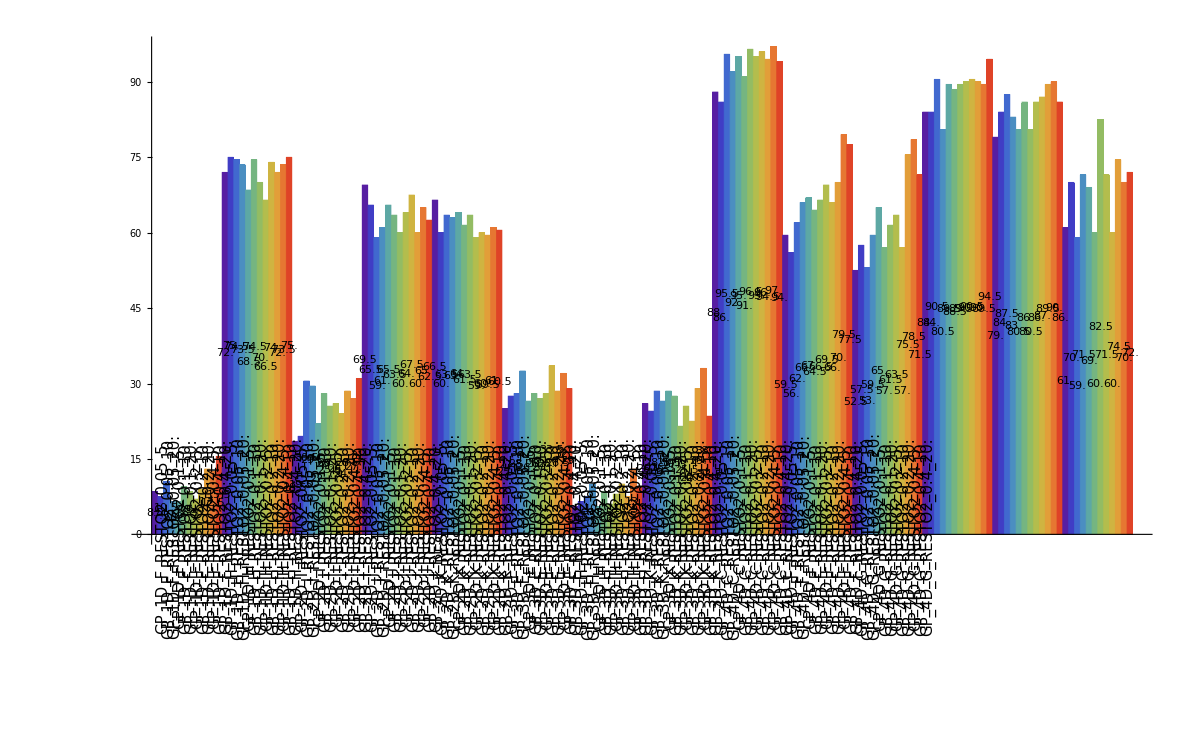

```mathematica
plotBooleanAsBarChart[sortedData,"SUCCESS",12]
```

```mathematica
printBooleanRanksAsTable[sortedData,"SUCCESS",12]//N
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
1. | 0.05 | 5. | 3.92143
4. | 0.1 | 5. | 4.91429
7. | 0.2 | 5. | 5.52143
2. | 0.05 | 10. | 5.66429
5. | 0.1 | 10. | 6.35
8. | 0.2 | 10. | 6.4
3. | 0.05 | 20. | 6.62143
9. | 0.2 | 20. | 6.71429
6. | 0.1 | 20. | 6.9
10. | 0.4 | 5. | 7.92143
12. | 0.4 | 20. | 8.03571
11. | 0.4 | 10. | 9.03571

```mathematica
RESTO2PAR
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
1. | 0.05 | 5. | 4.
2. | 0.05 | 10. | 4.53571
7. | 0.2 | 5. | 5.57143
5. | 0.1 | 10. | 5.57143
8. | 0.2 | 10. | 6.03571
6. | 0.1 | 20. | 6.03571
4. | 0.1 | 5. | 6.25
3. | 0.05 | 20. | 6.89286
9. | 0.2 | 20. | 7.07143
10. | 0.4 | 5. | 7.92857
12. | 0.4 | 20. | 8.67857
11. | 0.4 | 10. | 9.42857

```mathematica
RANDOM2PAR
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
1. | 0.05 | 5. | 2.10714
4. | 0.1 | 5. | 3.17857
2. | 0.05 | 10. | 5.07143
3. | 0.05 | 20. | 5.42857
6. | 0.1 | 20. | 6.25
5. | 0.1 | 10. | 6.28571
7. | 0.2 | 5. | 6.5
8. | 0.2 | 10. | 7.28571
9. | 0.2 | 20. | 7.67857
10. | 0.4 | 5. | 8.17857
12. | 0.4 | 20. | 9.60714
11. | 0.4 | 10. | 10.4286

```mathematica
BASICPAR
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
9. | 0.2 | 20. | 4.25
8. | 0.2 | 10. | 4.64286
7. | 0.2 | 5. | 5.
10. | 0.4 | 5. | 5.21429
12. | 0.4 | 20. | 5.53571
11. | 0.4 | 10. | 5.67857
4. | 0.1 | 5. | 6.25
5. | 0.1 | 10. | 7.53571
1. | 0.05 | 5. | 7.75
6. | 0.1 | 20. | 8.03571
2. | 0.05 | 10. | 8.78571
3. | 0.05 | 20. | 9.32143

```mathematica
TREEPPAR
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
1. | 0.05 | 5. | 2.89286
4. | 0.1 | 5. | 4.67857
2. | 0.05 | 10. | 4.67857
7. | 0.2 | 5. | 5.17857
5. | 0.1 | 10. | 6.28571
3. | 0.05 | 20. | 6.64286
6. | 0.1 | 20. | 6.71429
8. | 0.2 | 10. | 6.89286
9. | 0.2 | 20. | 7.
12. | 0.4 | 20. | 8.17857
10. | 0.4 | 5. | 9.32143
11. | 0.4 | 10. | 9.53571

```mathematica
TREEP2PAR
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
1. | 0.05 | 5. | 2.85714
4. | 0.1 | 5. | 4.21429
3. | 0.05 | 20. | 4.82143
2. | 0.05 | 10. | 5.25
7. | 0.2 | 5. | 5.35714
5. | 0.1 | 10. | 6.07143
8. | 0.2 | 10. | 7.14286
6. | 0.1 | 20. | 7.46429
9. | 0.2 | 20. | 7.57143
12. | 0.4 | 20. | 8.17857
10. | 0.4 | 5. | 8.96429
11. | 0.4 | 10. | 10.1071

## Experiments IV

```mathematica
names={"HGP_RANDOMPAR","HGP_BASICPAR","HGP_TREEPPAR","HGP_TREEP2PAR"};
(*names={"HGP_RANDOMPAR"};*)
data=readAllFiles[names,Null,ReplaceParamValues->{"FC55"->"ZFC55"}];
data=assignLabelsByParameters[data,{"SOLVER","ID","RECO.GENERATOR","GPAT.DISTANCE","GP.DISTANCE","GPEFS.SPECIES_REPRODUCTION_RATIO","GPEFS.SPECIES_SIZE_MEAN"},{"ZFC55"->"FC55","hyper.experiments.reco.problem.PatternGeneratorXOR"->"",RegularExpression["hyper.experiments.reco.problem.PatternGenerator"]->""}];
changingParameters[data]
```

{GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GP.DISTANCE,GPEFS.SPECIES_REPRODUCTION_RATIO,GPEFS.SPECIES_SIZE_MEAN,ID,NET_ACTIVATIONS,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE}

```mathematica
(*sdata=selectData[data,{"SOLVER"->"GPAT","GPAT.DISTANCE"->{"SIMPLE_REC5","SIMPLE_REC6","SIMPLE_REC7"}}];*)
(*sdata=removeData[data,{"GPAT.DISTANCE_WEIGHTED_C1"->{0.5,2.}}];*)
(*sdata=removeData[data,{"GPAT.DISTANCE"->{"SIMPLE_REC","SIMPLE_REC2","SIMPLE_REC3"}}];*)
sortedData = sortDataByParams[data,{"ID","RECO.GENERATOR","SOLVER","GPAT.DISTANCE"}];
printAsTable[sortedData,{"SOLVER","GPAT.FUNCTION_IMPL","ID","RECO.GENERATOR","MAZE.MAP","GPAT.DISTANCE","GP.TARGET_FITNESS","PROBLEM","GPAT.DISTANCE_WEIGHTED_C1"}]
```

ID | PARAM FILE | SOLVER | GPAT.FUNCTION_IMPL | ID | RECO.GENERATOR | MAZE.MAP | GPAT.DISTANCE | GP.TARGET_FITNESS | PROBLEM | GPAT.DISTANCE_WEIGHTED_C1
GP_FC_RANDOM_0.05_5. | HGP_RANDOMPAR/parameters_001.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_RANDOM_0.05_10. | HGP_RANDOMPAR/parameters_002.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_RANDOM_0.05_20. | HGP_RANDOMPAR/parameters_003.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_RANDOM_0.1_5. | HGP_RANDOMPAR/parameters_004.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_RANDOM_0.1_10. | HGP_RANDOMPAR/parameters_005.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_RANDOM_0.1_20. | HGP_RANDOMPAR/parameters_006.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_RANDOM_0.2_5. | HGP_RANDOMPAR/parameters_007.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_RANDOM_0.2_10. | HGP_RANDOMPAR/parameters_008.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_RANDOM_0.2_20. | HGP_RANDOMPAR/parameters_009.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_RANDOM_0.4_5. | HGP_RANDOMPAR/parameters_010.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_RANDOM_0.4_10. | HGP_RANDOMPAR/parameters_011.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_RANDOM_0.4_20. | HGP_RANDOMPAR/parameters_012.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_BASIC_0.05_5. | HGP_BASICPAR/parameters_001.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_BASIC_0.05_10. | HGP_BASICPAR/parameters_002.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_BASIC_0.05_20. | HGP_BASICPAR/parameters_003.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_BASIC_0.1_5. | HGP_BASICPAR/parameters_004.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_BASIC_0.1_10. | HGP_BASICPAR/parameters_005.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_BASIC_0.1_20. | HGP_BASICPAR/parameters_006.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_BASIC_0.2_5. | HGP_BASICPAR/parameters_007.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_BASIC_0.2_10. | HGP_BASICPAR/parameters_008.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_BASIC_0.2_20. | HGP_BASICPAR/parameters_009.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_BASIC_0.4_5. | HGP_BASICPAR/parameters_010.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_BASIC_0.4_10. | HGP_BASICPAR/parameters_011.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_BASIC_0.4_20. | HGP_BASICPAR/parameters_012.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP_0.05_5. | HGP_TREEPPAR/parameters_001.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP_0.05_10. | HGP_TREEPPAR/parameters_002.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP_0.05_20. | HGP_TREEPPAR/parameters_003.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP_0.1_5. | HGP_TREEPPAR/parameters_004.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP_0.1_10. | HGP_TREEPPAR/parameters_005.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP_0.1_20. | HGP_TREEPPAR/parameters_006.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP_0.2_5. | HGP_TREEPPAR/parameters_007.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP_0.2_10. | HGP_TREEPPAR/parameters_008.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP_0.2_20. | HGP_TREEPPAR/parameters_009.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP_0.4_5. | HGP_TREEPPAR/parameters_010.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP_0.4_10. | HGP_TREEPPAR/parameters_011.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP_0.4_20. | HGP_TREEPPAR/parameters_012.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP2_0.05_5. | HGP_TREEP2PAR/parameters_001.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP2_0.05_10. | HGP_TREEP2PAR/parameters_002.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP2_0.05_20. | HGP_TREEP2PAR/parameters_003.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP2_0.1_5. | HGP_TREEP2PAR/parameters_004.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP2_0.1_10. | HGP_TREEP2PAR/parameters_005.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP2_0.1_20. | HGP_TREEP2PAR/parameters_006.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP2_0.2_5. | HGP_TREEP2PAR/parameters_007.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP2_0.2_10. | HGP_TREEP2PAR/parameters_008.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP2_0.2_20. | HGP_TREEP2PAR/parameters_009.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP2_0.4_5. | HGP_TREEP2PAR/parameters_010.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP2_0.4_10. | HGP_TREEP2PAR/parameters_011.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_FC_TREEP2_0.4_20. | HGP_TREEP2PAR/parameters_012.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
GP_RECO1D_CopyMirrored1D_RANDOM_0.05_5. | HGP_RANDOMPAR/parameters_013.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_RANDOM_0.05_10. | HGP_RANDOMPAR/parameters_016.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_RANDOM_0.05_20. | HGP_RANDOMPAR/parameters_019.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_RANDOM_0.1_5. | HGP_RANDOMPAR/parameters_022.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_RANDOM_0.1_10. | HGP_RANDOMPAR/parameters_025.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_RANDOM_0.1_20. | HGP_RANDOMPAR/parameters_028.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_RANDOM_0.2_5. | HGP_RANDOMPAR/parameters_031.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_RANDOM_0.2_10. | HGP_RANDOMPAR/parameters_034.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_RANDOM_0.2_20. | HGP_RANDOMPAR/parameters_037.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_RANDOM_0.4_5. | HGP_RANDOMPAR/parameters_040.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_RANDOM_0.4_10. | HGP_RANDOMPAR/parameters_043.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_RANDOM_0.4_20. | HGP_RANDOMPAR/parameters_046.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_BASIC_0.05_5. | HGP_BASICPAR/parameters_013.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_BASIC_0.05_10. | HGP_BASICPAR/parameters_016.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_BASIC_0.05_20. | HGP_BASICPAR/parameters_019.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_BASIC_0.1_5. | HGP_BASICPAR/parameters_022.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_BASIC_0.1_10. | HGP_BASICPAR/parameters_025.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_BASIC_0.1_20. | HGP_BASICPAR/parameters_028.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_BASIC_0.2_5. | HGP_BASICPAR/parameters_031.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_BASIC_0.2_10. | HGP_BASICPAR/parameters_034.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_BASIC_0.2_20. | HGP_BASICPAR/parameters_037.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_BASIC_0.4_5. | HGP_BASICPAR/parameters_040.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_BASIC_0.4_10. | HGP_BASICPAR/parameters_043.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_BASIC_0.4_20. | HGP_BASICPAR/parameters_046.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP_0.05_5. | HGP_TREEPPAR/parameters_013.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP_0.05_10. | HGP_TREEPPAR/parameters_016.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP_0.05_20. | HGP_TREEPPAR/parameters_019.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP_0.1_5. | HGP_TREEPPAR/parameters_022.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP_0.1_10. | HGP_TREEPPAR/parameters_025.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP_0.1_20. | HGP_TREEPPAR/parameters_028.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP_0.2_5. | HGP_TREEPPAR/parameters_031.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP_0.2_10. | HGP_TREEPPAR/parameters_034.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP_0.2_20. | HGP_TREEPPAR/parameters_037.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP_0.4_5. | HGP_TREEPPAR/parameters_040.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP_0.4_10. | HGP_TREEPPAR/parameters_043.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP_0.4_20. | HGP_TREEPPAR/parameters_046.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP2_0.05_5. | HGP_TREEP2PAR/parameters_013.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP2_0.05_10. | HGP_TREEP2PAR/parameters_016.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP2_0.05_20. | HGP_TREEP2PAR/parameters_019.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP2_0.1_5. | HGP_TREEP2PAR/parameters_022.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP2_0.1_10. | HGP_TREEP2PAR/parameters_025.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP2_0.1_20. | HGP_TREEP2PAR/parameters_028.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP2_0.2_5. | HGP_TREEP2PAR/parameters_031.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP2_0.2_10. | HGP_TREEP2PAR/parameters_034.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP2_0.2_20. | HGP_TREEP2PAR/parameters_037.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP2_0.4_5. | HGP_TREEP2PAR/parameters_040.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP2_0.4_10. | HGP_TREEP2PAR/parameters_043.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyMirrored1D_TREEP2_0.4_20. | HGP_TREEP2PAR/parameters_046.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_RANDOM_0.05_5. | HGP_RANDOMPAR/parameters_015.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_RANDOM_0.05_10. | HGP_RANDOMPAR/parameters_018.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_RANDOM_0.05_20. | HGP_RANDOMPAR/parameters_021.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_RANDOM_0.1_5. | HGP_RANDOMPAR/parameters_024.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_RANDOM_0.1_10. | HGP_RANDOMPAR/parameters_027.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_RANDOM_0.1_20. | HGP_RANDOMPAR/parameters_030.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_RANDOM_0.2_5. | HGP_RANDOMPAR/parameters_033.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_RANDOM_0.2_10. | HGP_RANDOMPAR/parameters_036.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_RANDOM_0.2_20. | HGP_RANDOMPAR/parameters_039.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_RANDOM_0.4_5. | HGP_RANDOMPAR/parameters_042.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_RANDOM_0.4_10. | HGP_RANDOMPAR/parameters_045.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_RANDOM_0.4_20. | HGP_RANDOMPAR/parameters_048.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_BASIC_0.05_5. | HGP_BASICPAR/parameters_015.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_BASIC_0.05_10. | HGP_BASICPAR/parameters_018.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_BASIC_0.05_20. | HGP_BASICPAR/parameters_021.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_BASIC_0.1_5. | HGP_BASICPAR/parameters_024.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_BASIC_0.1_10. | HGP_BASICPAR/parameters_027.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_BASIC_0.1_20. | HGP_BASICPAR/parameters_030.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_BASIC_0.2_5. | HGP_BASICPAR/parameters_033.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_BASIC_0.2_10. | HGP_BASICPAR/parameters_036.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_BASIC_0.2_20. | HGP_BASICPAR/parameters_039.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_BASIC_0.4_5. | HGP_BASICPAR/parameters_042.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_BASIC_0.4_10. | HGP_BASICPAR/parameters_045.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_BASIC_0.4_20. | HGP_BASICPAR/parameters_048.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP_0.05_5. | HGP_TREEPPAR/parameters_015.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP_0.05_10. | HGP_TREEPPAR/parameters_018.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP_0.05_20. | HGP_TREEPPAR/parameters_021.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP_0.1_5. | HGP_TREEPPAR/parameters_024.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP_0.1_10. | HGP_TREEPPAR/parameters_027.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP_0.1_20. | HGP_TREEPPAR/parameters_030.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP_0.2_5. | HGP_TREEPPAR/parameters_033.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP_0.2_10. | HGP_TREEPPAR/parameters_036.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP_0.2_20. | HGP_TREEPPAR/parameters_039.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP_0.4_5. | HGP_TREEPPAR/parameters_042.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP_0.4_10. | HGP_TREEPPAR/parameters_045.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP_0.4_20. | HGP_TREEPPAR/parameters_048.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP2_0.05_5. | HGP_TREEP2PAR/parameters_015.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP2_0.05_10. | HGP_TREEP2PAR/parameters_018.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP2_0.05_20. | HGP_TREEP2PAR/parameters_021.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP2_0.1_5. | HGP_TREEP2PAR/parameters_024.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP2_0.1_10. | HGP_TREEP2PAR/parameters_027.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP2_0.1_20. | HGP_TREEP2PAR/parameters_030.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP2_0.2_5. | HGP_TREEP2PAR/parameters_033.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP2_0.2_10. | HGP_TREEP2PAR/parameters_036.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP2_0.2_20. | HGP_TREEP2PAR/parameters_039.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP2_0.4_5. | HGP_TREEP2PAR/parameters_042.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP2_0.4_10. | HGP_TREEP2PAR/parameters_045.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyRotated1D_TREEP2_0.4_20. | HGP_TREEP2PAR/parameters_048.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_RANDOM_0.05_5. | HGP_RANDOMPAR/parameters_014.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_RANDOM_0.05_10. | HGP_RANDOMPAR/parameters_017.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_RANDOM_0.05_20. | HGP_RANDOMPAR/parameters_020.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_RANDOM_0.1_5. | HGP_RANDOMPAR/parameters_023.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_RANDOM_0.1_10. | HGP_RANDOMPAR/parameters_026.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_RANDOM_0.1_20. | HGP_RANDOMPAR/parameters_029.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_RANDOM_0.2_5. | HGP_RANDOMPAR/parameters_032.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_RANDOM_0.2_10. | HGP_RANDOMPAR/parameters_035.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_RANDOM_0.2_20. | HGP_RANDOMPAR/parameters_038.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_RANDOM_0.4_5. | HGP_RANDOMPAR/parameters_041.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_RANDOM_0.4_10. | HGP_RANDOMPAR/parameters_044.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_RANDOM_0.4_20. | HGP_RANDOMPAR/parameters_047.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_BASIC_0.05_5. | HGP_BASICPAR/parameters_014.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_BASIC_0.05_10. | HGP_BASICPAR/parameters_017.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_BASIC_0.05_20. | HGP_BASICPAR/parameters_020.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_BASIC_0.1_5. | HGP_BASICPAR/parameters_023.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_BASIC_0.1_10. | HGP_BASICPAR/parameters_026.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_BASIC_0.1_20. | HGP_BASICPAR/parameters_029.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_BASIC_0.2_5. | HGP_BASICPAR/parameters_032.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_BASIC_0.2_10. | HGP_BASICPAR/parameters_035.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_BASIC_0.2_20. | HGP_BASICPAR/parameters_038.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_BASIC_0.4_5. | HGP_BASICPAR/parameters_041.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_BASIC_0.4_10. | HGP_BASICPAR/parameters_044.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_BASIC_0.4_20. | HGP_BASICPAR/parameters_047.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP_0.05_5. | HGP_TREEPPAR/parameters_014.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP_0.05_10. | HGP_TREEPPAR/parameters_017.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP_0.05_20. | HGP_TREEPPAR/parameters_020.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP_0.1_5. | HGP_TREEPPAR/parameters_023.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP_0.1_10. | HGP_TREEPPAR/parameters_026.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP_0.1_20. | HGP_TREEPPAR/parameters_029.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP_0.2_5. | HGP_TREEPPAR/parameters_032.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP_0.2_10. | HGP_TREEPPAR/parameters_035.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP_0.2_20. | HGP_TREEPPAR/parameters_038.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP_0.4_5. | HGP_TREEPPAR/parameters_041.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP_0.4_10. | HGP_TREEPPAR/parameters_044.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP_0.4_20. | HGP_TREEPPAR/parameters_047.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP2_0.05_5. | HGP_TREEP2PAR/parameters_014.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP2_0.05_10. | HGP_TREEP2PAR/parameters_017.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP2_0.05_20. | HGP_TREEP2PAR/parameters_020.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP2_0.1_5. | HGP_TREEP2PAR/parameters_023.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP2_0.1_10. | HGP_TREEP2PAR/parameters_026.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP2_0.1_20. | HGP_TREEP2PAR/parameters_029.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP2_0.2_5. | HGP_TREEP2PAR/parameters_032.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP2_0.2_10. | HGP_TREEP2PAR/parameters_035.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP2_0.2_20. | HGP_TREEP2PAR/parameters_038.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP2_0.4_5. | HGP_TREEP2PAR/parameters_041.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP2_0.4_10. | HGP_TREEP2PAR/parameters_044.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_RECO1D_CopyShifted1D_TREEP2_0.4_20. | HGP_TREEP2PAR/parameters_047.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO | NONE
GP_XOR_RANDOM_0.05_5. | HGP_RANDOMPAR/parameters_049.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_RANDOM_0.05_10. | HGP_RANDOMPAR/parameters_050.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_RANDOM_0.05_20. | HGP_RANDOMPAR/parameters_051.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_RANDOM_0.1_5. | HGP_RANDOMPAR/parameters_052.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_RANDOM_0.1_10. | HGP_RANDOMPAR/parameters_053.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_RANDOM_0.1_20. | HGP_RANDOMPAR/parameters_054.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_RANDOM_0.2_5. | HGP_RANDOMPAR/parameters_055.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_RANDOM_0.2_10. | HGP_RANDOMPAR/parameters_056.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_RANDOM_0.2_20. | HGP_RANDOMPAR/parameters_057.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_RANDOM_0.4_5. | HGP_RANDOMPAR/parameters_058.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_RANDOM_0.4_10. | HGP_RANDOMPAR/parameters_059.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_RANDOM_0.4_20. | HGP_RANDOMPAR/parameters_060.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_BASIC_0.05_5. | HGP_BASICPAR/parameters_049.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_BASIC_0.05_10. | HGP_BASICPAR/parameters_050.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_BASIC_0.05_20. | HGP_BASICPAR/parameters_051.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_BASIC_0.1_5. | HGP_BASICPAR/parameters_052.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_BASIC_0.1_10. | HGP_BASICPAR/parameters_053.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_BASIC_0.1_20. | HGP_BASICPAR/parameters_054.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_BASIC_0.2_5. | HGP_BASICPAR/parameters_055.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_BASIC_0.2_10. | HGP_BASICPAR/parameters_056.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_BASIC_0.2_20. | HGP_BASICPAR/parameters_057.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_BASIC_0.4_5. | HGP_BASICPAR/parameters_058.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_BASIC_0.4_10. | HGP_BASICPAR/parameters_059.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_BASIC_0.4_20. | HGP_BASICPAR/parameters_060.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP_0.05_5. | HGP_TREEPPAR/parameters_049.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP_0.05_10. | HGP_TREEPPAR/parameters_050.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP_0.05_20. | HGP_TREEPPAR/parameters_051.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP_0.1_5. | HGP_TREEPPAR/parameters_052.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP_0.1_10. | HGP_TREEPPAR/parameters_053.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP_0.1_20. | HGP_TREEPPAR/parameters_054.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP_0.2_5. | HGP_TREEPPAR/parameters_055.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP_0.2_10. | HGP_TREEPPAR/parameters_056.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP_0.2_20. | HGP_TREEPPAR/parameters_057.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP_0.4_5. | HGP_TREEPPAR/parameters_058.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP_0.4_10. | HGP_TREEPPAR/parameters_059.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP_0.4_20. | HGP_TREEPPAR/parameters_060.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP2_0.05_5. | HGP_TREEP2PAR/parameters_049.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP2_0.05_10. | HGP_TREEP2PAR/parameters_050.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP2_0.05_20. | HGP_TREEP2PAR/parameters_051.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP2_0.1_5. | HGP_TREEP2PAR/parameters_052.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP2_0.1_10. | HGP_TREEP2PAR/parameters_053.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP2_0.1_20. | HGP_TREEP2PAR/parameters_054.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP2_0.2_5. | HGP_TREEP2PAR/parameters_055.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP2_0.2_10. | HGP_TREEP2PAR/parameters_056.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP2_0.2_20. | HGP_TREEP2PAR/parameters_057.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP2_0.4_5. | HGP_TREEP2PAR/parameters_058.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP2_0.4_10. | HGP_TREEP2PAR/parameters_059.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE
GP_XOR_TREEP2_0.4_20. | HGP_TREEP2PAR/parameters_060.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR | NONE

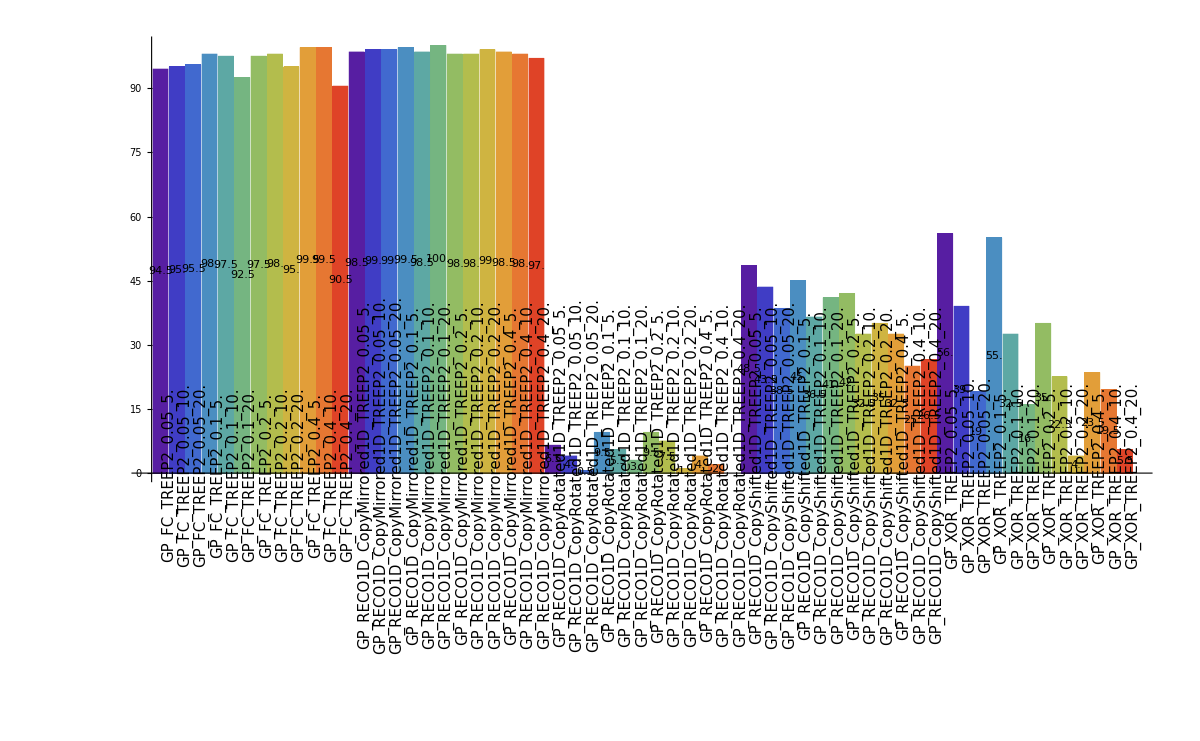

```mathematica
plotBooleanAsBarChart[sortedData,"SUCCESS",12]
```

```mathematica
plotAsBoxWhiskerChart[sortedData,"BSFG",10]
```

```mathematica
printBooleanRanksAsTable[sortedData,"SUCCESS",12]//N
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
9. | 0.2 | 20. | 4.15
6. | 0.1 | 20. | 4.975
12. | 0.4 | 20. | 5.3
3. | 0.05 | 20. | 5.85
8. | 0.2 | 10. | 6.05
1. | 0.05 | 5. | 6.825
5. | 0.1 | 10. | 6.95
4. | 0.1 | 5. | 7.15
11. | 0.4 | 10. | 7.2
2. | 0.05 | 10. | 7.325
7. | 0.2 | 5. | 7.85
10. | 0.4 | 5. | 8.375

```mathematica
RANDOMPAR
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
4. | 0.1 | 5. | 3.7
1. | 0.05 | 5. | 3.7
8. | 0.2 | 10. | 5.3
7. | 0.2 | 5. | 5.6
5. | 0.1 | 10. | 5.8
9. | 0.2 | 20. | 6.3
6. | 0.1 | 20. | 6.3
2. | 0.05 | 10. | 6.3
3. | 0.05 | 20. | 8.1
12. | 0.4 | 20. | 8.3
10. | 0.4 | 5. | 9.2
11. | 0.4 | 10. | 9.4

```mathematica
BASICPAR
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
9. | 0.2 | 20. | 3.1
6. | 0.1 | 20. | 3.6
3. | 0.05 | 20. | 4.2
8. | 0.2 | 10. | 5.9
4. | 0.1 | 5. | 6.3
12. | 0.4 | 20. | 6.7
5. | 0.1 | 10. | 6.8
2. | 0.05 | 10. | 7.
1. | 0.05 | 5. | 7.1
7. | 0.2 | 5. | 8.
11. | 0.4 | 10. | 9.
10. | 0.4 | 5. | 10.3

```mathematica
TREEPPAR
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
9. | 0.2 | 20. | 2.7
6. | 0.1 | 20. | 4.
12. | 0.4 | 20. | 4.8
11. | 0.4 | 10. | 5.5
3. | 0.05 | 20. | 5.5
8. | 0.2 | 10. | 6.6
10. | 0.4 | 5. | 7.1
4. | 0.1 | 5. | 7.8
2. | 0.05 | 10. | 8.
5. | 0.1 | 10. | 8.1
1. | 0.05 | 5. | 8.1
7. | 0.2 | 5. | 9.8

```mathematica
TREEP2PAR
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
12. | 0.4 | 20. | 1.4
9. | 0.2 | 20. | 4.5
11. | 0.4 | 10. | 4.9
3. | 0.05 | 20. | 5.6
6. | 0.1 | 20. | 6.
8. | 0.2 | 10. | 6.4
10. | 0.4 | 5. | 6.9
5. | 0.1 | 10. | 7.1
7. | 0.2 | 5. | 8.
2. | 0.05 | 10. | 8.
1. | 0.05 | 5. | 8.4
4. | 0.1 | 5. | 10.8

## Statistics

```mathematica
testMannWhitney[data,"GPAT_H","GPAT_H2","BSF"]
```

median 1: 0.952853

median 2: 0.949325

mean 1: 0.754262

mean 2: 0.528663

variance 1: 0.135817

variance 2: 0.222969

higher/lower variance ratio: 1.64169

U stat: 22636

P-value: 0.0226329

The null hypothesis that the median difference is 0 is rejected at the 5. percent level based on the Mann-Whitney test.

```mathematica
testKruskalWallis[data,{"GP_H","GPAT_H2"},"BSF"]
```

| GPAT_H | GPAT_H2
Mean | 0.754262 | 0.528663
Variance | 0.952853 | 0.949325
Variance | 0.135817 | 0.222969

LocationEquivalenceTest::ntsymmd: The p-value in 1.14305×10^-13, resulting from a test for symmetry, is below 0.05. The tests in {"KruskalWallis"} require that the data is symmetric about a common median.

| Statistic | P-Value
Kruskal-Wallis | 5.19838 | 0.0224202

```mathematica
testFisherExact[{{90,10},{82,18}}]
```

0.152819

```mathematica
testFisherExact[sortedData,"GPAT_E","GPATGP_E","SUCCESS",TwoSided->True,PValueOnly->False]
```

| GPAT_E | GPATGP_E
true | 0. | 1.
false | 200. | 199.
p-value | 1. |

```mathematica
testFisherExactAll[sortedData,"SUCCESS",0.05,TwoSided->True]
```

| 2 | 3 | 4 | 5 | 6
1 | 0.0900213 | 8.70428×10^-7 | 2.99731×10^-15 | 4.39804×10^-33 | 2.71714×10^-43
2 |  | 0.00174071 | 7.22079×10^-10 | 4.23269×10^-25 | 2.75651×10^-34
3 |  |  | 0.00295964 | 3.33437×10^-13 | 3.18256×10^-20
4 |  |  |  | 0.0000196958 | 4.04422×10^-10
5 |  |  |  |  | 0.0552636

## Expressions

```mathematica
sortConfigurationResults[sortedData,"A","BSF",10]
```

1 | 0.996687
12 | 0.983575
100 | 0.970368
78 | 0.96933
10 | 0.968461
60 | 0.968217
79 | 0.963918
73 | 0.958339
68 | 0.956159
35 | 0.955737

```mathematica
Expand[1.5*x1*x2+2.3*x1+x2*x3*x4-1.1*x3]
```

2.3 x1+1.5 x1 x2-1.1 x3+x2 x3 x4

```mathematica
(res=sortConfigurationResults[sortedData,"GP3D_H2","BSF",10,Output->"Expressions"]/.{x0->Subscript[x, 1],x1->Subscript[x, 2],x2->Subscript[x, 3],x3->Subscript[x, 4]})
```

Gen | Expression | Expanded | f
last | {x_2 (-1.+x_1 (x_3+x_2 x_3))} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_2 (-1.+x_1 x_3+x_1 x_2 x_3)} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+(x_1 x_2+x_1 x_2^2) x_3} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+x_2 (x_1+x_1 x_2) x_3} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_1 x_2^2 x_3+x_2 (-1.+x_1 x_3)} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_1-1. x_2+x_1 (-1.+x_2 x_3+x_2^2 x_3)} | {0.-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_2 (-1.+(x_1+x_1 x_2) x_3)} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {1.08185×10^-8-1. x_2+(x_1 x_2+x_1 x_2^2) x_3} | {1.08185×10^-8-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+x_1 (4.44373×10^-11+x_2 x_3+x_2^2 x_3)} | {4.44373×10^-11 x_1-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.

```mathematica
(res=sortConfigurationResults[sortedData,"12","BSF",25,Output->"Expressions"]/.{x0->x})
```

Gen | Expression | Expanded | f
last | {0.09977 x (x+Sin[0.787112 ⅇ^(-x^2)])} | {0.09977 x^2+0.09977 x Sin[0.787112 ⅇ^(-x^2)]} | 0.995529
last | {0.0646032 x (ⅇ^(-x^2)+1.55385 x)-0.0344501 Sin[1.-ⅇ^(-x^2)]} | {0.0646032 ⅇ^(-x^2) x+0.100383 x^2-0.0344501 Sin[1.-ⅇ^(-x^2)]} | 0.995316
last | {0.100061 x (0.0156719+x)} | {0.00156814 x+0.100061 x^2} | 0.995278
last | {ⅇ^(-11.8063-Sin[x]^2)+0.0999739 x (0.021377+x)} | {ⅇ^(-11.8063-Sin[x]^2)+0.00213714 x+0.0999739 x^2} | 0.995253
last | {0.100195 x^2} | {0.100195 x^2} | 0.995163
last | {0.0997882 x^2} | {0.0997882 x^2} | 0.995147
last | {-0.0015477+0.100253 x^2} | {-0.0015477+0.100253 x^2} | 0.995127
last | {0.0995871 x^2} | {0.0995871 x^2} | 0.994844
last | {0.0995752 x^2} | {0.0995752 x^2} | 0.99482
last | {0.100443 x^2} | {0.100443 x^2} | 0.994783
last | {0.0999352 (-0.0328145+x) x} | {-0.00327932 x+0.0999352 x^2} | 0.994597
last | {0.0994062 x^2} | {0.0994062 x^2} | 0.994405
last | {0.100651 x^2} | {0.100651 x^2} | 0.994233
last | {4.35401×10^-11+0.100887 x (ⅇ^(-x^2)+x)} | {4.35401×10^-11+0.100887 ⅇ^(-x^2) x+0.100887 x^2} | 0.993847
last | {0.10084 x^2} | {0.10084 x^2} | 0.993554
last | {0.0993273 x (ⅇ^(-33.9284 (3.47822+x)^2)+x)} | {0.0993273 ⅇ^(-33.9284 (3.47822+x)^2) x+0.0993273 x^2} | 0.993273
last | {0.0990122 x^2} | {0.0990122 x^2} | 0.992907
last | {-0.000371379+0.0990141 x^2} | {-0.000371379+0.0990141 x^2} | 0.992889
last | {Sin[0.129682 x] (x-Sin[0.336709 x]-0.196058 Sin[x])} | {x Sin[0.129682 x]-Sin[0.129682 x] Sin[0.336709 x]-0.196058 Sin[0.129682 x] Sin[x]} | 0.992606
last | {0.101464 (-0.763579+x (0.0208029+x))} | {-0.0774756+0.00211074 x+0.101464 x^2} | 0.992428
last | {0.0988539 x^2} | {0.0988539 x^2} | 0.992097
last | {0.101382 x (ⅇ^(-0.332217 x^2)+x)} | {0.101382 ⅇ^(-0.332217 x^2) x+0.101382 x^2} | 0.99195
last | {(0.815193 x^2 (-0.632121 ⅇ^(-(4.80488+x)^2)+x+ⅇ^(-x^2) (2.03518+x)) ArcTan[x])/(√(1+140.445 x^2))} | {(1.65907 ⅇ^(-x^2) x^2 ArcTan[x])/(√(1+140.445 x^2))-(0.5153 ⅇ^(-(4.80488+x)^2) x^2 ArcTan[x])/(√(1+140.445 x^2))+(0.815193 x^3 ArcTan[x])/(√(1+140.445 x^2))+(0.815193 ⅇ^(-x^2) x^3 ArcTan[x])/(√(1+140.445 x^2))} | 0.991336
last | {0.10128 x^2} | {0.10128 x^2} | 0.991321
last | {0.0989743 x (0.0785205+x)} | {0.00777151 x+0.0989743 x^2} | 0.991136

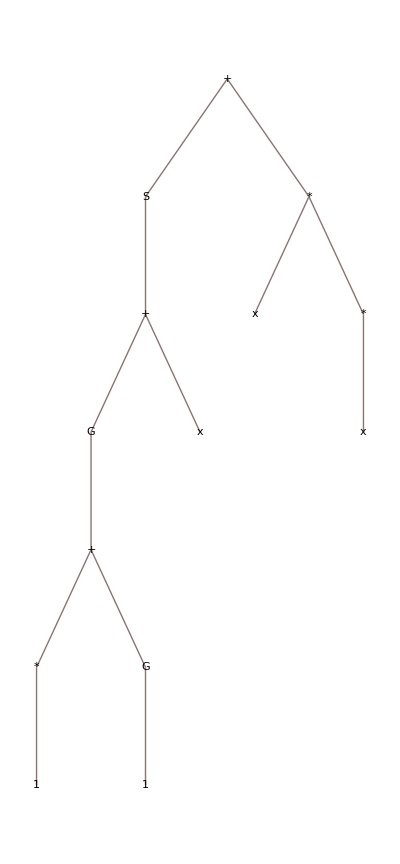
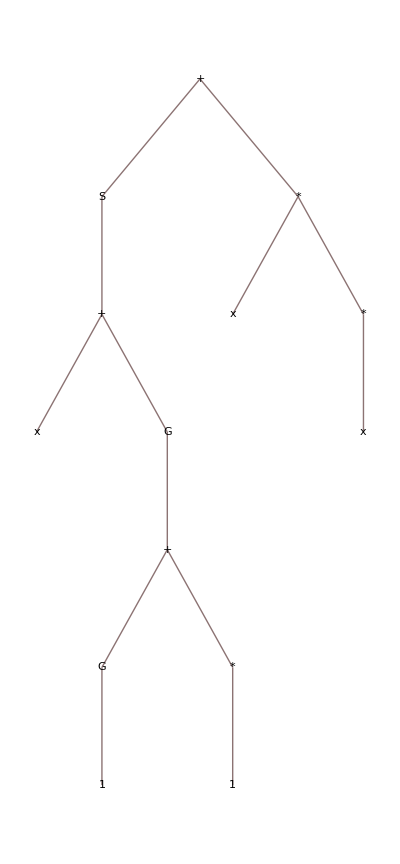
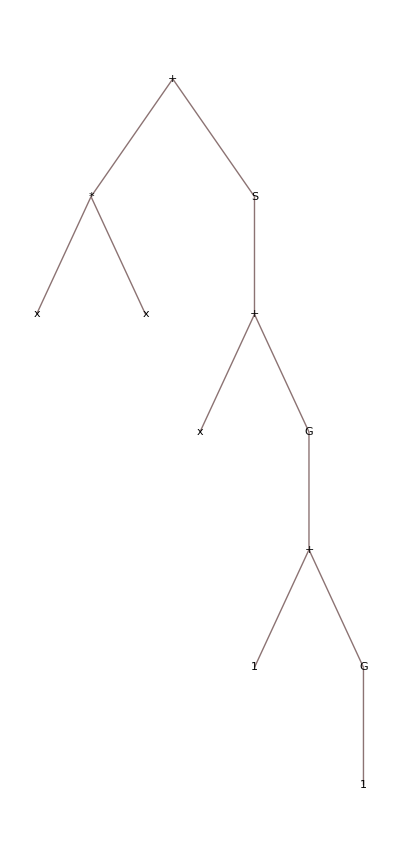
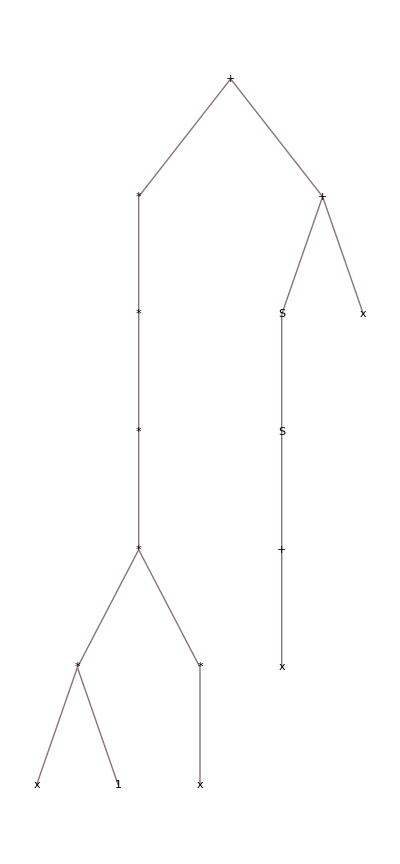
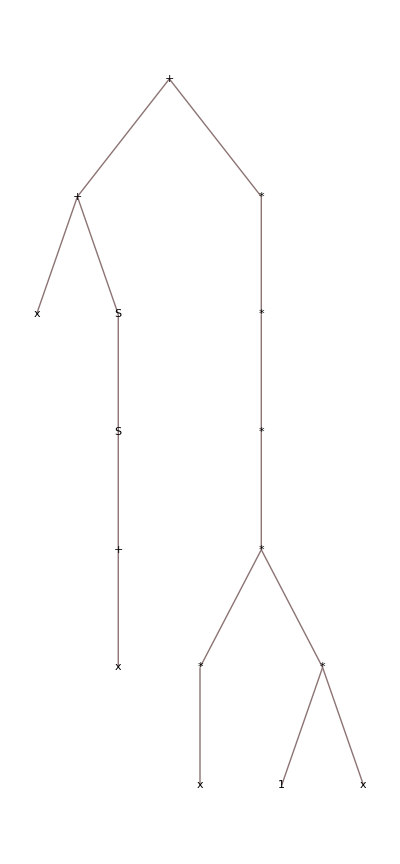
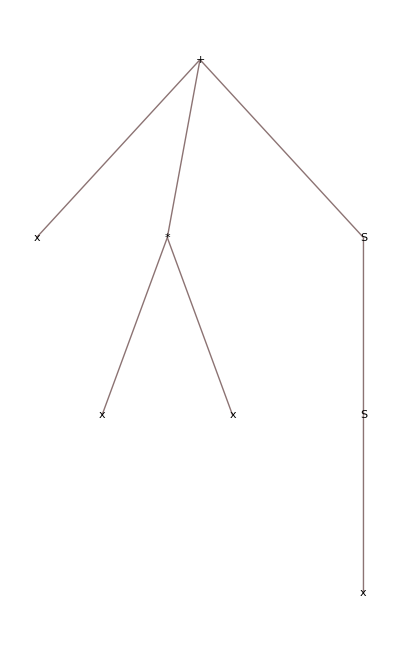
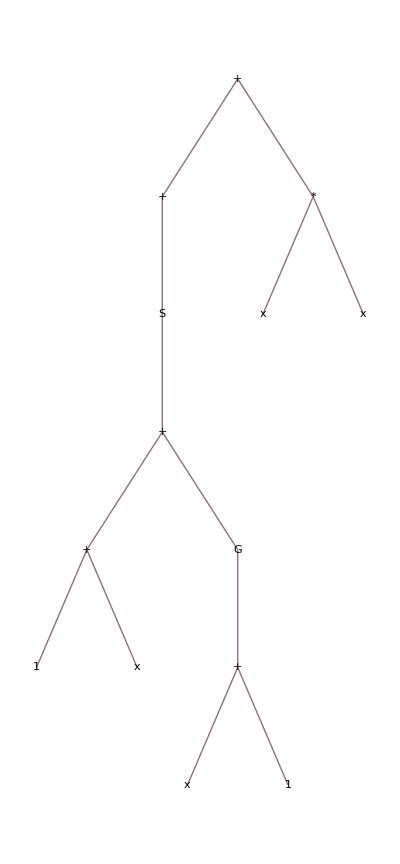
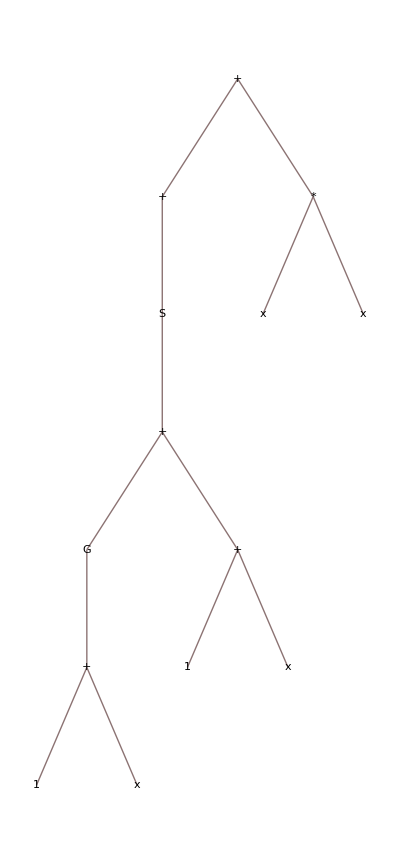
Gen | Genome | Sorted | Simplified | f
last | -Graphics- | -Graphics- | -Graphics- | 0.99656
last | -Graphics- | -Graphics- | -Graphics- | 0.983261
last | -Graphics- | -Graphics- | -Graphics- | 0.978954
last | -Graphics- | -Graphics- | -Graphics- | 0.978529
last | -Graphics- | -Graphics- | -Graphics- | 0.957386
last | -Graphics- | -Graphics- | -Graphics- | 0.956843
last | -Graphics- | -Graphics- | -Graphics- | 0.952837
last | -Graphics- | -Graphics- | -Graphics- | 0.951168
last | -Graphics- | -Graphics- | -Graphics- | 0.940757
last | -Graphics- | -Graphics- | -Graphics- | 0.852304

```mathematica
(res=sortConfigurationResults[sortedData,"A","BSF",10,Output->"BSFGenomes"]/.{x0->x})
```

```mathematica
Export["GP_H2.pdf",%]
```

GP_H2.pdf